# Homogeneous isotropization with Maxwell field - Fuini

### Initialization:

```mathematica
SetDirectory["/phys/users/fuini/Research/Dropbox/Yaffe/Mathematica"];
(*SetDirectory["C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Mathematica"];*)
<<EDCRGTCcode.m
```

### Cosmetics:

```mathematica
(*Format[A[v,r]] = A;
Format[B[v,r]] = B;
Format[Σ[v,r]] = Σ;
(*Format[Derivative[0,1][e_][v,r]=e'];*)
(*Format[Derivative[0,2][e_][v,r]=e''];*)s
Format[Derivative[1,1][e_][v,r]=Subscript[e', v]];
Format[Derivative[1,0][e_][v,r]=Subscript[e, v]];
Format[Derivative[2,0][e_][v,r]=Subscript[e, vv]];*)
```

```mathematica
(* Format is causing me problems.  It seems to make something like D[D[Σ[v,r],r],r] = 0 because the derivative on the inside is getting set to Σ' via the format... and then the derivative of that is zero.  So instead, I'm just going to make a rule called clean... this seems to fix the problem. *)
```

```mathematica
clean = {Derivative[1,0,0][SubPlus[d]][f_,v,r]:>Subscript[(SubPlus[d]), f[[0]]][f[[0]]],Derivative[0,1,0][SubPlus[d]][f_,v,r]:>Subscript[(SubPlus[d]), v][f[[0]]],Derivative[0,0,1][SubPlus[d]][f_,v,r]:>Subscript[(SubPlus[d]), r][f[[0]]],A[v,r]:> A, B[v,r]:>B,Σ[v,r]:>Σ,Fvz[v,r]:>Fvz,Fvr[v,r]:>Fvr,Fxy[v,r]:>Fxy,Fzr[v,r]:>Fzr,D[e_[v,r],r]:>Subscript[e, r],D[e_[v,r],r,r]:>Subscript[e, rr],D[e_[v,r],r,v]:>Subscript[e, rv],D[e_[v,r],v]:>Subscript[e, v],D[e_[v,r],v,v]:>Subscript[e, vv],SubPlus[d][e_[v,r],v,r]:>SubPlus[d][e]};
```

### Metric ansatz:

```mathematica
coord = {v,x,y,z,r};
metricIN= DiagonalMatrix[{-A[v,r],Σ[v,r]^2 ⅇ^B[v,r],Σ[v,r]^2 ⅇ^B[v,r],Σ[v,r]^2 ⅇ^(-2B[v,r]),0}];
metricIN[[1,5]] = 1;
metricIN[[5,1]] = 1;
RGtensors[metricIN,coord];
{"(Γ^μ)_rr", GUdd[[1;;5,5,5]]}
{"det(g)",Det[metricIN]}
```

gdd = (-A[v,r] | 0 | 0 | 0 | 1
0 | ⅇ^B[v,r] Σ[v,r]^2 | 0 | 0 | 0
0 | 0 | ⅇ^B[v,r] Σ[v,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^(-2 B[v,r]) Σ[v,r]^2 | 0
1 | 0 | 0 | 0 | 0)

LineElement = 2 d[r] d[v]-A[v,r] d[v]^2+ⅇ^B[v,r] d[x]^2 Σ[v,r]^2+ⅇ^B[v,r] d[y]^2 Σ[v,r]^2+ⅇ^(-2 B[v,r]) d[z]^2 Σ[v,r]^2

gUU = (0 | 0 | 0 | 0 | 1
0 | ⅇ^(-B[v,r])/Σ[v,r]^2 | 0 | 0 | 0
0 | 0 | ⅇ^(-B[v,r])/Σ[v,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^(2 B[v,r])/Σ[v,r]^2 | 0
1 | 0 | 0 | 0 | A[v,r])

gUU computed in 0.002999 sec

Gamma computed in 0.023997 sec

Riemann(dddd) computed in 0.046993 sec

Riemann(Uddd) computed in 0.069989 sec

Ricci computed in 0.029995 sec

Weyl computed in 0.083988 sec

Einstein computed in 0.012998 sec

All tasks completed in 0.278958 seconds

{(Γ^μ)_rr,{0,0,0,0,0}}

{det(g),-Σ[v,r]^6}

### Local "orthogonal" frame:

```mathematica
SubMinus[η]={0,0,0,0,1};
SubPlus[η]={1,0,0,0,A[v,r]/2};
Subscript[η, 1]={0,1,0,0,0};
Subscript[η, 2]={0,0,1,0,0};
Subscript[η, 3]={0,0,0,1,0};
```

```mathematica
dvsub = {D[e_[v,r],v]:> SubPlus[d][e[v,r],v,r]-A[v,r]/2 D[e[v,r],r],D[e_[v,r],v,v]:> SubPlus[d][SubPlus[d][e[v,r],v,r],v,r]-A[v,r]D[SubPlus[d][e[v,r],v,r],r]-1/2 SubPlus[d][A[v,r],v,r]D[e[v,r],r] + A[v,r]/2 D[A[v,r],r]D[e[v,r],r]+A[v,r]^2/4 D[e[v,r],r,r],D[e_[v,r],r,v]:>D[SubPlus[d][e[v,r],v,r],r]-D[A[v,r],r]/2 D[e[v,r],r]-A[v,r]/2 D[e[v,r],r,r] };
```

```mathematica
dvunsub = (*d_+[e_[v,r]]:>D[e[v,r],v]+A[v,r]/2 D[e[v,r],r]*)SubPlus[d][e_[v,r],v,r]:>D[e[v,r],v]+A[v,r]/2 D[e[v,r],r];
```

```mathematica
vierbein = Transpose[{SubMinus[η],SubPlus[η],Subscript[η, 1],Subscript[η, 2],Subscript[η, 3]}];
Transpose[vierbein].gdd.vierbein//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | ⅇ^B[v,r] Σ[v,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^B[v,r] Σ[v,r]^2 | 0
0 | 0 | 0 | 0 | ⅇ^(-2 B[v,r]) Σ[v,r]^2)

### Maxwell:

```mathematica
Fdd = zeroTensor[2];
```

Maintaining the rotational symmetry in x-y plane, translational invariance in x,y, and z, and reflection symmetry in z, we know that the only non-zero entries are the following.

```mathematica
Fdd[[1,5]] = Fvr[v,r];
Fdd[[2,3]] = Fxy[v,r];
Fdd[[5,1]] = -Fdd[[1,5]];
Fdd[[3,2]] = -Fdd[[2,3]];
```

```mathematica
FUU=Raise[Raise[Fdd,1],2];
```

```mathematica
Fdd/.clean//MatrixForm
```

(0 | 0 | 0 | 0 | Fvr
0 | 0 | Fxy | 0 | 0
0 | -Fxy | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-Fvr | 0 | 0 | 0 | 0)

```mathematica
Tdd = 1/κ^2 L^2/g^2(2( Transpose[Fdd]).Raise[Fdd,1]-Tr[Transpose[Fdd].FUU]/2 gdd);
```

This κ^2  is equal to 8 pi G_5.   Not sure why it was called kappa back in the day.  But the original action we worked with was

S = 1/(2 κ^2)∫√(| g |)d^5 x (R - 2Λ - L^2/g^2 F^2)

But then we said meh to L and g and set them to 1.

```mathematica
TUU = Raise[Raise[Tdd,1],2];
```

```mathematica
Table[1/κ^2 L^2/g^2(2Sum[Fdd[[a,i]]gUU[[a,b]]Fdd[[b,j]],{a,1,5},{b,1,5}]-Sum[Fdd[[a,b]]Raise[Raise[Fdd,1],2][[a,b]] gdd[[i,j]]/2,{a,1,5},{b,1,5}])-Tdd[[i,j]],{i,1,5},{j,1,5}]/.clean//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

### Einstein and Maxwell equations:

Einstein's equations, Maxwells equations

```mathematica
EUU = Raise[EUd,2];
EinstEQ = EUU - 6/L^2 gUU-κ^2 TUU //FullSimplify;
MaxEQ = zeroTensor[2];
For[j=1,j<6,j++,MaxEQ[[j]] = Sum[D[√-detg FUU[[i,j]],coord[[i]]],{i,1,5}]]

MaxAltEQ = zeroTensor[3];
For[i=1,i<6,i++,For[k=1,k<6,k++,For[l=1,l<6,l++,MaxAltEQ[[i,k,l]] = 1/(3!)(covD[Fdd][[i,k,l]]+covD[Fdd][[k,l,i]]+covD[Fdd][[l,i,k]]-covD[Fdd][[k,i,l]]-covD[Fdd][[i,l,k]]-covD[Fdd][[l,k,i]])]]]


{"Ein^11",EinstEQ[[1,1]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^15",EinstEQ[[1,5]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^22",EinstEQ[[2,2]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^44",EinstEQ[[4,4]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^55",EinstEQ[[5,5]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Max^1",MaxEQ[[1]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Max^5",MaxEQ[[5]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"MaxAlt^1",MaxAltEQ[[2,3,1]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"MaxAlt^2",MaxAltEQ[[2,3,5]]//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
```

{Ein^11,-(3 B_r^2)/2-(3 Σ_rr)/Σ}

{Ein^15,-6/L^2+(Fvr^2 L^2)/g^2+(ⅇ^(-2 B) Fxy^2 L^2)/(g^2 Σ^4)-(3 A B_r^2)/4+((3 A_r Σ_r)/2+3 Σ_rv)/Σ+(3 A Σ_r^2+6 Σ_r Σ_v)/Σ^2}

{Ein^22,-(ⅇ^(-3 B) Fxy^2 L^2)/(g^2 Σ^6)+ⅇ^-B ((-24 g^2-4 Fvr^2 L^4+2 g^2 L^2 A_rr-2 g^2 L^2 A_r B_r+3 A g^2 L^2 B_r^2-2 A g^2 L^2 B_rr-4 g^2 L^2 B_rv+6 g^2 L^2 B_r B_v)/(4 g^2 L^2 Σ^2)+(8 g^2 L^2 A_r Σ_r-6 A g^2 L^2 B_r Σ_r-6 g^2 L^2 B_v Σ_r+8 A g^2 L^2 Σ_rr+16 g^2 L^2 Σ_rv-6 g^2 L^2 B_r Σ_v)/(4 g^2 L^2 Σ^3)+(4 A g^2 L^2 Σ_r^2+8 g^2 L^2 Σ_r Σ_v)/(4 g^2 L^2 Σ^4))}

{Ein^44,(Fxy^2 L^2)/(g^2 Σ^6)+ⅇ^(2 B) ((-24 g^2-4 Fvr^2 L^4+2 g^2 L^2 A_rr+4 g^2 L^2 A_r B_r+3 A g^2 L^2 B_r^2+4 A g^2 L^2 B_rr+8 g^2 L^2 B_rv+6 g^2 L^2 B_r B_v)/(4 g^2 L^2 Σ^2)+(8 g^2 L^2 A_r Σ_r+12 A g^2 L^2 B_r Σ_r+12 g^2 L^2 B_v Σ_r+8 A g^2 L^2 Σ_rr+16 g^2 L^2 Σ_rv+12 g^2 L^2 B_r Σ_v)/(4 g^2 L^2 Σ^3)+(4 A g^2 L^2 Σ_r^2+8 g^2 L^2 Σ_r Σ_v)/(4 g^2 L^2 Σ^4))}

{Ein^55,-(6 A)/L^2+(A Fvr^2 L^2)/g^2+(A ⅇ^(-2 B) Fxy^2 L^2)/(g^2 Σ^4)-3/4 A^2 B_r^2-3/2 A B_r B_v-(3 B_v^2)/2+(3 A^2 Σ_r^2+6 A Σ_r Σ_v)/Σ^2+(3/2 A A_r Σ_r-(3 A_v Σ_r)/2+(3 A_r Σ_v)/2-3 Σ_vv)/Σ}

{Max^1,√(Σ^6) Fvr_r+(3 Fvr Σ^5 Σ_r)/(√(Σ^6))}

{Max^5,-√(Σ^6) Fvr_v-(3 Fvr Σ^5 Σ_v)/(√(Σ^6))}

{MaxAlt^1,Fxy_v/3}

{MaxAlt^2,Fxy_r/3}

Fxy is a constant.

```mathematica
MaxAltEQ[[2,3,5]]
```

1/6 ((2 Fxy[v,r] (Σ[v,r] B^(0,1)[v,r]+2 Σ^(0,1)[v,r]))/Σ[v,r]+(2 (-Fxy[v,r] Σ[v,r] B^(0,1)[v,r]+Σ[v,r] Fxy^(0,1)[v,r]-2 Fxy[v,r] Σ^(0,1)[v,r]))/Σ[v,r])

### DVSUB

```mathematica
{"Ein^11",EinstEQ[[1,1]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^15",EinstEQ[[1,5]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^22",EinstEQ[[2,2]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^44",EinstEQ[[4,4]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Ein^55",EinstEQ[[5,5]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Max^1",MaxEQ[[1]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"Max^5",MaxEQ[[5]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"MaxAlt^1",MaxAltEQ[[2,3,1]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
{"MaxAlt^2",MaxAltEQ[[2,3,5]]/.dvsub//FullSimplify//Collect[#,{ⅇ^(2B[v,r]),Σ[v,r]}]&}/.clean
```

{Ein^11,-(3 B_r^2)/2-(3 Σ_rr)/Σ}

{Ein^15,-6/L^2+(Fvr^2 L^2)/g^2+(ⅇ^(-2 B) Fxy^2 L^2)/(g^2 Σ^4)-(3 A B_r^2)/4+(6 Σ_r d_+[Σ])/Σ^2+(-(3 A Σ_rr)/2+3 (d_+)_r[Σ]+3 Σ_r (d_+)_Σ[Σ])/Σ}

{Ein^22,-(ⅇ^(-3 B) Fxy^2 L^2)/(g^2 Σ^6)+ⅇ^-B ((2 Σ_r d_+[Σ])/Σ^4+(-12 g^2-2 Fvr^2 L^4+g^2 L^2 A_rr+3 g^2 L^2 B_r d_+[B]-2 g^2 L^2 B_r (d_+)_B[B]-2 g^2 L^2 (d_+)_r[B])/(2 g^2 L^2 Σ^2)+(-3 g^2 L^2 Σ_r d_+[B]-3 g^2 L^2 B_r d_+[Σ]+8 g^2 L^2 (d_+)_r[Σ]+8 g^2 L^2 Σ_r (d_+)_Σ[Σ])/(2 g^2 L^2 Σ^3))}

{Ein^44,(Fxy^2 L^2)/(g^2 Σ^6)+ⅇ^(2 B) ((2 Σ_r d_+[Σ])/Σ^4+(-12 g^2-2 Fvr^2 L^4+g^2 L^2 A_rr+3 g^2 L^2 B_r d_+[B]+4 g^2 L^2 B_r (d_+)_B[B]+4 g^2 L^2 (d_+)_r[B])/(2 g^2 L^2 Σ^2)+(6 g^2 L^2 Σ_r d_+[B]+6 g^2 L^2 B_r d_+[Σ]+8 g^2 L^2 (d_+)_r[Σ]+8 g^2 L^2 Σ_r (d_+)_Σ[Σ])/(2 g^2 L^2 Σ^3))}

{Ein^55,-(6 A)/L^2+(A Fvr^2 L^2)/g^2+(A ⅇ^(-2 B) Fxy^2 L^2)/(g^2 Σ^4)-3/8 A^2 B_r^2-3/2 (d_+[B])^2+(6 A Σ_r d_+[Σ])/Σ^2+(-3/4 A^2 Σ_rr+3/2 A_r d_+[Σ]-3 d_+[d_+[Σ],v,r]+3 A (d_+)_r[Σ]+3 A Σ_r (d_+)_Σ[Σ])/Σ}

{Max^1,√(Σ^6) Fvr_r+(3 Fvr Σ^5 Σ_r)/(√(Σ^6))}

{Max^5,1/2 √(Σ^6) (A Fvr_r-2 d_+[Fvr])+(3 Fvr Σ^5 (A Σ_r-2 d_+[Σ]))/(2 √(Σ^6))}

{MaxAlt^1,1/6 (-A Fxy_r+2 d_+[Fxy])}

{MaxAlt^2,Fxy_r/3}

### Bianchi Identity:

Lets check the Bianchi Identity.

```mathematica
X=covD[Rdddd];
bianchi=X+Transpose[X,{3,1,2,4,5}]+Transpose[X,{2,3,1,4,5}];
Temp = zeroTensor[5];
bianchi===Temp
Clear[X,Y,Temp]
```

True

```mathematica
Bianchi[0]
Bianchi[1]
Bianchi[2]
```

{}

{}

{}

```mathematica
(* what are we even checking here?? *)
```

### Simplifying Einstein's equations:

From the MaxAlt equations, we know Fxy is a constant for all time.

```mathematica
Fxy = fxy&;
```

Checks...

```mathematica
{Fxy[v,r],Derivative[3,0][Fxy][v,r],D[Fxy[v,r],r]}
```

{fxy,0,0}

```mathematica
Σeqn = -Σ[v,r]/3*EinstEQ[[1,1]]//FullSimplify
Σeqnnice = Σeqn/.clean
```

1/2 Σ[v,r] (B^(0,1)[v,r])^2+Σ^(0,2)[v,r]

(Σ B_r^2)/2+Σ_rr

This finds us Σ for all r at one time, provided we have B_r at that time.

```mathematica
FvrReqn =√(Σ[v,r]^6)1/Σ[v,r]^5 MaxEQ[[1]]//FullSimplify
FvrRnice = FvrReqn /.clean
```

Σ[v,r] Fvr^(0,1)[v,r]+3 Fvr[v,r] Σ^(0,1)[v,r]

Σ Fvr_r+3 Fvr Σ_r

This finds us Fvr at the one time that we have Σ.

It then seems like we have the evolution of Fvr without the need for B from the following.

```mathematica
FvrVeqn =- √(Σ[v,r]^6)1/Σ[v,r]^5 MaxEQ[[5]]//FullSimplify
FvrVnice = FvrVeqn /.clean
```

Σ[v,r] Fvr^(1,0)[v,r]+3 Fvr[v,r] Σ^(1,0)[v,r]

Σ Fvr_v+3 Fvr Σ_v

Fvr evolves in the exact same way as a function of v or r.

```mathematica
Σdoteqn = EinstEQ[[1,5]] Σ[v,r]^4+3/2 Σ[v,r]^3 A[v,r] Σeqn//FullSimplify
Σdotnice = Σdoteqn /.dvsub/.clean//FullSimplify
```

(ⅇ^(-2 B[v,r]) fxy^2 L^2)/g^2+(-6/L^2+(L^2 Fvr[v,r]^2)/g^2) Σ[v,r]^4+3 Σ[v,r]^2 Σ^(0,1)[v,r] (A[v,r] Σ^(0,1)[v,r]+2 Σ^(1,0)[v,r])+3/2 Σ[v,r]^3 (A^(0,1)[v,r] Σ^(0,1)[v,r]+A[v,r] Σ^(0,2)[v,r]+2 Σ^(1,1)[v,r])

(ⅇ^(-2 B) L^2 (fxy&)^2)/g^2+Σ^2 (Σ (-(6 Σ)/L^2+(Fvr^2 L^2 Σ)/g^2+3 (d_+)_r[Σ])+3 Σ_r (2 d_+[Σ]+Σ (d_+)_Σ[Σ]))

```mathematica
6 Σ^2 (Σ (-2 Σ+SubPlus[d][Σ]')+2 Σ' SubPlus[d][Σ])
```

6 Σ^2 (Σ (-2 Σ+d_+[Σ]')+2 Σ' d_+[Σ])

This finds us Σdot at one time - provided we have Σ, Fxy, and Fvr, at one time.

```mathematica
Bdoteqn=2/3 Σ[v,r]^6(ⅇ^B[v,r] EinstEQ[[2,2]] - ⅇ^(-2B[v,r])EinstEQ[[4,4]])//FullSimplify//Collect[#,{E^(2B[v,r]),Σ[v,r]}]&
Bdotnice=Bdoteqn /.dvsub/.clean//FullSimplify
```

-(4 ⅇ^(-2 B[v,r]) fxy^2 L^2)/(3 g^2)+Σ[v,r]^3 (-3 A[v,r] B^(0,1)[v,r] Σ^(0,1)[v,r]-3 Σ^(0,1)[v,r] B^(1,0)[v,r]-3 B^(0,1)[v,r] Σ^(1,0)[v,r])+Σ[v,r]^4 (-A^(0,1)[v,r] B^(0,1)[v,r]-A[v,r] B^(0,2)[v,r]-2 B^(1,1)[v,r])

-(4 ⅇ^(-2 B) L^2 (fxy&)^2)/(3 g^2)-Σ^3 (3 Σ_r d_+[B]+B_r (3 d_+[Σ]+2 Σ (d_+)_B[B])+2 Σ (d_+)_r[B])

This finds us Bdot provided we have Σdot, Σ, Fxy, and B_rat one time.

```mathematica
Σddoteqn = -1/4 Σ[v,r]^-1(EinstEQ[[5,5]]8 Σ[v,r]^4+6 Σeqn Σ[v,r]^3 A[v,r]^2- 8Σdoteqn A[v,r])//FullSimplify
Σddotnice = Σddoteqn /.dvsub/.clean//FullSimplify
```

3/4 Σ[v,r]^2 (A[v,r]^2 (Σ[v,r] (B^(0,1)[v,r])^2+2 Σ^(0,2)[v,r])+4 Σ^(0,1)[v,r] A^(1,0)[v,r]+4 Σ[v,r] (B^(1,0)[v,r])^2-4 A^(0,1)[v,r] Σ^(1,0)[v,r]+4 A[v,r] (Σ[v,r] B^(0,1)[v,r] B^(1,0)[v,r]+2 Σ^(1,1)[v,r])+8 Σ^(2,0)[v,r])

3 Σ^2 (Σ (d_+[B])^2-A_r d_+[Σ]+2 d_+[d_+[Σ],v,r])

```mathematica
Aeqn = (4/3(2 EinstEQ[[2,2]] ⅇ^B[v,r]+ EinstEQ[[4,4]] ⅇ^(-2B[v,r]))Σ[v,r]^6-16/3 Σ[v,r]^4 EinstEQ[[1,5]]-8 A[v,r] Σ[v,r]^3 Σeqn//FullSimplify//Collect[#,{A[v,r],Derivative[0,0,2][A][v,r],E^(2B[v,r])}]&)
Anice = Aeqn /.dvsub/.clean//FullSimplify
```

-(20 ⅇ^(-2 B[v,r]) fxy^2 L^2)/(3 g^2)+(8 Σ[v,r]^4)/L^2-(28 L^2 Fvr[v,r]^2 Σ[v,r]^4)/(3 g^2)+A[v,r] (3 Σ[v,r]^4 (B^(0,1)[v,r])^2-12 Σ[v,r]^2 (Σ^(0,1)[v,r])^2)+2 Σ[v,r]^4 A^(0,2)[v,r]+6 Σ[v,r]^4 B^(0,1)[v,r] B^(1,0)[v,r]-24 Σ[v,r]^2 Σ^(0,1)[v,r] Σ^(1,0)[v,r]

(4 (6-(7 Fvr^2 L^4)/g^2) Σ^4)/(3 L^2)-(20 ⅇ^(-2 B) L^2 (fxy&)^2)/(3 g^2)+2 Σ^4 (A_rr+3 B_r d_+[B])-24 Σ^2 Σ_r d_+[Σ]

```mathematica
eoms = {Σeqn,FvrReqn,FvrVeqn,Bdoteqn,Σdoteqn,Σddoteqn,Aeqn};
```

### Residual diffeomorphism freedom:

We want to show that everything is invariant under the coordinate transformation r→r+λ[v].

```mathematica
diffeo1={r:>r+ϵ λ[v],d[e_[v,r],v]:>d[e[v,r],v]+d[e[v,r],r]ϵ D[λ[v],v]};
diffeo2 ={e_[v,r+ϵ λ[v]]:>e[v,r]+D[e[v,r],r]ϵ λ[v]};
```

ds^2

```mathematica
dcoord = {d[v],d[x],d[y],d[z],d[r]};
dsds = dcoord.gdd.dcoord;
dsds /.diffeo1/.clean//FullSimplify
LineElement
```

ⅇ^(-2 B[v,r+ϵ λ[v]]) (ⅇ^(3 B[v,r+ϵ λ[v]]) (d[x]^2+d[y]^2)+d[z]^2) Σ[v,r+ϵ λ[v]]^2+d[v] (2 d[r]-A[v,r+ϵ λ[v]] d[v]+2 d[ϵ] λ[v]+2 ϵ d[v] λ'[v])

2 d[r] d[v]-A[v,r] d[v]^2+ⅇ^B[v,r] d[x]^2 Σ[v,r]^2+ⅇ^B[v,r] d[y]^2 Σ[v,r]^2+ⅇ^(-2 B[v,r]) d[z]^2 Σ[v,r]^2

This matches the funtional form of our original ds^2.

```mathematica
((Σeqn/.diffeo1)/.diffeo2)-(Σeqn + ϵ λ[v]D[Σeqn,r])+O[ϵ]^2//FullSimplify
((Aeqn/.diffeo1)/.diffeo2)-(Aeqn + ϵ λ[v]D[Aeqn,r])+O[ϵ]^2//FullSimplify
((Bdoteqn/.diffeo1)/.diffeo2)-(Bdoteqn + ϵ λ[v]D[Bdoteqn,r])+O[ϵ]^2//FullSimplify
```

O[ϵ]^2

O[ϵ]^2

O[ϵ]^2

### Apparent horizon:

See E. Poisson, An advanced course in general relativity, pg. 39.

We want to find the hypersurfaces orthogonal to some k vector field.

```mathematica
k = μ[v,r]{D[ϕ[v,r], v],0,0,0,D[ϕ[v,r], r]};
```

We then want to solve for ∂_v ϕ, and make this a new substitution rule.

```mathematica
ϕv = Solve[0==k.gUU.k,D[ϕ[v,r], v]][[1]]
```

{ϕ^(1,0)[v,r]→-1/2 A[v,r] ϕ^(0,1)[v,r]}

We expand on our substitution rule to also substitute for derivatives of ∂_v ϕ`

```mathematica
ϕvsub={ϕv,D[ϕv, v],D[ϕv, r]}//Flatten
```

{ϕ^(1,0)[v,r]→-1/2 A[v,r] ϕ^(0,1)[v,r],ϕ^(2,0)[v,r]→-1/2 ϕ^(0,1)[v,r] A^(1,0)[v,r]-1/2 A[v,r] ϕ^(1,1)[v,r],ϕ^(1,1)[v,r]→-1/2 A^(0,1)[v,r] ϕ^(0,1)[v,r]-1/2 A[v,r] ϕ^(0,2)[v,r]}

We now define k’s innerproduct with itself when ϕvsub has been used.

```mathematica
kdotDk = covD[k].Raise[k,1]/.ϕvsub;
```

```mathematica
kdotDk[[5]]//FullSimplify
```

1/2 μ[v,r] (ϕ^(0,1)[v,r])^2 (A[v,r] μ^(0,1)[v,r]+2 μ^(1,0)[v,r])

We see we can solve for ∂_v μ when we demand that k is a null vector and have used ϕvsub, and define this as a substitution rule.

```mathematica
μvsub = Solve[0==kdotDk[[1]]/.ϕvsub,D[μ[v,r], v]][[1]]//FullSimplify
```

{μ^(1,0)[v,r]→-1/2 A[v,r] μ^(0,1)[v,r]}

```mathematica
kdotDk[[1]]/.ϕvsub//FullSimplify
```

-1/4 A[v,r] μ[v,r] (ϕ^(0,1)[v,r])^2 (A[v,r] μ^(0,1)[v,r]+2 μ^(1,0)[v,r])

Lets make sure this is correct.

```mathematica
kdotDk/.ϕvsub/.μvsub//FullSimplify
```

{0,0,0,0,0}

Now the expansion parameter θ tells us where apparent horizons happen.

```mathematica
θ=covDiv[Raise[k,1],{1}]/.ϕvsub/.μvsub//FullSimplify
```

(3 μ[v,r] ϕ^(0,1)[v,r] (A[v,r] Σ^(0,1)[v,r]+2 Σ^(1,0)[v,r]))/(2 Σ[v,r])

```mathematica
θ/.clean
```

(3 (A Σ_r+2 Σ_v) ϕ_r μ[v,r])/(2 Σ)

We now define the condtion of an apparent horizon, when we choose ϕ to just be it’s second arguement

```mathematica
apphor = 0 ==θ /.dvsub/.ϕ->(#2 &)//FullSimplify
```

(μ[v,r] d_+[Σ[v,r],v,r])/Σ[v,r]==0

For nonzero μ and non-infinity Σ this means,

```mathematica
apphor = 0 == Σ[v,r]/μ[v,r] θ/.dvsub/.ϕ->(#2 &)//FullSimplify
```

d_+[Σ[v,r],v,r]==0

```mathematica
apphor/.dvunsub
```

1/2 A[v,r] Σ^(0,1)[v,r]+Σ^(1,0)[v,r]==0

Find condition on A[v,r] which will keep position of apparent horizon fixed in time, don’t forget the condition for an apparent horizon, d_+Σ[v,r]→0

```mathematica
Solve[(D[SubPlus[d][Σ[v,r],v,r]/.dvunsub,v]//.dvsub)==0,A[v,r]]//FullSimplify
```

{{A[v,r]→(2 d_+[d_+[Σ[v,r],v,r],v,r])/((d_+)^(0,0,1)[Σ[v,r],v,r]+Σ^(0,1)[v,r] (d_+)^(1,0,0)[Σ[v,r],v,r])}}

```mathematica
Solve[((D[SubPlus[d][Σ[v,r],v,r],v]//.dvsub)/.SubPlus[d][Σ[v,r],v,r]->0)==0,A[v,r]]
```

{{A[v,r]→(2 (d_+)^(0,1,0)[Σ[v,r],v,r])/(Σ^(0,1)[v,r] (d_+)^(1,0,0)[Σ[v,r],v,r])}}

This is not as simple as Yaffe’s case, where he added some of our identically zero differential equations.  I can’t see how to do that with our setup at the moment.

Attempt at making this closer to Yaffe’s result.

```mathematica
(D[SubPlus[d][Σ[v,r],v,r]/.dvunsub,v]//.dvsub)//FullSimplify
```

d_+[d_+[Σ[v,r],v,r],v,r]-1/2 A[v,r] ((d_+)^(0,0,1)[Σ[v,r],v,r]+Σ^(0,1)[v,r] (d_+)^(1,0,0)[Σ[v,r],v,r])

```mathematica
(D[SubPlus[d][Σ[v,r],v,r]/.dvunsub,v]//.dvsub)-1/(6 Σ[v,r]^2)(Σddoteqn/.dvsub)//FullSimplify
Solve[(%/.SubPlus[d][Σ[v,r],v,r]->0)==0,A[v,r]]/.clean
```

1/2 (-Σ[v,r] (d_+[B[v,r],v,r])^2+d_+[Σ[v,r],v,r] A^(0,1)[v,r]-A[v,r] ((d_+)^(0,0,1)[Σ[v,r],v,r]+Σ^(0,1)[v,r] (d_+)^(1,0,0)[Σ[v,r],v,r]))

{{A→-(Σ (d_+[B])^2)/((d_+)_r[Σ]+Σ_r (d_+)_Σ[Σ])}}

Which is really just
A→ -Σ/((d_+[Σ])_r)(d_+[B])^2

Now it happens that Yaffe’s Σdoteqn was
6 Σ^2 (Σ (-2 Σ+d_+[Σ]')+2 Σ' d_+[Σ])

And when d_+[Σ]=0 this goes to...
 (-2 Σ+d_+[Σ]')

Or...
Σ/d_+[Σ]' = 1/2

And if one was to replace that ratio in my answer then I would get Yaffe’s answer, namely...
{A→-1/2 (d_+[B])^2}

HOWEVER,

that is not my Σdoteqn.

This is what we are working with...

```mathematica
Σdoteqn /.dvsub/.clean//FullSimplify
```

(ⅇ^(-2 B) L^2 (fxy&)^2)/g^2+Σ^2 (Σ (-(6 Σ)/L^2+(Fvr^2 L^2 Σ)/g^2+3 (d_+)_r[Σ])+3 Σ_r (2 d_+[Σ]+Σ (d_+)_Σ[Σ]))

And when d_+[Σ]=0 this goes to...

```mathematica
Σdoteqn /.dvsub//FullSimplify
```

(ⅇ^(-2 B[v,r]) fxy^2 L^2)/g^2+Σ[v,r]^2 (6 d_+[Σ[v,r],v,r] Σ^(0,1)[v,r]+Σ[v,r] (((-6+(L^4 Fvr[v,r]^2)/g^2) Σ[v,r])/L^2+3 ((d_+)^(0,0,1)[Σ[v,r],v,r]+Σ^(0,1)[v,r] (d_+)^(1,0,0)[Σ[v,r],v,r])))

```mathematica
(ⅇ^(-2 B) (fxy&)^2)/g^2+Σ^2 (Σ (-6 Σ+(Fvr^2 Σ)/g^2+3 Subscript[SubPlus[d], r][Σ])+3 Subscript[Σ, r] Σ Subscript[SubPlus[d], Σ][Σ]);
%*1/Σ^3//FullSimplify
```

-6 Σ+(Fvr^2 Σ)/g^2+(ⅇ^(-2 B) (fxy&)^2)/(g^2 Σ^3)+3 (d_+)_r[Σ]+3 Σ_r (d_+)_Σ[Σ]

So the denominator here...
{{A→-(Σ (d_+[B])^2)/((d_+)_r[Σ]+Σ_r (d_+)_Σ[Σ])}}

goes to...
-1/3(-6 Σ+(Fvr^2 Σ)/g^2+(ⅇ^(-2 B) (fxy)^2)/(g^2 Σ^3))

So
A→ Σ (d_+[B])^2(-2Σ+(-u^2)^2 Fvu^2 Σ/(3 g^2)+(ⅇ^(-2 B) (fxy)^2)/(3 g^2 Σ^3))^-1

```mathematica
Σ (SubPlus[d][B])^2(-2Σ+(-u^2)^2 Fvu^2 Σ/(3 g^2)+(ⅇ^(-2 B) (fxy)^2)/(3 g^2 Σ^3))^-1/.SubPlus[d][B]->Bdot/.Σ->sigma//CForm
```

(Power(Bdot,2)*sigma)/(Power(fxy,2)/(3.*Power(E,2*B)*Power(g,2)*Power(sigma,3)) - 2*sigma + (Power(Fvu,2)*sigma*Power(u,4))/(3.*Power(g,2)))

### Near-boundary asymptotic expansion:

HEADS UP.  I”M COMMENTING OUT THE SOLVING AND KEEPING THE ASSIGNING TO MAKE IT GO FASTER, THEN THERE IS A  CHECK THAT THESE ASSIGMENTS DO SOLVE THE EQUATIONS.

```mathematica
(* situation with L's.  Log[r/L]? *)
L=1;
Mj=5; (*used to use 8.  Needlessly slow*)
```

Rules:

```mathematica
ruleexp[ord_] := Exp[x_]-> Series[ⅇ^x,{x,0,ord+3}]//Normal;
rulelog = Log[1/u]->LOG[X];
```

```mathematica
rulesoln= {};
```

```mathematica
Σexp[M_,Mj_]:= Σ->(Sum[σ[i,j][#1](Log[#2])^j#2^-i,{i,-1,M},{j,0,Mj}]&);
Clear[i,j];
Aexp[M_,Mj_]:= A->(Sum[a[i,j][#1](Log[#2])^j#2^-i,{i,-2,M},{j,0,Mj}]&);
Clear[i,j];
Bexp[M_,Mj_]:= B->(Sum[b[i,j][#1](Log[#2])^j#2^-i,{i,0,M},{j,0,Mj}]&);
Clear[i,j];
Fvrexp[M_,Mj_]:= Fvr->(Sum[fvr[i,j][#1](Log[#2])^j#2^-i,{i,0,M},{j,0,Mj}]&);
Clear[i,j];
bndryexp[M_,Mj_] := {Σexp[M,Mj],Aexp[M,Mj],Bexp[M,Mj],Fvrexp[M,Mj]};
Clear[i,j];
```

Set leading values:

```mathematica
σ[-1,0]=1&;
σ[-1,j_/;j>0]=0&;
a[-2,0]=1&;
a[-2,j_/;j>0]=0&;
b[0,0]=0&;
b[0,j_/;j>0]=0&;
Clear[j];
```

```mathematica
Loglist[eqn_,ord_]:=Coefficient[{Coefficient[(((eqn/.bndryexp[ord+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[ord+5]//.rulesoln),LOG[X],0], 
Coefficient[(((eqn/.bndryexp[ord+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[ord+5]//.rulesoln),LOG[X],1],
Coefficient[(((eqn/.bndryexp[ord+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[ord+5]//.rulesoln),LOG[X],2],
Coefficient[(((eqn/.bndryexp[ord+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[ord+5]//.rulesoln),LOG[X],3],
Coefficient[(((eqn/.bndryexp[ord+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[ord+5]//.rulesoln),LOG[X],4],
Coefficient[(((eqn/.bndryexp[ord+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[ord+5]//.rulesoln),LOG[X],5]},u,ord]
```

Must set Mj high enough to see the log terms you are interested in.

```mathematica
rulesoln={};
rulesoln
```

{}

Undetermined Coefficients.

```mathematica
σ[0,0]=λ;
```

Solving...

For our solving purposes, we will solve the first three elements of each column by setting them to zero.  If we wish to go further down the column we will need to increase the order of logs we expand each function to, Mj.

#### Lowest order for each equation.

Each equation has a different non-zero "lowest order" and these can be changed arbitrarily by multiplying by u^n so I will just solve all lowest orders of each equation at once.  First we will find the lowest order.

These are the last zero entries for each equation.

#### T = (-5)

```mathematica
T=-5;
```

```mathematica
ΣeqnOffset := T+6;
FvrReqnOffset := T+4;
FvrVeqnOffset := T+3;
BdoteqnOffset := T+1;
ΣdoteqnOffset := T;
ΣddoteqnOffset := T;
AeqnOffset := T;
```

The first nonzero entries are...

#### T = (-4)

```mathematica
T=-4;
```

```mathematica
Loglist[Σeqn, ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[0,i][v],{i,1,5}]]//Flatten
rulesoln=Append[rulesoln,Table[σ[0,i]->(0&),{i,1,5}]]//Flatten ;(* need to force the solutions to be zero functions *)
Loglist[Σeqn, ΣeqnOffset]//MatrixForm
```

(-σ[0,1][v]+2 σ[0,2][v]
-2 σ[0,2][v]+6 σ[0,3][v]
-3 σ[0,3][v]+12 σ[0,4][v]
-4 σ[0,4][v]+20 σ[0,5][v]
-5 σ[0,5][v]
0)

{σ[0,1][v]→0,σ[0,2][v]→0,σ[0,3][v]→0,σ[0,4][v]→0,σ[0,5][v]→0}

(0
0
0
0
0
0)

```mathematica
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[0,i][v],{i,0,5}]]//Flatten
rulesoln=Append[rulesoln,Table[fvr[0,i]->(0&),{i,0,5}]]//Flatten ;(* need to force the solutions to be zero functions *)
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(3 fvr[0,0][v]+fvr[0,1][v]
3 fvr[0,1][v]+2 fvr[0,2][v]
3 fvr[0,2][v]+3 fvr[0,3][v]
3 fvr[0,3][v]+4 fvr[0,4][v]
3 fvr[0,4][v]+5 fvr[0,5][v]
3 fvr[0,5][v])

{fvr[0,0][v]→0,fvr[0,1][v]→0,fvr[0,2][v]→0,fvr[0,3][v]→0,fvr[0,4][v]→0,fvr[0,5][v]→0}

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[b[1,i][v],{i,0,5}]]
rulesoln = Append[rulesoln,Table[b[1,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
```

(3 b[1,0][v]-2 b[1,1][v]-2 b[1,2][v]
3 b[1,1][v]-4 b[1,2][v]-6 b[1,3][v]
3 b[1,2][v]-6 b[1,3][v]-12 b[1,4][v]
3 b[1,3][v]-8 b[1,4][v]-20 b[1,5][v]
3 b[1,4][v]-10 b[1,5][v]
3 b[1,5][v])

{{b[1,0][v]→0,b[1,1][v]→0,b[1,2][v]→0,b[1,3][v]→0,b[1,4][v]→0,b[1,5][v]→0}}

(0
0
0
0
0
0)

```mathematica
Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,AeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

#### T = (-3)

```mathematica
T = -3;
```

```mathematica
(*Loglist[Σeqn, ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[1,i][v],{i,0,5}]]//Flatten*)
rulesoln=Append[rulesoln,Table[σ[1,i]->(0&),{i,0,5}]]//Flatten ;(* need to force the solutions to be zero functions *)
Loglist[Σeqn, ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[1,i][v],{i,0,5}]]//Flatten*)
rulesoln=Append[rulesoln,Table[fvr[1,i]->(0&),{i,0,5}]]//Flatten; (* need to force the solutions to be zero functions *)
Loglist[Σeqn, ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[b[2,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln, Table[b[2,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Solve[%[[1;;7]]==0,Table[a[-1,i][v],{i,0,6}]]//Flatten*)
rulesoln = Append[rulesoln,a[-1,0]->(2 λ[#]&)]//Flatten;
rulesoln = Append[rulesoln, Table[a[-1,i]->(0&),{i,1,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,AeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

#### T = (-2)

```mathematica
T = -2;
```

```mathematica
(*Loglist[Σeqn,ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[2,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln, Table[σ[2,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Σeqn,ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[2,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln, Table[fvr[2,i]->(0&),{i,0,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[b[3,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln, Table[b[3,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[a[0,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,a[0,0]->(λ[#]^2-2 λ'[#]&)]//Flatten;
rulesoln = Append[rulesoln, Table[a[0,i]->(0&),{i,1,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,AeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

#### T = (-1)

```mathematica
T=-1;
```

```mathematica
(*Loglist[Σeqn, ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[3,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,Table[σ[3,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Σeqn, ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[3,i][v],{i,1,5}]]//Flatten*)
rulesoln = Append[rulesoln,Table[fvr[3,i]->(0&),{i,1,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
Solve[%[[1]]==0,fvr[3,0]'[v]]//Flatten*)
rulesoln = Append[rulesoln,Derivative[1][fvr[3,0]]->(0&)];
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[b[4,i][v],{i,1,6}]]//Flatten*)
rulesoln = Append[rulesoln, b[4,1]->(fxy^2/(3 g^2)&)]//Flatten;
rulesoln = Append[rulesoln, Table[b[4,i]->(0&),{i,2,5}]]//Flatten;
```

```mathematica
Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[a[1,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln, Table[a[1,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,AeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

#### T = 0

```mathematica
T= 0;
```

```mathematica
(*Loglist[Σeqn,ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[4,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln, Table[σ[4,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Σeqn,ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[4,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,fvr[4,0]->(-3 λ[#] fvr[3,0][#]&)]//Flatten;
rulesoln = Append[rulesoln,Table[fvr[4,i]->(0&),{i,1,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]/.rulesoln//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Temp =Solve[%[[1;;6]]==0,Table[b[5,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{b[5,0]->((fxy^2 λ[#])/(3 g^2)-4 λ[#] b[4,0][#]+b[4,0]'[#]&),b[5,1]->(-(4 fxy^2 λ[#])/(3 g^2)&)}]//Flatten;
rulesoln = Append[rulesoln, Table[b[5,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Bdoteqn,BdoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[a[2,i][v],{i,1,6}]]//Flatten*)
rulesoln = Append[rulesoln,a[2,1]->(-(2 fxy^2)/(3 g^2)&)]//Flatten;
rulesoln = Append[rulesoln,Table[a[2,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(3 a[2,0]'[v]
0
0
0
0
0)

Here we see that a2 is an input constant.

```mathematica
rulesoln=Append[rulesoln,Derivative[1][a[2,0]]->(0&)]//Flatten;
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,AeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

#### T = 1

```mathematica
T=1;
```

```mathematica
(*Loglist[Σeqn,ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[5,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,Table[σ[5,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Σeqn,ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[5,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,fvr[5,0]->(6 λ[#]^2 fvr[3,0][#]&)]//Flatten;
rulesoln = Append[rulesoln,Table[fvr[5,i]->(0&),{i,1,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[b[6,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{b[6,0]->(-(3 fxy^2 λ[#]^2)/(2 g^2)+10 λ[#]^2 b[4,0][#]+(11 fxy^2 λ'[#])/(108 g^2)+7/3 b[4,0][#] λ'[#]-8/3 λ[#] b[4,0]'[#]+7/12 b[5,0]'[#]+2/9 b[5,1]'[#]&),b[6,1]->(-(-120 fxy^2 λ[#]^2-28 fxy^2 λ'[#]-21 g^2 b[5,1]'[#])/(36 g^2)&)}]//Flatten;
rulesoln = Append[rulesoln,Table[b[6,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Bdoteqn,BdoteqnOffset]//FullSimplify//MatrixForm
```

$Aborted

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[a[3,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{a[3,0]->(-(2 fxy^2 λ[#])/(3 g^2)-2 λ[#] a[2,0][#]&),a[3,1]->((4 fxy^2 λ[#])/(3 g^2)&)}]//Flatten;
rulesoln = Append[rulesoln, Table[a[3,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

#### T = 2

```mathematica
T=2;
```

```mathematica
(*Loglist[Σeqn,ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[6,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,Table[σ[6,i]->(0&),{i,0,5}]]//Flatten;
Loglist[Σeqn,ΣeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[6,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,fvr[6,0]->(-10 λ[#]^3 fvr[3,0][#]&)]//Flatten;
rulesoln = Append[rulesoln,Table[fvr[6,i]->(0&),{i,1,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[b[7,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{b[7,0]->((37 fxy^2 λ[#]^3)/(9 g^2)-20 λ[#]^3 b[4,0][#]+(fxy^2 λ[#] λ'[#])/(6 g^2)-14 λ[#] b[4,0][#] λ'[#]+37/7 λ[#]^2 b[4,0]'[#]+15/7 λ'[#] b[4,0]'[#]-19/14 λ[#] b[5,0]'[#]-373/588 λ[#] b[5,1]'[#]+3/7 b[6,0]'[#]+16/147 b[6,1]'[#]&),b[7,1]->(-(280 fxy^2 λ[#]^3+196 fxy^2 λ[#] λ'[#]+57 g^2 λ[#] b[5,1]'[#]-18 g^2 b[6,1]'[#])/(42 g^2)&)}]//Flatten;
rulesoln = Append[rulesoln,Table[b[7,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Bdoteqn,BdoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[a[4,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{a[4,0]->(-(-5 fxy^2 λ[#]^2-9 g^2 λ[#]^2 a[2,0][#]-(fvr[3,0][#])^2)/(3 g^2)&),a[4,1]->(-(2 fxy^2 λ[#]^2)/g^2&)}]//Flatten;
rulesoln = Append[rulesoln, Table[a[4,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Aeqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

#### T = 3

```mathematica
T=3;
```

```mathematica
(*Loglist[Σeqn,ΣeqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[σ[7,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{σ[7,0]->(-(19 fxy^4+56 fxy^2 g^2 b[4,0][#]+4704 g^4 (b[4,0][#])^2)/(32928 g^4)&),σ[7,1]->(-(fxy^4+168 fxy^2 g^2 b[4,0][#])/(1764 g^4)&),σ[7,2]->(-fxy^4/(63 g^4)&)}]//Flatten;
rulesoln = Append[rulesoln,Table[σ[7,i]->(0&),{i,3,5}]]//Flatten;
Loglist[Σeqn,ΣeqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;6]]==0,Table[fvr[7,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,fvr[7,0]->(15 λ[#]^4 fvr[3,0][#]&)]//Flatten;
rulesoln = Append[rulesoln,Table[fvr[7,i]->(0&),{i,1,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[b[8,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{b[8,0]->(1/(4608 g^4)(48 fxy^4+g^2 (128 λ[#]^4 (-319 fxy^2+1260 g^2 b[4,0][#])-42048 g^2 λ[#]^3 b[4,0]'[#]+6 λ[#]^2 (-448 (5 fxy^2-84 g^2 b[4,0][#]) λ'[#]+g^2 (1848 b[5,0]'[#]+1009 b[5,1]'[#]))-12 g^2 λ[#] (3912 λ'[#] b[4,0]'[#]+360 b[6,0]'[#]+107 b[6,1]'[#])+3 (32 a[2,0][#] (fxy^2-24 g^2 b[4,0][#])+388 fxy^2 λ'[#]^2+96 b[4,0][#] (2 fxy^2+77 g^2 λ'[#]^2)+1848 g^2 λ'[#] b[5,0]'[#]+753 g^2 λ'[#] b[5,1]'[#]+528 g^2 b[7,0]'[#]+102 g^2 b[7,1]'[#])))&),b[8,1]->(1/(576 g^4)(16 fxy^4+3 g^2 (2240 fxy^2 λ[#]^4-32 fxy^2 a[2,0][#]+64 fxy^2 b[4,0][#]+308 fxy^2 λ'[#]^2+231 g^2 λ'[#] b[5,1]'[#]+14 λ[#]^2 (224 fxy^2 λ'[#]+33 g^2 b[5,1]'[#])-180 g^2 λ[#] b[6,1]'[#]+66 g^2 b[7,1]'[#]))&),b[8,2]->(fxy^4/(9 g^4)&)}]//Flatten;
rulesoln = Append[rulesoln,Table[b[7,i]->(0&),{i,3,5}]]//Flatten;
(*Loglist[Bdoteqn,BdoteqnOffset]//FullSimplify//MatrixForm*)
```

```mathematica
(*Loglist[Σdoteqn,ΣdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[a[5,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{a[5,0]->(-(2 (λ[#]^3 (13 fxy^2+18 g^2 a[2,0][#])+6 λ[#] (fvr[3,0][#])^2))/(9 g^2)&),a[5,1]->((8 fxy^2 λ[#]^3)/(3 g^2)&)}]//Flatten;
rulesoln = Append[rulesoln, Table[a[5,i]->(0&),{i,2,5}]]//Flatten;
Loglist[Σdoteqn,ΣdoteqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Loglist[Σddoteqn,ΣddoteqnOffset]//FullSimplify//MatrixForm
```

$Aborted

```mathematica
Loglist[Aeqn,AeqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

#### T = 4 (UNFINISHED)

```mathematica
T=4;
```

```mathematica
(*Loglist[Σeqn,ΣeqnOffset]//MatrixForm
Solve[%[[1;;7]]==0,Table[σ[7,i][v],{i,0,6}]]//Flatten*)
rulesoln = Append[rulesoln,{σ[8,0][v]->-(-27 fxy^4 λ[v]+648 fxy^2 g^2 λ[v] b[4,0][v]-7776 g^4 λ[v] (b[4,0][v])^2-10 fxy^2 g^2 b[4,0]'[v]+2160 g^4 b[4,0][v] b[4,0]'[v])/(7776 g^4),σ[8,1][v]->-(3 fxy^4 λ[v]-72 fxy^2 g^2 λ[v] b[4,0][v]+10 fxy^2 g^2 b[4,0]'[v])/(108 g^4),σ[8,2][v]->(fxy^4 λ[v])/(9 g^4)}]//Flatten;
rulesoln = Append[rulesoln,Table[σ[8,i]->(0&),{i,3,5}]]//Flatten;
Loglist[Σeqn,ΣeqnOffset]//FullSimplify//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
Solve[%[[1;;7]]==0,Table[fvr[7,i][v],{i,0,6}]]//Flatten*)
rulesoln = Append[rulesoln,fvr[8,0][v]->-21 λ[v]^5 fvr[3,0][v]]//Flatten;
rulesoln = Append[rulesoln,Table[fvr[8,i]->(0&),{i,1,5}]]//Flatten;
Loglist[FvrReqn,FvrReqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
(*Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
Solve[%[[1]]==0,fvr[7,0]'[v]]//Flatten*)
rulesoln = Append[rulesoln,fvr[8,0]'[v]->-105 λ[v]^4 fvr[3,0][v] λ'[v]]//Flatten;
Loglist[FvrVeqn,FvrVeqnOffset]//MatrixForm
```

(0
0
0
0
0
0)

```mathematica
Coefficient[{Coefficient[(((Bdoteqn/.bndryexp[BdoteqnOffset+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[BdoteqnOffset+5]/.rulesoln),LOG[X],0], 
Coefficient[(((Bdoteqn/.bndryexp[BdoteqnOffset+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[BdoteqnOffset+5]/.rulesoln),LOG[X],1],
Coefficient[(((Bdoteqn/.bndryexp[BdoteqnOffset+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[BdoteqnOffset+5]/.rulesoln),LOG[X],2]},u,BdoteqnOffset]
```

{-(16 fxy^4 λ[v])/(9 g^4)-(511 fxy^2 λ[v]^5)/(3 g^2)-(5 fxy^2 λ[v] a[2,0][v])/(3 g^2)+(3 fxy^2 (-(2 fxy^2 λ[v])/(3 g^2)-2 λ[v] a[2,0][v]))/g^2-(16 fxy^2 λ[v] b[4,0][v])/(3 g^2)-100 λ[v]^5 b[4,0][v]-76 λ[v] a[2,0][v] b[4,0][v]-20 (-(2 fxy^2 λ[v])/(3 g^2)-2 λ[v] a[2,0][v]) b[4,0][v]-45 b[9,0][v]+14 b[9,1][v]-2 b[9,2][v]+(141 fxy^2 λ[v]^3 λ'[v])/g^2+148 λ[v]^3 b[4,0][v] λ'[v]+8 λ[v]^4 b[4,0]'[v]-(2 fxy^2 ((fxy^2 λ[v])/(3 g^2)-4 λ[v] b[4,0][v]+b[4,0]'[v]))/(3 g^2)-325 λ[v]^4 ((fxy^2 λ[v])/(3 g^2)-4 λ[v] b[4,0][v]+b[4,0]'[v])-25 a[2,0][v] ((fxy^2 λ[v])/(3 g^2)-4 λ[v] b[4,0][v]+b[4,0]'[v])+315 λ[v]^2 λ'[v] ((fxy^2 λ[v])/(3 g^2)-4 λ[v] b[4,0][v]+b[4,0]'[v])+37 λ[v]^3 b[5,0]'[v]-540 λ[v]^3 (-(3 fxy^2 λ[v]^2)/(2 g^2)+10 λ[v]^2 b[4,0][v]+(11 fxy^2 λ'[v])/(108 g^2)+7/3 b[4,0][v] λ'[v]-8/3 λ[v] b[4,0]'[v]+7/12 b[5,0]'[v]+2/9 b[5,1]'[v])+282 λ[v] λ'[v] (-(3 fxy^2 λ[v]^2)/(2 g^2)+10 λ[v]^2 b[4,0][v]+(11 fxy^2 λ'[v])/(108 g^2)+7/3 b[4,0][v] λ'[v]-8/3 λ[v] b[4,0]'[v]+7/12 b[5,0]'[v]+2/9 b[5,1]'[v])-8 λ[v]^3 b[5,1]'[v]-(35 λ[v]^3 (-120 fxy^2 λ[v]^2-28 fxy^2 λ'[v]-21 g^2 b[5,1]'[v]))/(6 g^2)+(95 λ[v] λ'[v] (-120 fxy^2 λ[v]^2-28 fxy^2 λ'[v]-21 g^2 b[5,1]'[v]))/(36 g^2)+63 λ[v]^2 b[6,0]'[v]-490 λ[v]^2 ((37 fxy^2 λ[v]^3)/(9 g^2)-20 λ[v]^3 b[4,0][v]+(fxy^2 λ[v] λ'[v])/(6 g^2)-14 λ[v] b[4,0][v] λ'[v]+37/7 λ[v]^2 b[4,0]'[v]+15/7 λ'[v] b[4,0]'[v]-19/14 λ[v] b[5,0]'[v]-373/588 λ[v] b[5,1]'[v]+3/7 b[6,0]'[v]+16/147 b[6,1]'[v])+91 λ'[v] ((37 fxy^2 λ[v]^3)/(9 g^2)-20 λ[v]^3 b[4,0][v]+(fxy^2 λ[v] λ'[v])/(6 g^2)-14 λ[v] b[4,0][v] λ'[v]+37/7 λ[v]^2 b[4,0]'[v]+15/7 λ'[v] b[4,0]'[v]-19/14 λ[v] b[5,0]'[v]-373/588 λ[v] b[5,1]'[v]+3/7 b[6,0]'[v]+16/147 b[6,1]'[v])-12 λ[v]^2 b[6,1]'[v]-(25 λ[v]^2 (280 fxy^2 λ[v]^3+196 fxy^2 λ[v] λ'[v]+57 g^2 λ[v] b[5,1]'[v]-18 g^2 b[6,1]'[v]))/(6 g^2)+(9 λ'[v] (280 fxy^2 λ[v]^3+196 fxy^2 λ[v] λ'[v]+57 g^2 λ[v] b[5,1]'[v]-18 g^2 b[6,1]'[v]))/(14 g^2)+47 λ[v] b[7,0]'[v]-8 λ[v] b[7,1]'[v]+1/(576 g^4)77 λ[v] (16 fxy^4+3 g^2 (2240 fxy^2 λ[v]^4-32 fxy^2 a[2,0][v]+64 fxy^2 b[4,0][v]+308 fxy^2 λ'[v]^2+231 g^2 λ'[v] b[5,1]'[v]+14 λ[v]^2 (224 fxy^2 λ'[v]+33 g^2 b[5,1]'[v])-180 g^2 λ[v] b[6,1]'[v]+66 g^2 b[7,1]'[v]))-1/(576 g^4)29 λ[v] (48 fxy^4+g^2 (128 λ[v]^4 (-319 fxy^2+1260 g^2 b[4,0][v])-42048 g^2 λ[v]^3 b[4,0]'[v]+6 λ[v]^2 (-448 (5 fxy^2-84 g^2 b[4,0][v]) λ'[v]+g^2 (1848 b[5,0]'[v]+1009 b[5,1]'[v]))-12 g^2 λ[v] (3912 λ'[v] b[4,0]'[v]+360 b[6,0]'[v]+107 b[6,1]'[v])+3 (32 a[2,0][v] (fxy^2-24 g^2 b[4,0][v])+388 fxy^2 λ'[v]^2+96 b[4,0][v] (2 fxy^2+77 g^2 λ'[v]^2)+1848 g^2 λ'[v] b[5,0]'[v]+753 g^2 λ'[v] b[5,1]'[v]+528 g^2 b[7,0]'[v]+102 g^2 b[7,1]'[v])))+13 b[8,0]'[v]-2 b[8,1]'[v],(64 fxy^4 λ[v])/(3 g^4)+(400 fxy^2 λ[v]^5)/g^2+(8 fxy^2 λ[v] a[2,0][v])/g^2-(20 fxy^2 (-(2 fxy^2 λ[v])/(3 g^2)-2 λ[v] a[2,0][v]))/(3 g^2)+(24 fxy^2 λ[v] b[4,0][v])/g^2-36 λ[v] b[8,3][v]-45 b[9,1][v]+28 b[9,2][v]-6 b[9,3][v]-(1112 fxy^2 λ[v]^3 λ'[v])/(3 g^2)+(50 fxy^2 ((fxy^2 λ[v])/(3 g^2)-4 λ[v] b[4,0][v]+b[4,0]'[v]))/(3 g^2)+37 λ[v]^3 b[5,1]'[v]+(15 λ[v]^3 (-120 fxy^2 λ[v]^2-28 fxy^2 λ'[v]-21 g^2 b[5,1]'[v]))/g^2-(47 λ[v] λ'[v] (-120 fxy^2 λ[v]^2-28 fxy^2 λ'[v]-21 g^2 b[5,1]'[v]))/(6 g^2)+63 λ[v]^2 b[6,1]'[v]+(35 λ[v]^2 (280 fxy^2 λ[v]^3+196 fxy^2 λ[v] λ'[v]+57 g^2 λ[v] b[5,1]'[v]-18 g^2 b[6,1]'[v]))/(3 g^2)-(13 λ'[v] (280 fxy^2 λ[v]^3+196 fxy^2 λ[v] λ'[v]+57 g^2 λ[v] b[5,1]'[v]-18 g^2 b[6,1]'[v]))/(6 g^2)+47 λ[v] b[7,1]'[v]-1/(72 g^4)29 λ[v] (16 fxy^4+3 g^2 (2240 fxy^2 λ[v]^4-32 fxy^2 a[2,0][v]+64 fxy^2 b[4,0][v]+308 fxy^2 λ'[v]^2+231 g^2 λ'[v] b[5,1]'[v]+14 λ[v]^2 (224 fxy^2 λ'[v]+33 g^2 b[5,1]'[v])-180 g^2 λ[v] b[6,1]'[v]+66 g^2 b[7,1]'[v]))+13 b[8,1]'[v]-4 b[8,2]'[v],-(40 fxy^4 λ[v])/g^4+231 λ[v] b[8,3][v]-72 λ[v] b[8,4][v]-45 b[9,2][v]+42 b[9,3][v]-12 b[9,4][v]+13 b[8,2]'[v]-6 b[8,3]'[v]}

```mathematica
Coefficient[{Coefficient[(((Bdoteqn/.bndryexp[BdoteqnOffset+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[BdoteqnOffset+5]/.rulesoln),LOG[X],3]},u,BdoteqnOffset]
```

{-232 λ[v] b[8,3][v]+308 λ[v] b[8,4][v]-120 λ[v] b[8,5][v]-45 b[9,3][v]+56 b[9,4][v]-20 b[9,5][v]+13 b[8,3]'[v]-8 b[8,4]'[v]}

```mathematica
Coefficient[{Coefficient[(((Bdoteqn/.bndryexp[BdoteqnOffset+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[BdoteqnOffset+5]/.rulesoln),LOG[X],4]},u,BdoteqnOffset]
```

{-232 λ[v] b[8,4][v]+385 λ[v] b[8,5][v]-45 b[9,4][v]+70 b[9,5][v]+13 b[8,4]'[v]-10 b[8,5]'[v]}

```mathematica
Coefficient[{Coefficient[(((Bdoteqn/.bndryexp[BdoteqnOffset+5,Mj]/.r->1/u)/.rulelog)/.ruleexp[BdoteqnOffset+5]/.rulesoln),LOG[X],5]},u,BdoteqnOffset]
```

```mathematica
Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
```

```mathematica
(*Loglist[Bdoteqn,BdoteqnOffset]//MatrixForm
Temp = Solve[%[[1;;6]]==0,Table[b[8,i][v],{i,0,5}]]//Flatten*)
rulesoln = Append[rulesoln,{b[8,0][v]->1/(4608 g^4)(48 fxy^4+g^2 (128 λ[v]^4 (-319 fxy^2+1260 g^2 b[4,0][v])-42048 g^2 λ[v]^3 b[4,0]'[v]+6 λ[v]^2 (-448 (5 fxy^2-84 g^2 b[4,0][v]) λ'[v] +g^2 (1848 b[5,0]'[v]+1009 b[5,1]'[v]))-12 g^2 λ[v] (3912 λ'[v] b[4,0]'[v]+360 b[6,0]'[v]+107 b[6,1]'[v])+3 (32 a[2,0][v] (fxy^2-24 g^2 b[4,0][v])+388 fxy^2 λ'[v]^2+96 b[4,0][v] (2 fxy^2+77 g^2 λ'[v]^2)+1848 g^2 λ'[v] b[5,0]'[v]+753 g^2 λ'[v] b[5,1]'[v]+528 g^2 b[7,0]'[v]+102 g^2 b[7,1]'[v]))),b[8,1][v]->1/(576 g^4)(16 fxy^4+3 g^2 (2240 fxy^2 λ[v]^4-32 fxy^2 a[2,0][v]+64 fxy^2 b[4,0][v]+308 fxy^2 λ'[v]^2+231 g^2 λ'[v] b[5,1]'[v]+14 λ[v]^2 (224 fxy^2 λ'[v]+33 g^2 b[5,1]'[v])-180 g^2 λ[v] b[6,1]'[v]+66 g^2 b[7,1]'[v])),b[8,2][v]->fxy^4/(9 g^4)}]//Flatten;
rulesoln = Append[rulesoln,Table[b[7,i]->(0&),{i,3,5}]]//Flatten;
(*Loglist[Bdoteqn,BdoteqnOffset]//FullSimplify//MatrixForm*)
```

CHECK THAT EVERYTHING WORKS.  THIS TAKES FOREVER, LARGER T TAKES LONGER.  LITERALLY LIKE 20 MINS for T = 1.  Enter T from -5 to 1.  YOU SHOULD GET MATRIX OF ZEROS.

```mathematica
T=-2;
{Loglist[Σeqn,ΣeqnOffset],Loglist[FvrReqn,FvrReqnOffset],Loglist[FvrVeqn,FvrVeqnOffset],Loglist[Bdoteqn,BdoteqnOffset],Loglist[Aeqn,AeqnOffset],Loglist[Σdoteqn,ΣdoteqnOffset],Loglist[Σddoteqn,ΣddoteqnOffset]}//FullSimplify//Transpose//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

### Expanded Solutions.

#### Rules

```mathematica
rulesoln
```

{}

#### Expanded Solutions

```mathematica
{Coefficient[(((A[v,r] /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^6,LOG[X],0]+O[u]^6,Coefficient[(((B[v,r] /. bndryexp[10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],0]+O[u]^7,
Coefficient[(((Σ[v,r] /. bndryexp[10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],0]+O[u]^7,
Coefficient[(((Fvr[v,r] /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],0]+O[u]^7}//FullSimplify//MatrixForm
```

(1/u^2+(2 λ[v])/u+(λ[v]^2-2 λ'[v])+a[2,0][v] u^2-(2 (λ[v] (fxy^2+3 g^2 a[2,0][v])) u^3)/(3 g^2)+((λ[v]^2 (5 fxy^2+9 g^2 a[2,0][v])+(fvr[3,0][v])^2) u^4)/(3 g^2)-(2 (λ[v]^3 (13 fxy^2+18 g^2 a[2,0][v])+6 λ[v] (fvr[3,0][v])^2) u^5)/(9 g^2)+O[u]^6
b[4,0][v] u^4+(λ[v] (fxy^2/(3 g^2)-4 b[4,0][v])+b[4,0]'[v]) u^5+(λ[v]^2 (-(3 fxy^2)/(2 g^2)+10 b[4,0][v])-5 λ[v] b[4,0]'[v]+7/12 b[4,0]''[v]) u^6+O[u]^7
1/u+λ[v]+O[u]^7
fvr[3,0][v] u^3-3 (λ[v] fvr[3,0][v]) u^4+6 λ[v]^2 fvr[3,0][v] u^5-10 (λ[v]^3 fvr[3,0][v]) u^6+O[u]^7)

```mathematica
{Coefficient[(((A[v,r] /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^6,LOG[X],1]+O[u]^6,Coefficient[(((B[v,r] /. bndryexp[10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],1]+O[u]^7,
Coefficient[(((Σ[v,r] /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],1]+O[u]^7,
Coefficient[(((Fvr[v,r] /. bndryexp[10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],1]+O[u]^7}//FullSimplify//MatrixForm
```

(-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 λ[v] u^3)/(3 g^2)-(2 (fxy^2 λ[v]^2) u^4)/g^2+(8 fxy^2 λ[v]^3 u^5)/(3 g^2)+O[u]^6
(fxy^2 u^4)/(3 g^2)-(4 (fxy^2 λ[v]) u^5)/(3 g^2)+(10 fxy^2 λ[v]^2 u^6)/(3 g^2)+O[u]^7
O[u]^7
O[u]^7)

```mathematica
(*({{A}, {B}, {Σ}, {Fvr}})->({{1/u^2+(2 λ[v])/u+(λ[v]^2-2 λ'[v])+a[2,0][v] u^2-(2 (λ[v] (fxy^2+3 g^2 a[2,0][v])) u^3)/(3 g^2)+((λ[v]^2 (5 fxy^2+9 g^2 a[2,0][v])+(fvr[3,0][v])^2) u^4)/(3 g^2)-(2 (λ[v]^3 (13 fxy^2+18 g^2 a[2,0][v])+6 λ[v] (fvr[3,0][v])^2) u^5)/(9 g^2)+O[u]^6}, {b[4,0][v] u^4+(λ[v] (fxy^2/(3 g^2)-4 b[4,0][v])+b[4,0]'[v]) u^5+(λ[v]^2 (-(3 fxy^2)/(2 g^2)+10 b[4,0][v])-5 λ[v] b[4,0]'[v]+7/12 b[4,0]''[v]) u^6+O[u]^7}, {1/u+λ[v]+O[u]^7}, {fvr[3,0][v] u^3-3 (λ[v] fvr[3,0][v]) u^4+6 λ[v]^2 fvr[3,0][v] u^5-10 (λ[v]^3 fvr[3,0][v]) u^6+O[u]^7}})+Log[1/u]({{-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 λ[v] u^3)/(3 g^2)-(2 (fxy^2 λ[v]^2) u^4)/g^2+(8 fxy^2 λ[v]^3 u^5)/(3 g^2)+O[u]^6}, {(fxy^2 u^4)/(3 g^2)-(4 (fxy^2 λ[v]) u^5)/(3 g^2)+(10 fxy^2 λ[v]^2 u^6)/(3 g^2)+O[u]^7}, {O[u]^7}, {O[u]^7}})*)
```

```mathematica
(* NOTE Fvr = (-u^2)Fvu *)
```

```mathematica
Collect[FullSimplify[1/2*(1/u^2+(2 λ[v])/u+(λ[v]^2-2 λ'[v])+a[2,0][v] u^2-(2 (λ[v] (fxy^2+3 g^2 a[2,0][v])) u^3)/(3 g^2)+((λ[v]^2 (5 fxy^2+9 g^2 a[2,0][v])+(fvr[3,0][v])^2) u^4)/(3 g^2))],r]/.u->1/r/.g->1
```

1/2 (r^2+2 r λ[v]+λ[v]^2+(a[2,0][v])/r^2-(2 λ[v] (fxy^2+3 a[2,0][v]))/(3 r^3)+(λ[v]^2 (5 fxy^2+9 a[2,0][v])+(fvr[3,0][v])^2)/(3 r^4)-2 λ'[v])

```mathematica
1/2*Log[1/u](-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 λ[v] u^3)/(3 g^2)-(2 (fxy^2 λ[v]^2) u^4)/g^2+(8 fxy^2 λ[v]^3 u^5)/(3 g^2))/.u->1/r/.g->1//Simplify
```

-(fxy^2 Log[r] (r^3-2 r^2 λ[v]+3 r λ[v]^2-4 λ[v]^3))/(3 r^5)

For paper: A/2 ~

```mathematica
{Coefficient[(((SubPlus[d][A[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) //. ruleexp[9] /. rulesoln)+O[u]^6,LOG[X],0]+O[u]^5,Coefficient[(((SubPlus[d][B[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) //. ruleexp[9] /. rulesoln)+O[u]^7,LOG[X],0]+O[u]^5,
Coefficient[(((SubPlus[d][Σ[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) //. ruleexp[9] /. rulesoln)+O[u]^7,LOG[X],0]+O[u]^6,
Coefficient[(((SubPlus[d][Fvr[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) //. ruleexp[9] /. rulesoln)+O[u]^7,LOG[X],0]+O[u]^7}//FullSimplify//MatrixForm
```

(1/u^3+(3 λ[v])/u^2+(3 λ[v]^2)/u+(λ[v]^3-2 λ''[v])-(fxy^2 u)/(3 g^2)+(fxy^2 λ[v] u^2)/(3 g^2)+(-(fxy^2 λ[v]^2+(fvr[3,0][v])^2)/(3 g^2)-2 λ[v] a[2,0]'[v]) u^3+((fxy^2 λ[v]^3+3 λ[v] (fvr[3,0][v])^2+9 g^2 λ[v]^2 a[2,0]'[v]+2 fvr[3,0][v] fvr[3,0]'[v]) u^4)/(3 g^2)+O[u]^5
(fxy^2/(6 g^2)-2 b[4,0][v]) u^3+(λ[v] (-(7 fxy^2)/(6 g^2)+6 b[4,0][v])-3/2 b[4,0]'[v]) u^4+O[u]^5
1/(2 u^2)+λ[v]/u+λ[v]^2/2+1/2 a[2,0][v] u^2-((λ[v] (fxy^2+3 g^2 a[2,0][v])) u^3)/(3 g^2)+((λ[v]^2 (5 fxy^2+9 g^2 a[2,0][v])+(fvr[3,0][v])^2) u^4)/(6 g^2)-((λ[v] (λ[v]^2 (13 fxy^2+18 g^2 a[2,0][v])+6 (fvr[3,0][v])^2)) u^5)/(9 g^2)+O[u]^6
-3/2 fvr[3,0][v] u^2+3 λ[v] fvr[3,0][v] u^3-3/2 (λ[v] (3 λ[v] fvr[3,0][v]+2 fvr[3,0]'[v])) u^4+6 λ[v]^2 (λ[v] fvr[3,0][v]+fvr[3,0]'[v]) u^5+(-3/2 (5 λ[v]^4+a[2,0][v]) fvr[3,0][v]-10 λ[v]^3 fvr[3,0]'[v]) u^6+O[u]^7)

```mathematica
{Coefficient[(((SubPlus[d][A[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^6,LOG[X],1]+O[u]^5,Coefficient[(((SubPlus[d][B[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],1]+O[u]^7,
Coefficient[(((SubPlus[d][Σ[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],1]+O[u]^6,
Coefficient[(((SubPlus[d][Fvr[v,r],v,r]/.dvunsub /. bndryexp[ 10, Mj] /. r -> 1/u) /. rulelog) /. ruleexp[9] //. rulesoln)+O[u]^7,LOG[X],1]+O[u]^7}//FullSimplify//MatrixForm
```

(O[u]^5
-(2 fxy^2 u^3)/(3 g^2)+(2 fxy^2 λ[v] u^4)/g^2-(4 (fxy^2 λ[v]^2) u^5)/g^2+(20 fxy^2 λ[v]^3 u^6)/(3 g^2)+O[u]^7
-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 λ[v] u^3)/(3 g^2)-(fxy^2 λ[v]^2 u^4)/g^2+(4 fxy^2 λ[v]^3 u^5)/(3 g^2)+O[u]^6
(fxy^2 fvr[3,0][v] u^6)/g^2+O[u]^7)

```mathematica
(*({{d_+[A]}, {d_+[B]}, {d_+[Σ]}, {d_+[Fvr]}})->({{1/u^3+(3 λ[v])/u^2+(3 λ[v]^2)/u+(λ[v]^3-2 λ''[v])-(fxy^2 u)/(3 g^2)+(fxy^2 λ[v] u^2)/(3 g^2)+(-(fxy^2 λ[v]^2+(fvr[3,0][v])^2)/(3 g^2)-2 λ[v] a[2,0]'[v]) u^3+((fxy^2 λ[v]^3+3 λ[v] (fvr[3,0][v])^2+9 g^2 λ[v]^2 a[2,0]'[v]+2 fvr[3,0][v] fvr[3,0]'[v]) u^4)/(3 g^2)+O[u]^5}, {(fxy^2/(6 g^2)-2 b[4,0][v]) u^3+(λ[v] (-(7 fxy^2)/(6 g^2)+6 b[4,0][v])-3/2 b[4,0]'[v]) u^4+O[u]^5}, {1/(2 u^2)+λ[v]/u+λ[v]^2/2+1/2 a[2,0][v] u^2-((λ[v] (fxy^2+3 g^2 a[2,0][v])) u^3)/(3 g^2)+((λ[v]^2 (5 fxy^2+9 g^2 a[2,0][v])+(fvr[3,0][v])^2) u^4)/(6 g^2)-((λ[v] (λ[v]^2 (13 fxy^2+18 g^2 a[2,0][v])+6 (fvr[3,0][v])^2)) u^5)/(9 g^2)+O[u]^6}, {-3/2 fvr[3,0][v] u^2+3 λ[v] fvr[3,0][v] u^3-3/2 (λ[v] (3 λ[v] fvr[3,0][v]+2 fvr[3,0]'[v])) u^4+6 λ[v]^2 (λ[v] fvr[3,0][v]+fvr[3,0]'[v]) u^5+(-3/2 (5 λ[v]^4+a[2,0][v]) fvr[3,0][v]-10 λ[v]^3 fvr[3,0]'[v]) u^6+O[u]^7}})+Log[1/u]({{O[u]^5}, {-(2 fxy^2 u^3)/(3 g^2)+(2 fxy^2 λ[v] u^4)/g^2-(4 (fxy^2 λ[v]^2) u^5)/g^2+(20 fxy^2 λ[v]^3 u^6)/(3 g^2)+O[u]^7}, {-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 λ[v] u^3)/(3 g^2)-(fxy^2 λ[v]^2 u^4)/g^2+(4 fxy^2 λ[v]^3 u^5)/(3 g^2)+O[u]^6}, {(fxy^2 fvr[3,0][v] u^6)/g^2+O[u]^7}})*)
```

### Output for Python: Differential equations, Subtractions, and B.C.’s

#### Rules

```mathematica
rtourule = e_[v,r]->e[v,u];
novrule = {e_[v,u]->e[u],e_[v]->e};
```

Ok.  Note that the way I am switching from r to u coordinates is like so.   For some function f[v,r]...

```mathematica
f[v,r]/.rtourule/.r->1/u
```

f[v,u]

This is clearly not the same function.  We have f[v,r]→f[v,1/u]=f̃[v,u] .  But then I just rename the function without the tilde.

Now, if we have a derivative, we do this...

```mathematica
Derivative[0,1][f][v,r]
```

f^(0,1)[v,r]

```mathematica
d1rule = Derivative[0,1][e_]:>((-1/#2^2)Derivative[0,1][e][#1,#2]&);
```

```mathematica
Derivative[0,1][f][v,r]/.d1rule/.rtourule/.r->1/u
```

-u^2 f^(0,1)[v,u]

Note that here the switch of the derivative needs to be immediately followed by the switch from r to u, because without it the result is incorrect. Like in the following...

```mathematica
Derivative[0,1][f][v,r]/.d1rule
```

-(f^(0,1)[v,r])/r^2

This is just wrong, as the 1 on the derivative applies to u and NOT r.   This is whats making it hard for me to define a recursive replacement for any order derivative - so for now I just stick to handling 1st order and 2nd order derivatives on their own.

```mathematica
Derivative[0,2][f][v,r]
```

f^(0,2)[v,r]

```mathematica
d2rule = Derivative[0,2][e_]:>(2 1/#2^3 Derivative[0,1][e][#1,#2]+1/#2^4 Derivative[0,2][e][#1,#2]&);
```

```mathematica
Derivative[0,2][f][v,r]/.d2rule/.rtourule/.r->1/u
```

2 u^3 f^(0,1)[v,u]+u^4 f^(0,2)[v,u]

Now, it should be clear that I must replace lower derivative orders first, otherwise the higherones will turn into the lower ones and get replaced again, whereas they are already correct after the higher order replacement.  So for a term with multiple derivative orders, we do something like this.

```mathematica
Derivative[0,1][f][v,r]+Derivative[0,2][f][v,r]/.d1rule/.d2rule/.rtourule/.r->1/u
```

-u^2 f^(0,1)[v,u]+2 u^3 f^(0,1)[v,u]+u^4 f^(0,2)[v,u]

Which is correct.  Whereas if we reverse the order of replacement for first and second order...

```mathematica
Derivative[0,1][f][v,r]+Derivative[0,2][f][v,r]/.d2rule/.d1rule/.rtourule/.r->1/u
```

-u^2 f^(0,1)[v,u]-2 u^5 f^(0,1)[v,u]+u^4 f^(0,2)[v,u]

And this is wrong.

Now, if Fvu is involved... we need to account for the fact that it is a tensor.  And this needs to be done first.  Before derivative replacements.

```mathematica
Fvurule=Fvr->((-1/#2^2)*Fvu[#1,#2]&);  (* this is before we switch to u so #2 is an r in this case *)
```

lets make sure this works.

```mathematica
Fvr[v,r]/.Fvurule
```

-Fvu[v,r]/r^2

```mathematica
Derivative[0,1][Fvr][v,r]
```

Fvr^(0,1)[v,r]

```mathematica
Derivative[0,1][Fvr][v,r]
```

Fvr^(0,1)[v,r]

```mathematica
Derivative[0,1][Fvr][v,r]/.Fvurule/.d1rule/.rtourule/.r->1/u
```

2 u^3 Fvu[v,u]+u^4 Fvu^(0,1)[v,u]

Correct.

```mathematica
Derivative[0,2][Fvr][v,r]
```

Fvr^(0,2)[v,r]

```mathematica
Derivative[0,2][Fvr][v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u//Simplify
```

-u^4 (6 Fvu[v,u]+u (6 Fvu^(0,1)[v,u]+u Fvu^(0,2)[v,u]))

```mathematica
-u^2 D[-u^2 D[-u^2 Fvu[v,u],u],u]//Simplify
```

-u^4 (6 Fvu[v,u]+u (6 Fvu^(0,1)[v,u]+u Fvu^(0,2)[v,u]))

Which matches!  Great.   Note that I needed to use d1rule AND d2rule for this to work.  This is because...

```mathematica
Derivative[0,2][Fvr][v,r]/.Fvurule
```

-(6 Fvu[v,r])/r^4+(4 Fvu^(0,1)[v,r])/r^3-(Fvu^(0,2)[v,r])/r^2

And now we need both d1 and d2.
 
 One more check...

```mathematica
test =3 Derivative[0,1][Fvr][v,r]+4 Derivative[0,2][Fvr][v,r]+Derivative[0,1][Fvr][v,r]*Derivative[0,2][Fvr][v,r]+Fvr[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u//FullSimplify
```

-u^2 (12 u^5 Fvu[v,u]^2+3 u^2 Fvu^(0,1)[v,u] (-1+8 u+2 u^5 Fvu^(0,1)[v,u])+u^4 (4+u^4 Fvu^(0,1)[v,u]) Fvu^(0,2)[v,u]+Fvu[v,u] (1+6 u (-1+4 u)+2 u^6 (9 Fvu^(0,1)[v,u]+u Fvu^(0,2)[v,u])))

versus.

```mathematica
check = 3(-u^2 D[-u^2 Fvu[v,u],u])+4(-u^2 D[-u^2 D[-u^2 Fvu[v,u],u],u])+(-u^2 D[-u^2 Fvu[v,u],u])(-u^2 D[-u^2 D[-u^2 Fvu[v,u],u],u])+(-u^2 Fvu[v,u])//FullSimplify
```

-u^2 (12 u^5 Fvu[v,u]^2+3 u^2 Fvu^(0,1)[v,u] (-1+8 u+2 u^5 Fvu^(0,1)[v,u])+u^4 (4+u^4 Fvu^(0,1)[v,u]) Fvu^(0,2)[v,u]+Fvu[v,u] (1+6 u (-1+4 u)+2 u^6 (9 Fvu^(0,1)[v,u]+u Fvu^(0,2)[v,u])))

```mathematica
test-check //FullSimplify
```

0

Good dealey-o.

Finally, if dvsubs need to happen to get to functions with dots, then do this first and remname functiondot before any of the previous substitutions.

#### Subtractions

Use these after all rules (in the Rules section - they act on [v,r] first, then switch to u, and these act on [v,u]) have been applied to get subtracted versions of the equations.  They are applied to the arguements [v,u].

```mathematica
Σsubtract = Σ->(1/#2+λ[#1]+Σsub[#1,#2]&); 
Asubtract = A -> ((1/#2^2+(2 λ[#1])/#2+λ[#1]^2)+Log[1/#2](-(2 fxy^2 #2^2)/(3 g^2)+(4 fxy^2 λ[#1] #2^3)/(3 g^2)-(2 (fxy^2 λ[#1]^2) #2^4)/g^2+(8 fxy^2 λ[#1]^3 #2^5)/(3 g^2))+ Asub[#1,#2]&);
Σdotsubtract = Σdot ->((1/(2 #2^2)+λ[#1]/#2+λ[#1]^2/2)+ Log[1/#2](-(fxy^2 #2^2)/(3 g^2)+(2 fxy^2 λ[#1] #2^3)/(3 g^2)-(fxy^2 λ[#1]^2 #2^4)/g^2+(4 fxy^2 λ[#1]^3 #2^5)/(3 g^2))+Σdotsub[#1,#2]&);
Σdotsubtractpaul =  Σdot ->(1/2(1/#2+λ[#1]+#2^5 Σsubscale[#1,#2])^2+ Log[1/#2](-(fxy^2 #2^2)/(3 g^2)+(2 fxy^2 λ[#1] #2^3)/(3 g^2)-(fxy^2 λ[#1]^2 #2^4)/g^2+(4 fxy^2 λ[#1]^3 #2^5)/(3 g^2))+#2/2 Σdotpaul[#1,#2]&);
Bdotsubtract = Bdot->(#2^2 Bdotsubscale[#1,#2]+ Log[1/#2](-(2 fxy^2 #2^3)/(3 g^2)+(2 fxy^2 λ[#1] #2^4)/g^2-(4 (fxy^2 λ[#1]^2) #2^5)/g^2+(20 fxy^2 λ[#1]^3 #2^6)/(3 g^2))&);
Σsubscalerule = Σsub -> (#2^5 Σsubscale[#1,#2]&); 
Σdotsubscalerule = Σdotsub -> (#2Σdotsubscale[#1,#2]&);
Bsubtract = B->(#2^3 Bsub[#1,#2] + Log[1/#2]((fxy^2 #2^4)/(3 g^2)-(4 (fxy^2 λ[#1]) #2^5)/(3 g^2)+(10 fxy^2 λ[#1]^2 #2^6)/(3 g^2))&);
```

```mathematica
CForm[((1/u^2+(2 λ)/u+λ^2)+Log[1/u](-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 λ u^3)/(3 g^2))/.λ->lamb)]
```

Power(lamb,2) + Power(u,-2) + (2*lamb)/u + ((-2*Power(fxy,2)*Power(u,2))/(3.*Power(g,2)) + (4*Power(fxy,2)*lamb*Power(u,3))/(3.*Power(g,2)))*Log(1/u)

#### Binitial as linear

So here we will just put in what we need for Bsub to be linear

```mathematica
Clear[B,dB,duB]
```

```mathematica
Bform[u_]:=u^4 -Log[u]((fxy^2 u^4)/(3 g^2)-(4 (fxy^2 λ) u^5)/(3 g^2)+(10 fxy^2 λ^2 u^6)/(3 g^2))
```

```mathematica
Bform[u]/.λ->lamb//CForm
```

Power(u,4) - ((Power(fxy,2)*Power(u,4))/(3.*Power(g,2)) - (4*Power(fxy,2)*lamb*Power(u,5))/(3.*Power(g,2)) + (10*Power(fxy,2)*Power(lamb,2)*Power(u,6))/(3.*Power(g,2)))*
    Log(u)

And then if we want the same physical problem when we dial λ initial, we should change B accordingly.

```mathematica
Bform[u/(1-u λ)]//FullSimplify
```

(u^4 (3 g^2 (-1+u λ)^2+fxy^2 (-1+3 u λ (2-5 u λ)) Log[u/(1-u λ)]))/(3 g^2 (-1+u λ)^6)

```mathematica
dBform[u_]:=D[B[u/(1-u λ)],u]
```

```mathematica
dBform[u]//FullSimplify//CForm
```

(Power(u,3)*(-12*Power(g,2)*Power(-1 + u*λ,2) + Power(fxy,2)*(1 + 3*u*λ*(-2 + 5*u*λ)) + 4*Power(fxy,2)*(1 + 7*u*λ*(-1 + 3*u*λ))*Log(u/(1 - u*λ))))/
   (3.*Power(g,2)*Power(-1 + u*λ,7))

```mathematica
Clear[Bsubform]
```

```mathematica
Bsubform[u_]:= u
```

```mathematica
Bsubform[u/(1-u λ)]/.λ->lamb//CForm
```

u/(1 - lamb*u)

#### Binital as guassian

Why is there a 1+u^4 in the denominator?

```mathematica
Bform[u_]:=amp/(√(2π)width)u^4/(1+u^4)ⅇ^((-(u-uave)^2)/(2 width^2))-Log[u]((fxy^2 u^4)/(3 g^2)-(4 (fxy^2 λ) u^5)/(3 g^2)+(10 fxy^2 λ^2 u^6)/(3 g^2))/.λ->lamb
```

```mathematica
Bform[u/(1-u λ)]
```

(amp ⅇ^(-(u/(1-lamb u)-uave)^2/(2 width^2)) u^4)/(√(2 π) (1-lamb u)^4 (1+u^4/(1-lamb u)^4) width)-((10 fxy^2 lamb^2 u^6)/(3 g^2 (1-lamb u)^6)-(4 fxy^2 lamb u^5)/(3 g^2 (1-lamb u)^5)+(fxy^2 u^4)/(3 g^2 (1-lamb u)^4)) Log[u/(1-lamb u)]

```mathematica
(amp ⅇ^(-(u/(1-lamb u)-uave)^2/(2 width^2)) u^4)/(√(2 π) (1-lamb u)^4 (1+u^4/(1-lamb u)^4) width)-((10 fxy^2 lamb^2 u^6)/(3 g^2 (1-lamb u)^6)-(4 fxy^2 lamb u^5)/(3 g^2 (1-lamb u)^5)+(fxy^2 u^4)/(3 g^2 (1-lamb u)^4)) Log[u/(1-lamb u)]//CForm
```

(amp*Power(u,4))/(Power(E,Power(u/(1 - lamb*u) - uave,2)/(2.*Power(width,2)))*Sqrt(2*Pi)*Power(1 - lamb*u,4)*(1 + Power(u,4)/Power(1 - lamb*u,4))*width) - 
   ((10*Power(fxy,2)*Power(lamb,2)*Power(u,6))/(3.*Power(g,2)*Power(1 - lamb*u,6)) - (4*Power(fxy,2)*lamb*Power(u,5))/(3.*Power(g,2)*Power(1 - lamb*u,5)) + 
      (Power(fxy,2)*Power(u,4))/(3.*Power(g,2)*Power(1 - lamb*u,4)))*Log(u/(1 - lamb*u))

```mathematica
dBform[u_]:=D[B[u/(1-u λ)],u]
```

```mathematica
dBform[u]//FullSimplify
```

$Aborted

```mathematica
Clear[Bsubform]
```

```mathematica
Bsubform[u_]:= amp/(√(2π)width)u/(1+u^4)ⅇ^((-(u-uave)^2)/(2 width^2))
```

```mathematica
Bsubform[u/(1-u λ)]/.λ->lamb
```

```mathematica
Limit[D[(amp ⅇ^(-(u/(1-lamb u)-uave)^2/(2 width^2)) u)/(√(2 π) (1-lamb u) (1+u^4/(1-lamb u)^4) width),u],u->0]
```

(amp ⅇ^(-uave^2/(2 width^2)))/(√(2 π) width)

```mathematica
Bsubform[u/(1-u λ)]/.λ->lamb//CForm
```

(amp*u)/(Power(E,Power(u/(1 - lamb*u) - uave,2)/(2.*Power(width,2)))*Sqrt(2*Pi)*(1 - lamb*u)*(1 + Power(u,4)/Power(1 - lamb*u,4))*width)

```mathematica
amp/(√(2π)width)u^4/(1)ⅇ^((-(u-uave)^2)/(2 width^2))+O[u]^10
```

(amp ⅇ^(-uave^2/(2 width^2)) u^4)/(√(2 π) width)+(amp ⅇ^(-uave^2/(2 width^2)) uave u^5)/(√(2 π) width^3)+(amp ⅇ^(-uave^2/(2 width^2)) (uave^2-width^2) u^6)/(2 √(2 π) width^5)+(amp ⅇ^(-uave^2/(2 width^2)) uave (uave^2-3 width^2) u^7)/(6 √(2 π) width^7)+(amp ⅇ^(-uave^2/(2 width^2)) (uave^4-6 uave^2 width^2+3 width^4) u^8)/(24 √(2 π) width^9)+(amp ⅇ^(-uave^2/(2 width^2)) uave (uave^4-10 uave^2 width^2+15 width^4) u^9)/(120 √(2 π) width^11)+O[u]^10

```mathematica
amp/(√(2π)width)u^4/(1+u^4)ⅇ^((-(u-uave)^2)/(2 width^2))+O[u]^10
```

(amp ⅇ^(-uave^2/(2 width^2)) u^4)/(√(2 π) width)+(amp ⅇ^(-uave^2/(2 width^2)) uave u^5)/(√(2 π) width^3)+(amp ⅇ^(-uave^2/(2 width^2)) (uave^2-width^2) u^6)/(2 √(2 π) width^5)+(amp ⅇ^(-uave^2/(2 width^2)) uave (uave^2-3 width^2) u^7)/(6 √(2 π) width^7)-((amp ⅇ^(-uave^2/(2 width^2)) (-uave^4+6 uave^2 width^2-3 width^4+24 width^8)) u^8)/(24 (√(2 π) width^9))+(amp ⅇ^(-uave^2/(2 width^2)) uave (uave^4-10 uave^2 width^2+15 width^4-120 width^8) u^9)/(120 √(2 π) width^11)+O[u]^10

```mathematica
1/(6 (-1+u λ)^6)u^3 ((2 fxy^2 (-1+5 u λ))/g^2+(3 amp ⅇ^(-(uave+u/(-1+u λ))^2/(2 width^2)) √(2/π) (-1+u λ)^3 (-4 width^2+u (-uave+24 width^2 λ+2 u^2 λ (-2-5 uave λ+40 width^2 λ^2)-u^4 (uave+4 λ^3+5 uave λ^4-24 width^2 λ^5)+u (1+5 λ (uave-12 width^2 λ))+2 u^3 λ^2 (3+5 λ (uave-6 width^2 λ))+u^5 (1+λ^4-4 width^2 λ^6+uave (λ+λ^5)))))/(width^3 (1+u (-4 λ+u (6 λ^2+u (u-4 λ^3+u λ^4))))^2)+(8 fxy^2 (-1+6 u λ) Log[u/(1-u λ)])/g^2)/.λ->lamb//CForm
```

(Power(u,3)*((2*Power(fxy,2)*(-1 + 5*lamb*u))/Power(g,2) + (3*amp*Sqrt(2/Pi)*Power(-1 + lamb*u,3)*
          (-4*Power(width,2) + u*(-uave + 24*lamb*Power(width,2) + 2*lamb*Power(u,2)*(-2 - 5*lamb*uave + 40*Power(lamb,2)*Power(width,2)) - 
               Power(u,4)*(4*Power(lamb,3) + uave + 5*Power(lamb,4)*uave - 24*Power(lamb,5)*Power(width,2)) + 
               Power(u,5)*(1 + Power(lamb,4) + (lamb + Power(lamb,5))*uave - 4*Power(lamb,6)*Power(width,2)) + u*(1 + 5*lamb*(uave - 12*lamb*Power(width,2))) + 
               2*Power(lamb,2)*Power(u,3)*(3 + 5*lamb*(uave - 6*lamb*Power(width,2))))))/
        (Power(E,Power(u/(-1 + lamb*u) + uave,2)/(2.*Power(width,2)))*Power(1 + u*(-4*lamb + u*(6*Power(lamb,2) + u*(-4*Power(lamb,3) + u + Power(lamb,4)*u))),2)*
          Power(width,3)) + (8*Power(fxy,2)*(-1 + 6*lamb*u)*Log(u/(1 - lamb*u)))/Power(g,2)))/(6.*Power(-1 + lamb*u,6))

#### DIRECTIONS:

```mathematica
(* cformrulelist = /.B^(0,1)[u]->dB /.Bsub^(0,1)[u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Σsubscale^(0,1)[u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb *)
```

Apply the rules in the following order:
Fvurule, dvsub, d1rule, d2rule, rtourule, /.r -> 1/u, then all the subtractions you want.

This is because dvsub needs to act on functions of [v.r].  The derivative rules begin the replacement of d/dr to d/du, so you get correct powers of 1/r^2.  MUST do d1rule before d2rule, otherwise it will get applied twice - d2rule gives the complete correct answer - and doesn’t need d1rule.  to finish the coordinate change use rtourule to make functions visually depend on u, and then finally r->1/u.

#### b4

```mathematica
B[v,u]/.Bsubtract
```

u^3 Bsub[v,u]+Log[1/u] ((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))

Comparing this to our expansion for B (suppressing higer order)...

```mathematica
B -> b[4,0][v] u^4+(λ[v] (fxy^2/(3 g^2)-4 b[4,0][v])+b[4,0]'[v]) u^5 + Log[1/u]((fxy^2 u^4)/(3 g^2)-(4 (fxy^2 λ[v]) u^5)/(3 g^2)+(10 fxy^2 λ[v]^2 u^6)/(3 g^2))
```

So, if we want to extract b4, we should take the Limit[Derivative[Bsub], u->0] = b4

As for B...

```mathematica
(B/.Bsubtract)[v,u]/.novrule/.λ->lamb/.Bsub[u]->Bsub/.u->grid//CForm
```

Bsub*Power(grid,3) + ((Power(fxy,2)*Power(grid,4))/(3.*Power(g,2)) - (4*Power(fxy,2)*Power(grid,5)*lamb)/(3.*Power(g,2)) + 
      (10*Power(fxy,2)*Power(grid,6)*Power(lamb,2))/(3.*Power(g,2)))*Log(1/grid)

#### Σeqn

The following chunk of code switches from r to 1/u, it then renames with dots, and renames again for entry into python, and then spits out the cform that python can understand.

```mathematica
SolveΣ = 1/u^9 Σeqn/.dvsub/.d1rule/.d2rule/.rtourule/.r->1/u/.Σsubtract/.Σsubscalerule//Simplify
```

((1+u λ[v]) (B^(0,1)[v,u])^2+u^4 Σsubscale[v,u] (60+u^2 (B^(0,1)[v,u])^2)+2 u^5 (12 Σsubscale^(0,1)[v,u]+u Σsubscale^(0,2)[v,u]))/(2 u^6)

```mathematica
1/u^9 Σeqn/.dvsub/.d1rule/.d2rule/.rtourule/.r->1/u/.Σsubtract/.Σsubscalerule/.Bsubtract
```

1/u^9(1/2 u^4 (1/u+λ[v]+u^5 Σsubscale[v,u]) (3 u^2 Bsub[v,u]+Log[1/u] ((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ[v])/(3 g^2)+(20 fxy^2 u^5 λ[v]^2)/g^2)-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))/u+u^3 Bsub^(0,1)[v,u])^2+2 u^3 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+u^4 (2/u^3+20 u^3 Σsubscale[v,u]+10 u^4 Σsubscale^(0,1)[v,u]+u^5 Σsubscale^(0,2)[v,u]))

```mathematica
SolveΣ = 1/u^9 Σeqn/.dvsub/.d1rule/.d2rule/.rtourule/.r->1/u/.Σsubtract/.Σsubscalerule/.Bsubtract//Simplify
{"q2 = " , Coefficient[SolveΣ,Derivative[0,2][Σsubscale][v,u],1],(CForm[Coefficient[SolveΣ,Derivative[0,2][Σsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}
{"q1 = " , Coefficient[SolveΣ,Derivative[0,1][Σsubscale][v,u],1],(CForm[Coefficient[SolveΣ,Derivative[0,1][Σsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb ])}
{"q0fxy0 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
{"q0fxy2 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,2],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
{"q0fxy4 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,4],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
{"F0 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,0],
(CForm[ (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,2],
(CForm[ (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"F4 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,4],
(CForm[ (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
```

1/(18 u^8)((u^6 (1+u λ[v]+u^6 Σsubscale[v,u]) (9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u]))^2)/g^4+36 (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])+18 (2+20 u^6 Σsubscale[v,u]+10 u^7 Σsubscale^(0,1)[v,u]+u^8 Σsubscale^(0,2)[v,u]))

{q2 = ,1,1}

{q1 = ,12/u,12/grid}

{q0fxy0 = ,(60+u^6 (3 Bsub[v,u]+u Bsub^(0,1)[v,u])^2)/(2 u^2),(60 + Power(grid,6)*Power(3*Bsub + dBsub*grid,2))/(2.*Power(grid,2))}

{q0fxy2 = ,(u^5 (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v])) (3 Bsub[v,u]+u Bsub^(0,1)[v,u]))/(3 g^2),(Power(grid,5)*(3*Bsub + dBsub*grid)*(-1 + 2*grid*lamb*(2 - 5*grid*lamb) + 4*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid)))/(3.*Power(g,2))}

{q0fxy4 = ,(u^6 (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))^2)/(18 g^4),(Power(grid,6)*Power(-1 + 2*grid*lamb*(2 - 5*grid*lamb) + 4*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid),2))/(18.*Power(g,4))}

{F0 = ,-((1+u λ[v]) (3 Bsub[v,u]+u Bsub^(0,1)[v,u])^2)/(2 u^2),-(Power(3*Bsub + dBsub*grid,2)*(1 + grid*lamb))/(2.*Power(grid,2))}

{F2 = ,-((1+u λ[v]) (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v])) (3 Bsub[v,u]+u Bsub^(0,1)[v,u]))/(3 g^2 u),-((3*Bsub + dBsub*grid)*(1 + grid*lamb)*(-1 + 2*grid*lamb*(2 - 5*grid*lamb) + 4*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid)))/(3.*Power(g,2)*grid)}

{F4 = ,-((1+u λ[v]) (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))^2)/(18 g^4),-((1 + grid*lamb)*Power(-1 + 2*grid*lamb*(2 - 5*grid*lamb) + 4*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid),2))/(18.*Power(g,4))}

```mathematica
{"q0fxy0 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
```

Check that q0 is just fxy terms 0th 2nd and 4th.

```mathematica
Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0]+ fxy^2 Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,2] + fxy^4 Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,4]- Coefficient[SolveΣ,Σsubscale[v,u],1]//FullSimplify
```

0

Check that F is just fxy terms 0th 2nd and 4th

```mathematica
(-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,0] +  (-1)fxy^2 Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,2]+  (-1)fxy^4 Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,4]- (-1)Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0]//FullSimplify
```

0

#### Σeqn (B - not Bsub)

The following chunk of code switches from r to 1/u, it then renames with dots, and renames again for entry into python, and then spits out the cform that python can understand.

```mathematica
SolveΣ = 1/u^9 Σeqn/.dvsub/.d1rule/.d2rule/.rtourule/.r->1/u/.Σsubtract/.Σsubscalerule//Simplify
```

((1+u λ[v]) (B^(0,1)[v,u])^2+u^4 Σsubscale[v,u] (60+u^2 (B^(0,1)[v,u])^2)+2 u^5 (12 Σsubscale^(0,1)[v,u]+u Σsubscale^(0,2)[v,u]))/(2 u^6)

```mathematica
SolveΣ = 1/u^9 Σeqn/.dvsub/.d1rule/.d2rule/.rtourule/.r->1/u/.Σsubtract/.Σsubscalerule//Simplify
{"q2 = " , Coefficient[SolveΣ,Derivative[0,2][Σsubscale][v,u],1],(CForm[Coefficient[SolveΣ,Derivative[0,2][Σsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}
{"q1 = " , Coefficient[SolveΣ,Derivative[0,1][Σsubscale][v,u],1],(CForm[Coefficient[SolveΣ,Derivative[0,1][Σsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb ])}
{"q0fxy0 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
{"q0fxy2 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,2],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
{"q0fxy4 = " , Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,4],(CForm[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],1],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb  ])}//FullSimplify
{"F0 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,0],
(CForm[ (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,2],
(CForm[ (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"F4 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,4],
(CForm[ (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣ,Σsubscale[v,u],0],Derivative[0,1][Σsubscale][v,u],0],Derivative[0,2][Σsubscale][v,u],0],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
```

((1+u λ[v]) (B^(0,1)[v,u])^2+u^4 Σsubscale[v,u] (60+u^2 (B^(0,1)[v,u])^2)+2 u^5 (12 Σsubscale^(0,1)[v,u]+u Σsubscale^(0,2)[v,u]))/(2 u^6)

{q2 = ,1,1}

{q1 = ,12/u,12/grid}

{q0fxy0 = ,30/u^2+1/2 (B^(0,1)[v,u])^2,Power(dB,2)/2. + 30/Power(grid,2)}

{q0fxy2 = ,0,0}

{q0fxy4 = ,0,0}

{F0 = ,-((1+u λ[v]) (B^(0,1)[v,u])^2)/(2 u^6),-(Power(dB,2)*(1 + grid*lamb))/(2.*Power(grid,6))}

{F2 = ,0,0}

{F4 = ,0,0}

#### FvuUeqn

The following chunk of code switches from r to 1/u, it then renames with dots, and renames again for entry into python, and then spits out the cform that python can understand.

```mathematica
Print[{"Our original FvrReqn", FvrReqn}]
Print["switching to u, solving for (Fvu)_u, and renaming for python..."]
(* note F needs to be changed on its own, since it is a tensor and gets a power of lambda *)
FvrReqn/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u
%/.subtractrule/.Σsubscalerule//FullSimplify
Solve[%==0, Derivative[0,1][Fvu][v,u]]
solFvu = %[[1,1,2]]/.e_[v,u_]->e[u]/.e_[v]->e/.Fvu->y/.B->Binterp/.Σsub -> Sigmasubinterp/.Derivative[0,1][Sigmasubinterp]->dSigmasubinterp/.λ->lamb/.u->t//FullSimplify;
CForm[%]
```

{Our original FvrReqn,Σ[v,r] Fvr^(0,1)[v,r]+3 Fvr[v,r] Σ^(0,1)[v,r]}

switching to u, solving for (Fvu)_u, and renaming for python...

Σ[v,u] (2 u^3 Fvu[v,u]+u^4 Fvu^(0,1)[v,u])+3 u^4 Fvu[v,u] Σ^(0,1)[v,u]

u^2 (u (1+u λ[v]+u^6 Σsubscale[v,u]) Fvu^(0,1)[v,u]+Fvu[v,u] (-1+2 u λ[v]+17 u^6 Σsubscale[v,u]+3 u^7 Σsubscale^(0,1)[v,u]))

{{Fvu^(0,1)[v,u]→-(Fvu[v,u] (-1+2 u λ[v]+17 u^6 Σsubscale[v,u]+3 u^7 Σsubscale^(0,1)[v,u]))/(u (1+u λ[v]+u^6 Σsubscale[v,u]))}}

-((y(t)*(-1 + 2*lamb*t + 17*Power(t,6)*Σsubscale(t) + 3*Power(t,7)*Derivative(0,1)(Σsubscale)(t)))/(t*(1 + lamb*t + Power(t,6)*Σsubscale(t))))

```mathematica
Print["For jacobian, y[t].."]
CForm[FullSimplify[Coefficient[solFvu,y[t]]]]
```

For jacobian, y[t]..

(1 - 2*lamb*t - 17*Power(t,6)*Σsubscale(t) - 3*Power(t,7)*Derivative(0,1)(Σsubscale)(t))/(t + lamb*Power(t,2) + Power(t,7)*Σsubscale(t))

```mathematica
Print["For jacobian, dy[t].."]
CForm[FullSimplify[Coefficient[solFvu,dy[t]]]]
```

For jacobian, dy[t]..

0

```mathematica
RHS = -(Fvu (-1+2 u λ+17 u^6 Σsubscale+3 u^7 dΣsubscale))/(u (1+u λ+u^6 Σsubscale))
```

-(Fvu (-1+3 dΣsubscale u^7+2 u λ+17 u^6 Σsubscale))/(u (1+u λ+u^6 Σsubscale))

```mathematica
q2[u_] := 0
q1[u_]:= 1
```

SetDelayed::write: Tag Integer in 1[u_] is Protected.

$Failed

```mathematica
Coefficient[RHS,Fvu,1]
```

-(-1+3 dΣsubscale u^7+2 u λ+17 u^6 Σsubscale)/(u (1+u λ+u^6 Σsubscale))

(-1) to get to LHS

```mathematica
q0[u_]:= (-1+3 dΣsubscale u^7+2 u λ+17 u^6 Σsubscale)/(u (1+u λ+u^6 Σsubscale))
```

```mathematica
CForm[q0[u]]/.Σsubscale->sigmasubscaled/.dΣsubscale->dsigmasubscaled/.λ->lamb
```

(-1 + 2*lamb*u + 17*sigmasubscaled*Power(u,6) + 3*dsigmasubscaled*Power(u,7))/(u*(1 + lamb*u + sigmasubscaled*Power(u,6)))

```mathematica
f[u_] := 0
```

#### Σdoteqn

Must rename things to our functions before we do all of our rules.

```mathematica
Σdoteqn/.dvsub/.clean//FullSimplify
```

(ⅇ^(-2 B) (fxy&)^2)/g^2+Σ^2 (Σ (-6 Σ+(Fvr^2 Σ)/g^2+3 (d_+)_r[Σ])+3 Σ_r (2 d_+[Σ]+Σ (d_+)_Σ[Σ]))

```mathematica
-2/3(1/r Σ[v,r])^-3 Σdoteqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule/.Bsubtract
```

-1/(3 u^3 (1/u+λ[v]+u^5 Σsubscale[v,u])^3)2 ((ⅇ^(-2 (u^3 Bsub[v,u]+Log[1/u] ((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2)))) fxy^2 L^2)/g^2+(-6/L^2+(L^2 u^4 Fvu[v,u]^2)/g^2) (1/u+λ[v]+u^5 Σsubscale[v,u])^4-3 u^2 (1/u+λ[v]+u^5 Σsubscale[v,u])^2 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u]) (-u^2 A[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+2 (Log[1/u] (-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 u^3 λ[v])/(3 g^2)-(fxy^2 u^4 λ[v]^2)/g^2+(4 fxy^2 u^5 λ[v]^3)/(3 g^2))+1/2 u Σdotpaul[v,u]+1/2 (1/u+λ[v]+u^5 Σsubscale[v,u])^2+1/2 u^2 A[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])))+3/2 (1/u+λ[v]+u^5 Σsubscale[v,u])^3 (u^4 A^(0,1)[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+A[v,u] (2 u^3 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+u^4 (2/u^3+20 u^3 Σsubscale[v,u]+10 u^4 Σsubscale^(0,1)[v,u]+u^5 Σsubscale^(0,2)[v,u]))+2 (-1/2 u^4 A^(0,1)[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])-u^2 (Log[1/u] (-(2 fxy^2 u)/(3 g^2)+(2 fxy^2 u^2 λ[v])/g^2-(4 fxy^2 u^3 λ[v]^2)/g^2+(20 fxy^2 u^4 λ[v]^3)/(3 g^2))-(-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 u^3 λ[v])/(3 g^2)-(fxy^2 u^4 λ[v]^2)/g^2+(4 fxy^2 u^5 λ[v]^3)/(3 g^2))/u+1/2 Σdotpaul[v,u]+1/2 u Σdotpaul^(0,1)[v,u]+(1/u+λ[v]+u^5 Σsubscale[v,u]) (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u]))-1/2 A[v,u] (2 u^3 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+u^4 (2/u^3+20 u^3 Σsubscale[v,u]+10 u^4 Σsubscale^(0,1)[v,u]+u^5 Σsubscale^(0,2)[v,u])))))

```mathematica
SolveΣdot =-2/3(1/r Σ[v,r])^-3 Σdoteqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule/.Bsubtract//Simplify
{"q2 = " , Coefficient[SolveΣdot,Derivative[0,2][Σdotpaul][v,u],1],(CForm[Coefficient[SolveΣdot,Derivative[0,2][Σdotpaul][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb])}//FullSimplify
{"q1 = " , Coefficient[SolveΣdot,Derivative[0,1][Σdotpaul][v,u],1],(CForm[Coefficient[SolveΣdot,Derivative[0,1][Σdotpaul][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale /.Fvu[u]->Fvu /.u->grid/.λ->lamb])}//FullSimplify
{"q0 = " , Coefficient[SolveΣdot,Σdotpaul[v,u],1],CForm[(Coefficient[SolveΣdot,Σdotpaul[v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb )]}//FullSimplify
{"F0 = " ,(-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,0]//FullSimplify,(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb )])//FullSimplify}
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,2]//Simplify,(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb )])}//FullSimplify
```

-1/(3 (1+u λ[v]+u^6 Σsubscale[v,u])^3)2 ((ⅇ^(-2 u^3 Bsub[v,u]) fxy^2 (1/u)^(-(2 fxy^2 u^4 (1-4 u λ[v]+10 u^2 λ[v]^2))/(3 g^2)))/g^2+(-6+(u^4 Fvu[v,u]^2)/g^2) (1/u+λ[v]+u^5 Σsubscale[v,u])^4-1/(g^2 u^4)(1+u λ[v]+u^6 Σsubscale[v,u])^2 (3 g^2-2 fxy^2 u^4 Log[1/u]+3 u^2 (g^2-2 fxy^2 u^4 Log[1/u]) λ[v]^2+8 fxy^2 u^7 Log[1/u] λ[v]^3+3 g^2 u^3 Σdotpaul[v,u]+6 g^2 u^6 Σsubscale[v,u]+3 g^2 u^12 Σsubscale[v,u]^2+λ[v] (6 g^2 u+4 fxy^2 u^5 Log[1/u]+6 g^2 u^7 Σsubscale[v,u])) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])-1/(2 g^2 u^4)(1+u λ[v]+u^6 Σsubscale[v,u])^3 (-6 g^2+2 fxy^2 u^4-4 fxy^2 u^4 Log[1/u]+6 fxy^2 u^6 (1-4 Log[1/u]) λ[v]^2+8 fxy^2 u^7 (-1+5 Log[1/u]) λ[v]^3+3 g^2 u^3 Σdotpaul[v,u]+24 g^2 u^6 Σsubscale[v,u]+30 g^2 u^12 Σsubscale[v,u]^2+3 g^2 u^4 Σdotpaul^(0,1)[v,u]+6 g^2 u^7 Σsubscale^(0,1)[v,u]+6 g^2 u^13 Σsubscale[v,u] Σsubscale^(0,1)[v,u]+2 λ[v] (-3 g^2 u-2 fxy^2 u^5+6 fxy^2 u^5 Log[1/u]+15 g^2 u^7 Σsubscale[v,u]+3 g^2 u^8 Σsubscale^(0,1)[v,u])))

{q2 = ,0,0}

{q1 = ,1,1}

{q0 = ,(-1+u λ[v]+11 u^6 Σsubscale[v,u]+2 u^7 Σsubscale^(0,1)[v,u])/(u (1+u λ[v]+u^6 Σsubscale[v,u])),(-1 + 2*dsigmasubscale*Power(grid,7) + grid*lamb + 11*Power(grid,6)*sigmasubscale)/(grid*(1 + grid*lamb + Power(grid,6)*sigmasubscale))}

{F0 = ,-(2 (1+u λ[v]+u^6 Σsubscale[v,u]) (-Fvu[v,u]^2+6 g^2 u^2 (5 Σsubscale[v,u]+u Σsubscale^(0,1)[v,u])))/(3 g^2),(2*(1 + grid*lamb + Power(grid,6)*sigmasubscale)*(Power(Fvu,2) - 6*Power(g,2)*Power(grid,2)*(dsigmasubscale*grid + 5*sigmasubscale)))/(3.*Power(g,2))}

{F2 = ,1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^3)2 (ⅇ^(-2 u^3 Bsub[v,u]) (1/u)^(-(2 fxy^2 u^4 (1+2 u λ[v] (-2+5 u λ[v])))/(3 g^2))+4 u^6 (1-5 Log[1/u]) λ[v]^6+u^5 λ[v]^5 (9-40 Log[1/u]+4 u^6 (3-25 Log[1/u]) Σsubscale[v,u]-8 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+(1+u^6 Σsubscale[v,u])^2 (-1+u^6 (-1+12 Log[1/u]) Σsubscale[v,u]+2 u^7 Log[1/u] Σsubscale^(0,1)[v,u])-u λ[v] (1+u^6 Σsubscale[v,u]) (1+u^6 Σsubscale[v,u] (-1+2 Log[1/u]+2 u^6 (-1+13 Log[1/u]) Σsubscale[v,u]+4 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-u^9 λ[v]^3 Σsubscale[v,u] (2 Log[1/u]+u^6 (Σsubscale[v,u] (-3+36 Log[1/u]+4 u^6 (-1+15 Log[1/u]) Σsubscale[v,u])+4 u Log[1/u] (1+2 u^6 Σsubscale[v,u]) Σsubscale^(0,1)[v,u]))+u^8 λ[v]^2 Σsubscale[v,u] (2 Log[1/u]+u^6 (Σsubscale[v,u] (-3+32 Log[1/u]+3 u^6 (-1+14 Log[1/u]) Σsubscale[v,u])+2 u Log[1/u] (2+3 u^6 Σsubscale[v,u]) Σsubscale^(0,1)[v,u]))+u^4 λ[v]^4 (5-20 Log[1/u]+u^6 (Σsubscale[v,u] (15-118 Log[1/u]+4 u^6 (3-35 Log[1/u]) Σsubscale[v,u])-2 u Log[1/u] (5+8 u^6 Σsubscale[v,u]) Σsubscale^(0,1)[v,u]))),(2*(1/(Power(E,2*Bsub*Power(grid,3))*Power(1/grid,(2*Power(fxy,2)*Power(grid,4)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb)))/(3.*Power(g,2)))) + (-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3) - 2*Power(grid,4)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*(10*Power(lamb,4) + dsigmasubscale*Power(grid,3)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) + Power(grid,2)*(-6 + grid*lamb*(13 + 3*grid*lamb*(-7 + 10*grid*lamb)))*sigmasubscale)*Log(1/grid)))/(3.*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3))}

{F2 = ,1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^3)2 (ⅇ^(-2 u^3 Bsub[v,u]) (1/u)^(-(2 fxy^2 u^4 (1+2 u λ[v] (-2+5 u λ[v])))/(3 g^2))+4 u^6 (1-5 Log[1/u]) λ[v]^6+u^5 λ[v]^5 (9-40 Log[1/u]+4 u^6 (3-25 Log[1/u]) Σsubscale[v,u]-8 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+(1+u^6 Σsubscale[v,u])^2 (-1+u^6 (-1+12 Log[1/u]) Σsubscale[v,u]+2 u^7 Log[1/u] Σsubscale^(0,1)[v,u])-u λ[v] (1+u^6 Σsubscale[v,u]) (1+u^6 Σsubscale[v,u] (-1+2 Log[1/u]+2 u^6 (-1+13 Log[1/u]) Σsubscale[v,u]+4 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-u^9 λ[v]^3 Σsubscale[v,u] (2 Log[1/u]+u^6 (Σsubscale[v,u] (-3+36 Log[1/u]+4 u^6 (-1+15 Log[1/u]) Σsubscale[v,u])+4 u Log[1/u] (1+2 u^6 Σsubscale[v,u]) Σsubscale^(0,1)[v,u]))+u^8 λ[v]^2 Σsubscale[v,u] (2 Log[1/u]+u^6 (Σsubscale[v,u] (-3+32 Log[1/u]+3 u^6 (-1+14 Log[1/u]) Σsubscale[v,u])+2 u Log[1/u] (2+3 u^6 Σsubscale[v,u]) Σsubscale^(0,1)[v,u]))+u^4 λ[v]^4 (5-20 Log[1/u]+u^6 (Σsubscale[v,u] (15-118 Log[1/u]+4 u^6 (3-35 Log[1/u]) Σsubscale[v,u])-2 u Log[1/u] (5+8 u^6 Σsubscale[v,u]) Σsubscale^(0,1)[v,u]))),(2*(1/(Power(E,2*Bsub*Power(grid,3))*Power(1/grid,(2*Power(fxy,2)*Power(grid,4)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb)))/(3.*Power(g,2)))) + (-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3) - 2*Power(grid,4)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*(10*Power(lamb,4) + dsigmasubscale*Power(grid,3)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) + Power(grid,2)*(-6 + grid*lamb*(13 + 3*grid*lamb*(-7 + 10*grid*lamb)))*sigmasubscale)*Log(1/grid)))/(3.*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3))}

```mathematica
1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^3)2 (ⅇ^(-2 u^3 Bsub[v,u]) (1/u)^(-(2 fxy^2 u^4 (1+2 u λ[v] (-2+5 u λ[v])))/(3 g^2))+4 u^6 (1-5 Log[1/u]) λ[v]^6+u^5 λ[v]^5 (9-40 Log[1/u]+4 u^6 (3-25 Log[1/u]) Σsubscale[v,u]-8 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u])+(1+u^6 Σsubscale[v,u])^2 (-1+u^6 (-1+12 Log[1/u]) Σsubscale[v,u]+2 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u])-u λ[v] (1+u^6 Σsubscale[v,u]) (1+u^6 Σsubscale[v,u] (-1+2 Log[1/u]+2 u^6 (-1+13 Log[1/u]) Σsubscale[v,u]+4 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u]))-u^9 λ[v]^3 Σsubscale[v,u] (2 Log[1/u]+u^6 (Σsubscale[v,u] (-3+36 Log[1/u]+4 u^6 (-1+15 Log[1/u]) Σsubscale[v,u])+4 u Log[1/u] (1+2 u^6 Σsubscale[v,u]) Derivative[0,1][Σsubscale][v,u]))+u^8 λ[v]^2 Σsubscale[v,u] (2 Log[1/u]+u^6 (Σsubscale[v,u] (-3+32 Log[1/u]+3 u^6 (-1+14 Log[1/u]) Σsubscale[v,u])+2 u Log[1/u] (2+3 u^6 Σsubscale[v,u]) Derivative[0,1][Σsubscale][v,u]))+u^4 λ[v]^4 (5-20 Log[1/u]+u^6 (Σsubscale[v,u] (15-118 Log[1/u]+4 u^6 (3-35 Log[1/u]) Σsubscale[v,u])-2 u Log[1/u] (5+8 u^6 Σsubscale[v,u]) Derivative[0,1][Σsubscale][v,u])))
```

Check that vF is only the sum of 0th and 2nd fxy terms

```mathematica
(-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,0]+ (-1)fxy^2 Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,2]- (-1)Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0]//FullSimplify
```

0

Sigmadotfunct

```mathematica
Σdot[v,u]/.Σdotsubtractpaul/.Σsubscalerule/.novrule/. Σdotpaul[u]->sigmadotpaul/.Σsubscale[u]->sigmasubscale/.λ->lamb
```

(sigmadotpaul u)/2+1/2 (lamb+1/u+sigmasubscale u^5)^2+(-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 lamb u^3)/(3 g^2)-(fxy^2 lamb^2 u^4)/g^2+(4 fxy^2 lamb^3 u^5)/(3 g^2)) Log[1/u]

```mathematica
%/.u->x//CForm
```

(sigmadotpaul*x)/2. + Power(lamb + 1/x + sigmasubscale*Power(x,5),2)/2. + 
   (-(Power(fxy,2)*Power(x,2))/(3.*Power(g,2)) + (2*Power(fxy,2)*lamb*Power(x,3))/(3.*Power(g,2)) - (Power(fxy,2)*Power(lamb,2)*Power(x,4))/Power(g,2) + 
      (4*Power(fxy,2)*Power(lamb,3)*Power(x,5))/(3.*Power(g,2)))*Log(1/x)

#### Σdoteqn (B - not Bsub)

Must rename things to our functions before we do all of our rules.

```mathematica
Σdoteqn/.dvsub/.clean//FullSimplify
```

(ⅇ^(-2 B) (fxy&)^2)/g^2+Σ^2 (Σ (-6 Σ+(Fvr^2 Σ)/g^2+3 (d_+)_r[Σ])+3 Σ_r (2 d_+[Σ]+Σ (d_+)_Σ[Σ]))

```mathematica
-2/3(1/r Σ[v,r])^-3 Σdoteqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule
```

-1/(3 u^3 (1/u+λ[v]+u^5 Σsubscale[v,u])^3)2 ((ⅇ^(-2 B[v,u]) fxy^2)/g^2+(-6+(u^4 Fvu[v,u]^2)/g^2) (1/u+λ[v]+u^5 Σsubscale[v,u])^4-3 u^2 (1/u+λ[v]+u^5 Σsubscale[v,u])^2 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u]) (-u^2 A[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+2 (Log[1/u] (-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 u^3 λ[v])/(3 g^2)-(fxy^2 u^4 λ[v]^2)/g^2+(4 fxy^2 u^5 λ[v]^3)/(3 g^2))+1/2 u Σdotpaul[v,u]+1/2 (1/u+λ[v]+u^5 Σsubscale[v,u])^2+1/2 u^2 A[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])))+3/2 (1/u+λ[v]+u^5 Σsubscale[v,u])^3 (u^4 A^(0,1)[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+A[v,u] (2 u^3 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+u^4 (2/u^3+20 u^3 Σsubscale[v,u]+10 u^4 Σsubscale^(0,1)[v,u]+u^5 Σsubscale^(0,2)[v,u]))+2 (-1/2 u^4 A^(0,1)[v,u] (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])-u^2 (Log[1/u] (-(2 fxy^2 u)/(3 g^2)+(2 fxy^2 u^2 λ[v])/g^2-(4 fxy^2 u^3 λ[v]^2)/g^2+(20 fxy^2 u^4 λ[v]^3)/(3 g^2))-(-(fxy^2 u^2)/(3 g^2)+(2 fxy^2 u^3 λ[v])/(3 g^2)-(fxy^2 u^4 λ[v]^2)/g^2+(4 fxy^2 u^5 λ[v]^3)/(3 g^2))/u+1/2 Σdotpaul[v,u]+1/2 u Σdotpaul^(0,1)[v,u]+(1/u+λ[v]+u^5 Σsubscale[v,u]) (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u]))-1/2 A[v,u] (2 u^3 (-1/u^2+5 u^4 Σsubscale[v,u]+u^5 Σsubscale^(0,1)[v,u])+u^4 (2/u^3+20 u^3 Σsubscale[v,u]+10 u^4 Σsubscale^(0,1)[v,u]+u^5 Σsubscale^(0,2)[v,u])))))

```mathematica
SolveΣdot =-2/3(1/r Σ[v,r])^-3 Σdoteqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule//Simplify
{"q2 = " , Coefficient[SolveΣdot,Derivative[0,2][Σdotpaul][v,u],1],(CForm[Coefficient[SolveΣdot,Derivative[0,2][Σdotpaul][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb])}//FullSimplify
{"q1 = " , Coefficient[SolveΣdot,Derivative[0,1][Σdotpaul][v,u],1],(CForm[Coefficient[SolveΣdot,Derivative[0,1][Σdotpaul][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale /.Fvu[u]->Fvu /.u->grid/.λ->lamb])}//FullSimplify
{"q0 = " , Coefficient[SolveΣdot,Σdotpaul[v,u],1],CForm[(Coefficient[SolveΣdot,Σdotpaul[v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb )]}//FullSimplify
{"F0 = " ,(-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,0]//FullSimplify,(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb )])//FullSimplify}
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,2]//Simplify,(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveΣdot,Σdotpaul[v,u],0],Derivative[0,1][Σdotpaul][v,u],0],Derivative[0,2][Σdotpaul][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Fvu[u]->Fvu/.u->grid/.λ->lamb )])}//FullSimplify
```

-1/(3 (1+u λ[v]+u^6 Σsubscale[v,u])^3)2 ((ⅇ^(-2 B[v,u]) fxy^2)/g^2+(-6+(u^4 Fvu[v,u]^2)/g^2) (1/u+λ[v]+u^5 Σsubscale[v,u])^4-1/(g^2 u^4)(1+u λ[v]+u^6 Σsubscale[v,u])^2 (3 g^2-2 fxy^2 u^4 Log[1/u]+3 u^2 (g^2-2 fxy^2 u^4 Log[1/u]) λ[v]^2+8 fxy^2 u^7 Log[1/u] λ[v]^3+3 g^2 u^3 Σdotpaul[v,u]+6 g^2 u^6 Σsubscale[v,u]+3 g^2 u^12 Σsubscale[v,u]^2+λ[v] (6 g^2 u+4 fxy^2 u^5 Log[1/u]+6 g^2 u^7 Σsubscale[v,u])) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])-1/(2 g^2 u^4)(1+u λ[v]+u^6 Σsubscale[v,u])^3 (-6 g^2+2 fxy^2 u^4-4 fxy^2 u^4 Log[1/u]+6 fxy^2 u^6 (1-4 Log[1/u]) λ[v]^2+8 fxy^2 u^7 (-1+5 Log[1/u]) λ[v]^3+3 g^2 u^3 Σdotpaul[v,u]+24 g^2 u^6 Σsubscale[v,u]+30 g^2 u^12 Σsubscale[v,u]^2+3 g^2 u^4 Σdotpaul^(0,1)[v,u]+6 g^2 u^7 Σsubscale^(0,1)[v,u]+6 g^2 u^13 Σsubscale[v,u] Σsubscale^(0,1)[v,u]+2 λ[v] (-3 g^2 u-2 fxy^2 u^5+6 fxy^2 u^5 Log[1/u]+15 g^2 u^7 Σsubscale[v,u]+3 g^2 u^8 Σsubscale^(0,1)[v,u])))

{q2 = ,0,0}

{q1 = ,1,1}

{q0 = ,(-1+u λ[v]+11 u^6 Σsubscale[v,u]+2 u^7 Σsubscale^(0,1)[v,u])/(u (1+u λ[v]+u^6 Σsubscale[v,u])),(-1 + 2*dsigmasubscale*Power(grid,7) + grid*lamb + 11*Power(grid,6)*sigmasubscale)/(grid*(1 + grid*lamb + Power(grid,6)*sigmasubscale))}

{F0 = ,-(2 (1+u λ[v]+u^6 Σsubscale[v,u]) (-Fvu[v,u]^2+6 g^2 u^2 (5 Σsubscale[v,u]+u Σsubscale^(0,1)[v,u])))/(3 g^2),(2*(1 + grid*lamb + Power(grid,6)*sigmasubscale)*(Power(Fvu,2) - 6*Power(g,2)*Power(grid,2)*(dsigmasubscale*grid + 5*sigmasubscale)))/(3.*Power(g,2))}

{F2 = ,1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^3)ⅇ^(-2 B[v,u]) (2-2 ⅇ^(2 B[v,u]) (1+u λ[v]+u^6 Σsubscale[v,u])^2 (1+4 u^4 (-1+5 Log[1/u]) λ[v]^4+u^6 (1-12 Log[1/u]) Σsubscale[v,u]-2 u^7 Log[1/u] Σsubscale^(0,1)[v,u]+u λ[v] (-1+2 u^6 (-1+13 Log[1/u]) Σsubscale[v,u]+4 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+u^3 λ[v]^3 (-1+4 u^6 (-1+15 Log[1/u]) Σsubscale[v,u]+8 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+λ[v]^2 (u^2+3 u^8 (1-14 Log[1/u]) Σsubscale[v,u]-6 u^9 Log[1/u] Σsubscale^(0,1)[v,u]))),(-2*(-1 - Power(E,2*B(grid))*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3) + 2*Power(E,2*B(grid))*Power(grid,4)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*(10*Power(lamb,4) + dsigmasubscale*Power(grid,3)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) + Power(grid,2)*(-6 + grid*lamb*(13 + 3*grid*lamb*(-7 + 10*grid*lamb)))*sigmasubscale)*Log(1/grid)))/(3.*Power(E,2*B(grid))*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3))}

#### Bdoteqn

```mathematica
Bdoteqn/.dvsub/.clean//FullSimplify
```

-(4 ⅇ^(-2 B) (fxy&)^2)/(3 g^2)-Σ^3 (3 Σ_r d_+[B]+B_r (3 d_+[Σ]+2 Σ (d_+)_B[B])+2 Σ (d_+)_r[B])

```mathematica
SolveBdot =1/2(1/r Σ[v,r])^-4 Bdoteqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][B[v,r],v,r]+Derivative[0,1][B][v,r] Derivative[1,0,0][SubPlus[d]][B[v,r],v,r])->Derivative[0,1][Bdot][v,r])/.SubPlus[d][B[v,r],v,r] ->Bdot[v,r]/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule/.Bsubtract/.Bdotsubtract//Simplify
{"q2 = " , Coefficient[SolveBdot,Derivative[0,2][Bdotsubscale][v,u],1],(CForm[Coefficient[SolveBdot,Derivative[0,2][Bdotsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"q1 = " , Coefficient[SolveBdot,Derivative[0,1][Bdotsubscale][v,u],1],(CForm[Coefficient[SolveBdot,Derivative[0,1][Bdotsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"q0 = " , Coefficient[SolveBdot,Bdotsubscale[v,u],1],CForm[(Coefficient[SolveBdot,Bdotsubscale[v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )]}//FullSimplify
{"F0 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,0],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )])}//Simplify
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,2],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )])}//Simplify
{"F4 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,4],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )])}//FullSimplify
```

1/(12 g^4 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(-8 ⅇ^(-2 u^3 Bsub[v,u]) fxy^2 g^2 (1/u)^(-(2 fxy^2 u^4 (1-4 u λ[v]+10 u^2 λ[v]^2))/(3 g^2))+1/u4 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4 (6 g^2 Bdotsubscale[v,u]+u (2 fxy^2 (1-3 Log[1/u])+6 fxy^2 u (-1+4 Log[1/u]) λ[v]+12 fxy^2 u^2 (1-5 Log[1/u]) λ[v]^2+20 fxy^2 u^3 (-1+6 Log[1/u]) λ[v]^3+3 g^2 Bdotsubscale^(0,1)[v,u]))+u^2 (1/u+λ[v]+u^5 Σsubscale[v,u])^3 (-6 g^2 u^2 A[v,u] (9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u])) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])+3 g^2 (6 g^2 Bdotsubscale[v,u]+4 fxy^2 u Log[1/u] (-1+3 u λ[v]-6 u^2 λ[v]^2+10 u^3 λ[v]^3)+u^2 A[v,u] (9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u]))) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])+(9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u])) (3 g^2-2 fxy^2 u^4 Log[1/u]+3 u^2 (g^2-2 fxy^2 u^4 Log[1/u]) λ[v]^2+8 fxy^2 u^7 Log[1/u] λ[v]^3+3 g^2 u^3 Σdotpaul[v,u]+6 g^2 u^6 Σsubscale[v,u]+3 g^2 u^12 Σsubscale[v,u]^2+λ[v] (6 g^2 u+4 fxy^2 u^5 Log[1/u]+6 g^2 u^7 Σsubscale[v,u])+3 g^2 u^2 A[v,u] (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u]))))

{q2 = ,0,0}

{q1 = ,1,1}

{q0 = ,(1+4 u λ[v]+19 u^6 Σsubscale[v,u]+3 u^7 Σsubscale^(0,1)[v,u])/(2 u+2 u^2 λ[v]+2 u^7 Σsubscale[v,u]),(1 + 3*dsigmasubscale*Power(grid,7) + 4*grid*lamb + 19*Power(grid,6)*sigmasubscale)/(2*grid + 2*Power(grid,2)*lamb + 2*Power(grid,7)*sigmasubscale)}

{F0 = ,-(3 (u^2 λ[v]^2+u^3 Σdotpaul[v,u]+(1+u^6 Σsubscale[v,u])^2+2 λ[v] (u+u^7 Σsubscale[v,u])) (3 Bsub[v,u]+u Bsub^(0,1)[v,u]))/(4 u (1+u λ[v]+u^6 Σsubscale[v,u])),(-3*(3*Bsub + dBsub*grid)*(1 + 2*grid*lamb + Power(grid,2)*Power(lamb,2) + Power(grid,3)*sigmadotpaul + 2*Power(grid,6)*sigmasubscale + 2*Power(grid,7)*lamb*sigmasubscale + Power(grid,12)*Power(sigmasubscale,2)))/(4.*grid*(1 + grid*lamb + Power(grid,6)*sigmasubscale))}

{F2 = ,-1/(12 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(5-8 ⅇ^(-2 u^3 Bsub[v,u]) (1/u)^(-(2 fxy^2 u^4 (1-4 u λ[v]+10 u^2 λ[v]^2))/(3 g^2))+110 u^7 (-1+6 Log[1/u]) λ[v]^7-3 u^3 Σdotpaul[v,u]+12 u^3 Log[1/u] Σdotpaul[v,u]+17 u^6 Σsubscale[v,u]-60 u^6 Log[1/u] Σsubscale[v,u]-9 u^9 Σdotpaul[v,u] Σsubscale[v,u]+36 u^9 Log[1/u] Σdotpaul[v,u] Σsubscale[v,u]+18 u^12 Σsubscale[v,u]^2-168 u^12 Log[1/u] Σsubscale[v,u]^2-9 u^15 Σdotpaul[v,u] Σsubscale[v,u]^2+36 u^15 Log[1/u] Σdotpaul[v,u] Σsubscale[v,u]^2+2 u^18 Σsubscale[v,u]^3-144 u^18 Log[1/u] Σsubscale[v,u]^3-3 u^21 Σdotpaul[v,u] Σsubscale[v,u]^3+12 u^21 Log[1/u] Σdotpaul[v,u] Σsubscale[v,u]^3-7 u^24 Σsubscale[v,u]^4-24 u^24 Log[1/u] Σsubscale[v,u]^4-3 u^30 Σsubscale[v,u]^5+12 u^30 Log[1/u] Σsubscale[v,u]^5+18 u^3 Bsub[v,u] Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3) (1+u λ[v]+u^6 Σsubscale[v,u])^3-6 u^4 Log[1/u] Bsub^(0,1)[v,u]-18 u^10 Log[1/u] Σsubscale[v,u] Bsub^(0,1)[v,u]-18 u^16 Log[1/u] Σsubscale[v,u]^2 Bsub^(0,1)[v,u]-6 u^22 Log[1/u] Σsubscale[v,u]^3 Bsub^(0,1)[v,u]-12 u^7 Log[1/u] Σsubscale^(0,1)[v,u]-36 u^13 Log[1/u] Σsubscale[v,u] Σsubscale^(0,1)[v,u]-36 u^19 Log[1/u] Σsubscale[v,u]^2 Σsubscale^(0,1)[v,u]-12 u^25 Log[1/u] Σsubscale[v,u]^3 Σsubscale^(0,1)[v,u]+2 u^6 λ[v]^6 (-205+1200 Log[1/u]+5 u^6 (-47+342 Log[1/u]) Σsubscale[v,u]+12 u^4 Log[1/u] Bsub^(0,1)[v,u]+60 u^7 Log[1/u] Σsubscale^(0,1)[v,u])-u λ[v] (1+u^6 Σsubscale[v,u])^2 (-5+3 u^12 (1-52 Log[1/u]) Σsubscale[v,u]^2+12 u^18 (-1+5 Log[1/u]) Σsubscale[v,u]^3+3 u^3 Σdotpaul[v,u] (-1+8 Log[1/u]+4 u^6 (-1+5 Log[1/u]) Σsubscale[v,u])+6 u^4 Log[1/u] Bsub^(0,1)[v,u]-2 u^6 Σsubscale[v,u] (-5+6 u^4 Log[1/u] Bsub^(0,1)[v,u]+18 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+3 u^5 λ[v]^5 (-185+1080 Log[1/u]+10 u^3 (-1+6 Log[1/u]) Σdotpaul[v,u]+20 u^12 (-13+108 Log[1/u]) Σsubscale[v,u]^2+18 u^4 Log[1/u] Bsub^(0,1)[v,u]+96 u^7 Log[1/u] Σsubscale^(0,1)[v,u]+4 u^6 Σsubscale[v,u] (-109+765 Log[1/u]+6 u^4 Log[1/u] Bsub^(0,1)[v,u]+30 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+u^4 λ[v]^4 (20 u^18 (-31+276 Log[1/u]) Σsubscale[v,u]^3+6 u^3 Σdotpaul[v,u] (-13+80 Log[1/u]+15 u^6 (-1+6 Log[1/u]) Σsubscale[v,u])+15 (-21+128 Log[1/u]+2 u^4 Log[1/u] Bsub^(0,1)[v,u]+12 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+12 u^12 Σsubscale[v,u]^2 (-121+940 Log[1/u]+6 u^4 Log[1/u] Bsub^(0,1)[v,u]+30 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+3 u^6 Σsubscale[v,u] (-385+2640 Log[1/u]+30 u^4 Log[1/u] Bsub^(0,1)[v,u]+168 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+3 u^5 λ[v]^2 (1+u^6 Σsubscale[v,u]) (Σdotpaul[v,u] (-1+12 Log[1/u]+4 u^6 (-2+15 Log[1/u]) Σsubscale[v,u]+10 u^12 (-1+6 Log[1/u]) Σsubscale[v,u]^2)+2 u^9 Σsubscale[v,u] (-2 u^6 (1+15 Log[1/u]) Σsubscale[v,u]^2+5 u^12 (-1+6 Log[1/u]) Σsubscale[v,u]^3-6 u Log[1/u] Σsubscale^(0,1)[v,u]-3 Σsubscale[v,u] (-1+8 Log[1/u]+u^4 Log[1/u] Bsub^(0,1)[v,u]+4 u^7 Log[1/u] Σsubscale^(0,1)[v,u])))+u^3 λ[v]^3 (3 u^3 Σdotpaul[v,u] (-19+124 Log[1/u]+12 u^6 (-4+25 Log[1/u]) Σsubscale[v,u]+30 u^12 (-1+6 Log[1/u]) Σsubscale[v,u]^2)+2 (30 (-1+7 Log[1/u])+5 u^24 (-23+198 Log[1/u]) Σsubscale[v,u]^4+6 u^6 Σsubscale[v,u] (-25+175 Log[1/u]+3 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+4 u^18 Σsubscale[v,u]^3 (-76+570 Log[1/u]+3 u^4 Log[1/u] Bsub^(0,1)[v,u]+15 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+3 u^12 Σsubscale[v,u]^2 (-103+722 Log[1/u]+3 u^4 Log[1/u] Bsub^(0,1)[v,u]+24 u^7 Log[1/u] Σsubscale^(0,1)[v,u])))),-(-8/(Power(E,2*Bsub*Power(grid,3))*Power(1/grid,(2*Power(fxy,2)*Power(grid,4)*(1 - 4*grid*lamb + 10*Power(grid,2)*Power(lamb,2)))/(3.*Power(g,2)))) - Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3)*(-5 + 10*grid*lamb - 15*Power(grid,2)*Power(lamb,2) + 30*Power(grid,5)*Power(lamb,2)*sigmadotpaul + Power(grid,3)*(80*Power(lamb,3) + 3*sigmadotpaul) + 2*Power(grid,4)*(55*Power(lamb,4) - 6*lamb*sigmadotpaul) - 2*Power(grid,6)*sigmasubscale + 6*Power(grid,7)*lamb*sigmasubscale - 12*Power(grid,8)*Power(lamb,2)*sigmasubscale + 140*Power(grid,9)*Power(lamb,3)*sigmasubscale + 3*Power(grid,12)*Power(sigmasubscale,2) - 12*Power(grid,13)*lamb*Power(sigmasubscale,2) + 30*Power(grid,14)*Power(lamb,2)*Power(sigmasubscale,2)) + 6*Power(grid,3)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3)*(3*Bsub*(-1 + 2*grid*lamb - 3*Power(grid,2)*Power(lamb,2) + 4*Power(grid,3)*Power(lamb,3)) + dBsub*grid*(-1 + 2*grid*lamb - 3*Power(grid,2)*Power(lamb,2) + 4*Power(grid,3)*Power(lamb,3)) + 2*(55*grid*Power(lamb,4) + dsigmasubscale*Power(grid,4)*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3)) + sigmadotpaul - 5*Power(grid,3)*sigmasubscale + Power(grid,9)*Power(sigmasubscale,2) + 5*Power(lamb,3)*(7 + 24*Power(grid,6)*sigmasubscale) - 5*grid*lamb*(sigmadotpaul + Power(grid,3)*sigmasubscale*(-3 + Power(grid,6)*sigmasubscale)) + 15*Power(grid,2)*Power(lamb,2)*(sigmadotpaul + Power(grid,3)*sigmasubscale*(-2 + Power(grid,6)*sigmasubscale))))*Log(1/grid))/(12.*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4))}

{F4 = ,-(u^4 Log[1/u] (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v])) (-1+u λ[v] (2+u λ[v] (-3+4 u λ[v]))))/(6 g^4 (1+u λ[v]+u^6 Σsubscale[v,u])),-(Power(grid,4)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Log(1/grid)*(-1 + 2*grid*lamb*(2 - 5*grid*lamb) + 4*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid)))/(6.*Power(g,4)*(1 + grid*lamb + Power(grid,6)*sigmasubscale))}

Check

```mathematica
(-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,0]+(-1)fxy^2 Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,2]+(-1)fxy^4 Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,4]-(-1)Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0]//FullSimplify
```

0

```mathematica
Bdot[v,u]/.Bdotsubtract/.novrule/.λ->lamb/.Bdotsubscale[u]->Bdotsubscale/.u->grid//FullSimplify//CForm
```

(Power(grid,2)*(3*Bdotsubscale*Power(g,2) + 2*Power(fxy,2)*grid*(-1 + grid*lamb*(3 + 2*grid*lamb*(-3 + 5*grid*lamb)))*Log(1/grid)))/(3.*Power(g,2))

Bdotsubscale*Power(grid,2) + ((-2*Power(fxy,2)*Power(grid,3))/(3.*Power(g,2)) + (2*Power(fxy,2)*Power(grid,4)*lamb)/Power(g,2) - 
      (4*Power(fxy,2)*Power(grid,5)*Power(lamb,2))/Power(g,2) + (20*Power(fxy,2)*Power(grid,6)*Power(lamb,3))/(3.*Power(g,2)))*Log(1/grid)

#### Bdoteqn (B - not Bsub)

```mathematica
Bdoteqn/.dvsub/.clean//FullSimplify
```

-(4 ⅇ^(-2 B) (fxy&)^2)/(3 g^2)-Σ^3 (3 Σ_r d_+[B]+B_r (3 d_+[Σ]+2 Σ (d_+)_B[B])+2 Σ (d_+)_r[B])

```mathematica
SolveBdot =1/2(1/r Σ[v,r])^-4 Bdoteqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][B[v,r],v,r]+Derivative[0,1][B][v,r] Derivative[1,0,0][SubPlus[d]][B[v,r],v,r])->Derivative[0,1][Bdot][v,r])/.SubPlus[d][B[v,r],v,r] ->Bdot[v,r]/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule/.Bdotsubtract//Simplify
{"q2 = " , Coefficient[SolveBdot,Derivative[0,2][Bdotsubscale][v,u],1],(CForm[Coefficient[SolveBdot,Derivative[0,2][Bdotsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"q1 = " , Coefficient[SolveBdot,Derivative[0,1][Bdotsubscale][v,u],1],(CForm[Coefficient[SolveBdot,Derivative[0,1][Bdotsubscale][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb])}//FullSimplify
{"q0 = " , Coefficient[SolveBdot,Bdotsubscale[v,u],1],CForm[(Coefficient[SolveBdot,Bdotsubscale[v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )]}//FullSimplify
{"F0 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,0],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )])}//Simplify
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,2],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )])}//Simplify
{"F4 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,4],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveBdot,Bdotsubscale[v,u],0],Derivative[0,1][Bdotsubscale][v,u],0],Derivative[0,2][Bdotsubscale][v,u],0],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.u->grid/.λ->lamb )])}//FullSimplify
```

1/(12 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(-(8 ⅇ^(-2 B[v,u]) fxy^2)/g^2+1/(g^2 u)4 (1+u λ[v]+u^6 Σsubscale[v,u])^4 (6 g^2 Bdotsubscale[v,u]+u (2 fxy^2 (1-3 Log[1/u])+6 fxy^2 u (-1+4 Log[1/u]) λ[v]+12 fxy^2 u^2 (1-5 Log[1/u]) λ[v]^2+20 fxy^2 u^3 (-1+6 Log[1/u]) λ[v]^3+3 g^2 Bdotsubscale^(0,1)[v,u]))+3 u^2 (1/u+λ[v]+u^5 Σsubscale[v,u])^3 (-6 A[v,u] B^(0,1)[v,u] (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])+1/g^2(6 g^2 Bdotsubscale[v,u]-4 fxy^2 u Log[1/u]+12 fxy^2 u^2 Log[1/u] λ[v]-24 fxy^2 u^3 Log[1/u] λ[v]^2+40 fxy^2 u^4 Log[1/u] λ[v]^3+3 g^2 A[v,u] B^(0,1)[v,u]) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])+3 B^(0,1)[v,u] ((2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)+u Σdotpaul[v,u]+(1/u+λ[v]+u^5 Σsubscale[v,u])^2+A[v,u] (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u]))))

{q2 = ,0,0}

{q1 = ,1,1}

{q0 = ,(1+4 u λ[v]+19 u^6 Σsubscale[v,u]+3 u^7 Σsubscale^(0,1)[v,u])/(2 u+2 u^2 λ[v]+2 u^7 Σsubscale[v,u]),(1 + 3*dsigmasubscale*Power(grid,7) + 4*grid*lamb + 19*Power(grid,6)*sigmasubscale)/(2*grid + 2*Power(grid,2)*lamb + 2*Power(grid,7)*sigmasubscale)}

{F0 = ,-(3 (u^2 λ[v]^2+u^3 Σdotpaul[v,u]+(1+u^6 Σsubscale[v,u])^2+2 λ[v] (u+u^7 Σsubscale[v,u])) B^(0,1)[v,u])/(4 u^3 (1+u λ[v]+u^6 Σsubscale[v,u])),(-3*dB*(1 + 2*grid*lamb + Power(grid,2)*Power(lamb,2) + Power(grid,3)*sigmadotpaul + 2*Power(grid,6)*sigmasubscale + 2*Power(grid,7)*lamb*sigmasubscale + Power(grid,12)*Power(sigmasubscale,2)))/(4.*Power(grid,3)*(1 + grid*lamb + Power(grid,6)*sigmasubscale))}

{F2 = ,1/(6 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)ⅇ^(-2 B[v,u]) (4-4 ⅇ^(2 B[v,u])+6 ⅇ^(2 B[v,u]) Log[1/u]-40 ⅇ^(2 B[v,u]) u^7 (-1+6 Log[1/u]) λ[v]^7+2 ⅇ^(2 B[v,u]) u^24 (-2+21 Log[1/u]) Σsubscale[v,u]^4+3 ⅇ^(2 B[v,u]) u Log[1/u] B^(0,1)[v,u]+6 ⅇ^(2 B[v,u]) u^7 Log[1/u] Σsubscale^(0,1)[v,u]+3 ⅇ^(2 B[v,u]) u^12 Σsubscale[v,u]^2 (-8+48 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+6 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+ⅇ^(2 B[v,u]) u^18 Σsubscale[v,u]^3 (-16+132 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+6 u^7 Log[1/u] Σsubscale^(0,1)[v,u])-4 ⅇ^(2 B[v,u]) u^6 λ[v]^6 (-34+195 Log[1/u]+5 u^6 (-8+63 Log[1/u]) Σsubscale[v,u]+3 u Log[1/u] B^(0,1)[v,u]+15 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+ⅇ^(2 B[v,u]) u^6 Σsubscale[v,u] (-16+60 Log[1/u]+9 u Log[1/u] B^(0,1)[v,u]+18 u^7 Log[1/u] Σsubscale^(0,1)[v,u])-ⅇ^(2 B[v,u]) u λ[v] (1+u^6 Σsubscale[v,u])^2 (4+6 u^12 (-2+23 Log[1/u]) Σsubscale[v,u]^2-3 u Log[1/u] B^(0,1)[v,u]+2 u^6 Σsubscale[v,u] (-4+15 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+9 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+3 ⅇ^(2 B[v,u]) u^8 λ[v]^2 Σsubscale[v,u] (1+u^6 Σsubscale[v,u]) (4 u^12 (-2+25 Log[1/u]) Σsubscale[v,u]^2+2 Log[1/u] (5+3 u^7 Σsubscale^(0,1)[v,u])+u^6 Σsubscale[v,u] (-8+74 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+12 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-3 ⅇ^(2 B[v,u]) u^5 λ[v]^5 (-52+288 Log[1/u]+20 u^12 (-4+39 Log[1/u]) Σsubscale[v,u]^2+9 u Log[1/u] B^(0,1)[v,u]+48 u^7 Log[1/u] Σsubscale^(0,1)[v,u]+4 u^6 Σsubscale[v,u] (-32+245 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+15 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-ⅇ^(2 B[v,u]) u^9 λ[v]^3 Σsubscale[v,u] (20 u^18 (-2+27 Log[1/u]) Σsubscale[v,u]^3+6 Log[1/u] (5+3 u^7 Σsubscale^(0,1)[v,u])+4 u^12 Σsubscale[v,u]^2 (-16+195 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+15 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+3 u^6 Σsubscale[v,u] (-8+102 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+24 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-ⅇ^(2 B[v,u]) u^4 λ[v]^4 (20 u^18 (-8+93 Log[1/u]) Σsubscale[v,u]^3+15 (-4+22 Log[1/u]+u Log[1/u] B^(0,1)[v,u]+6 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+12 u^12 Σsubscale[v,u]^2 (-28+270 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]+15 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+3 u^6 Σsubscale[v,u] (-80+610 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u]+84 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))),(4*(1 + Power(E,2*B(grid))*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4)) - 3*Power(E,2*B(grid))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,3)*(dB*grid*(-1 + 2*grid*lamb - 3*Power(grid,2)*Power(lamb,2) + 4*Power(grid,3)*Power(lamb,3)) + 2*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3) + 40*Power(grid,4)*Power(lamb,4) + dsigmasubscale*Power(grid,7)*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3)) - 7*Power(grid,6)*sigmasubscale + 23*Power(grid,7)*lamb*sigmasubscale - 50*Power(grid,8)*Power(lamb,2)*sigmasubscale + 90*Power(grid,9)*Power(lamb,3)*sigmasubscale))*Log(1/grid))/(6.*Power(E,2*B(grid))*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4))}

{F4 = ,0,0}

#### Aeqn

```mathematica
Aeqn/.dvsub//FullSimplify
```

-(20 ⅇ^(-2 B[v,r]) fxy^2)/(3 g^2)-24 Σ[v,r]^2 d_+[Σ[v,r],v,r] Σ^(0,1)[v,r]+Σ[v,r]^4 (8-(28 Fvr[v,r]^2)/(3 g^2)+6 d_+[B[v,r],v,r] B^(0,1)[v,r]+2 A^(0,2)[v,r])

```mathematica
SolveA =1/2(1/r Σ[v,r])^-4 Aeqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][B[v,r],v,r]+Derivative[0,1][B][v,r] Derivative[1,0,0][SubPlus[d]][B[v,r],v,r])->Derivative[0,1][Bdot][v,r])/.SubPlus[d][B[v,r],v,r] ->Bdot[v,r]/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule/.Bsubtract/.Bdotsubtract/.Asubtract//Simplify
{"q2 = " , Coefficient[SolveA,Derivative[0,2][Asub][v,u],1],(CForm[Coefficient[SolveA,Derivative[0,2][Asub][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb])}//FullSimplify
{"q1 = " , Coefficient[SolveA,Derivative[0,1][Asub][v,u],1],(CForm[Coefficient[SolveA,Derivative[0,1][Asub][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb])}//FullSimplify
{"q0 = " , Coefficient[SolveA,Asub[v,u],1],CForm[(Coefficient[SolveA,Asub[v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )]}//FullSimplify
{"F0 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,0],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )])}//FullSimplify
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,2],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )])}//Simplify
{"F4 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,4],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )])}//FullSimplify
```

1/(18 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(-(60 ⅇ^(-2 u^3 Bsub[v,u]) fxy^2 (1/u)^(-(2 fxy^2 u^4 (1-4 u λ[v]+10 u^2 λ[v]^2))/(3 g^2)))/g^2+72 (1/u+λ[v]+u^5 Σsubscale[v,u])^4-(84 Fvu[v,u]^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)/g^2-1/g^2u^6 (1/u+λ[v]+u^5 Σsubscale[v,u])^4 (9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u])) (18 Bdotsubscale[v,u]+(12 fxy^2 u Log[1/u] (-1+3 u λ[v]-6 u^2 λ[v]^2+10 u^3 λ[v]^3))/g^2+1/g^4(3 g^2+3 g^2 u^2 Asub[v,u]-2 fxy^2 u^4 Log[1/u]+(6 g^2 u+4 fxy^2 u^5 Log[1/u]) λ[v]+3 u^2 (g^2-2 fxy^2 u^4 Log[1/u]) λ[v]^2+8 fxy^2 u^7 Log[1/u] λ[v]^3) (9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u])))+1/u^2108 (1+u λ[v]+u^6 Σsubscale[v,u])^2 (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u]) ((2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)+u Σdotpaul[v,u]+(1/u+λ[v]+u^5 Σsubscale[v,u])^2+(1/u^2+Asub[v,u]+(2 λ[v])/u+λ[v]^2+(2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u]))+27 u^4 (1/u^2+Asub[v,u]+(2 λ[v])/u+λ[v]^2+(2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)) (1/u+λ[v]+u^5 Σsubscale[v,u])^2 ((u^2 (1+u λ[v]+u^6 Σsubscale[v,u])^2 (9 g^2 Bsub[v,u]+u (fxy^2 (-1+4 Log[1/u])+4 fxy^2 u (1-5 Log[1/u]) λ[v]+10 fxy^2 u^2 (-1+6 Log[1/u]) λ[v]^2+3 g^2 Bsub^(0,1)[v,u]))^2)/(9 g^4)-(4 (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])^2)/u^4)+1/(g^2 u^4)6 (1+u λ[v]+u^6 Σsubscale[v,u])^4 (6 g^2+10 fxy^2 u^4-12 fxy^2 u^4 Log[1/u]+4 fxy^2 u^5 (-7+12 Log[1/u]) λ[v]-6 fxy^2 u^6 (-9+20 Log[1/u]) λ[v]^2+8 fxy^2 u^7 (-11+30 Log[1/u]) λ[v]^3+6 g^2 u^3 Asub^(0,1)[v,u]+3 g^2 u^4 Asub^(0,2)[v,u]))

{q2 = ,1,1}

{q1 = ,2/u,2/grid}

{q0 = ,0,0}

{F0 = ,1/(3 g^2 u (1+u λ[v]+u^6 Σsubscale[v,u])^2)(9 g^2 u^3 Bdotsubscale[v,u] (1+u λ[v]+u^6 Σsubscale[v,u])^2 (3 Bsub[v,u]+u Bsub^(0,1)[v,u])-2 (-7 u Fvu[v,u]^2 (1+u λ[v]+u^6 Σsubscale[v,u])^2+9 g^2 (u^3 (1+u λ[v]+u^6 Σsubscale[v,u])^2 (5 Σsubscale[v,u]+u Σsubscale^(0,1)[v,u])+Σdotpaul[v,u] (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])))),(9*Power(g,2)*(2*sigmadotpaul + Power(grid,3)*(Bdotsubscale*(3*Bsub + dBsub*grid)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2) - 2*(dsigmasubscale*grid + 5*sigmasubscale)*(1 + 2*grid*lamb + Power(grid,2)*Power(lamb,2) + Power(grid,3)*sigmadotpaul + 2*Power(grid,6)*(1 + grid*lamb)*sigmasubscale + Power(grid,12)*Power(sigmasubscale,2)))) + 14*grid*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*Power(Fvu(grid),2))/(3.*Power(g,2)*grid*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2))}

{F2 = ,-1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(-3 u^3 Bdotsubscale[v,u] (-1+4 Log[1/u]+4 u (1-5 Log[1/u]) λ[v]+10 u^2 (-1+6 Log[1/u]) λ[v]^2) (1+u λ[v]+u^6 Σsubscale[v,u])^4+2 (5-5 ⅇ^(-2 u^3 Bsub[v,u]) (1/u)^(-(2 fxy^2 u^4 (1-4 u λ[v]+10 u^2 λ[v]^2))/(3 g^2))+20 u^6 Σsubscale[v,u]-42 u^6 Log[1/u] Σsubscale[v,u]+30 u^12 Σsubscale[v,u]^2-90 u^12 Log[1/u] Σsubscale[v,u]^2+20 u^18 Σsubscale[v,u]^3-54 u^18 Log[1/u] Σsubscale[v,u]^3+5 u^24 Σsubscale[v,u]^4-6 u^24 Log[1/u] Σsubscale[v,u]^4-9 u^3 Bsub[v,u] Log[1/u] (-1+3 u λ[v]-6 u^2 λ[v]^2+10 u^3 λ[v]^3) (1+u λ[v]+u^6 Σsubscale[v,u])^4+3 u^4 Log[1/u] Bsub^(0,1)[v,u]+12 u^10 Log[1/u] Σsubscale[v,u] Bsub^(0,1)[v,u]+18 u^16 Log[1/u] Σsubscale[v,u]^2 Bsub^(0,1)[v,u]+12 u^22 Log[1/u] Σsubscale[v,u]^3 Bsub^(0,1)[v,u]+3 u^28 Log[1/u] Σsubscale[v,u]^4 Bsub^(0,1)[v,u]-2 u^7 λ[v]^7 (22-60 Log[1/u]+15 u^4 Log[1/u] Bsub^(0,1)[v,u])-u^6 λ[v]^6 (149-420 Log[1/u]+102 u^4 Log[1/u] Bsub^(0,1)[v,u]+8 u^6 Σsubscale[v,u] (22-60 Log[1/u]+15 u^4 Log[1/u] Bsub^(0,1)[v,u]))-6 u^7 Log[1/u] Σsubscale^(0,1)[v,u]-12 u^13 Log[1/u] Σsubscale[v,u] Σsubscale^(0,1)[v,u]-6 u^19 Log[1/u] Σsubscale[v,u]^2 Σsubscale^(0,1)[v,u]-u^5 λ[v]^5 (170-480 Log[1/u]+117 u^4 Log[1/u] Bsub^(0,1)[v,u]+12 u^12 Σsubscale[v,u]^2 (22-60 Log[1/u]+15 u^4 Log[1/u] Bsub^(0,1)[v,u])+12 u^6 Σsubscale[v,u] (35-110 Log[1/u]+24 u^4 Log[1/u] Bsub^(0,1)[v,u])-24 u^7 Log[1/u] Σsubscale^(0,1)[v,u])-u λ[v] (1+u^6 Σsubscale[v,u]) (-3 (2+u^4 Log[1/u] Bsub^(0,1)[v,u])+u^18 Σsubscale[v,u]^3 (14-24 Log[1/u]+9 u^4 Log[1/u] Bsub^(0,1)[v,u])+u^12 Σsubscale[v,u]^2 (22-108 Log[1/u]+15 u^4 Log[1/u] Bsub^(0,1)[v,u])+u^6 Σsubscale[v,u] (2-12 Log[1/u]+3 u^4 Log[1/u] Bsub^(0,1)[v,u]-12 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-u^4 λ[v]^4 (8 u^18 Σsubscale[v,u]^3 (22-60 Log[1/u]+15 u^4 Log[1/u] Bsub^(0,1)[v,u])+6 u^12 Σsubscale[v,u]^2 (61-220 Log[1/u]+42 u^4 Log[1/u] Bsub^(0,1)[v,u])+2 u^6 Σsubscale[v,u] (130-459 Log[1/u]+90 u^4 Log[1/u] Bsub^(0,1)[v,u]-24 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+5 (13-36 Log[1/u]+9 u^4 Log[1/u] Bsub^(0,1)[v,u]-6 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+λ[v]^2 (u^2+3 u^26 Σsubscale[v,u]^4 (9-20 Log[1/u]+6 u^4 Log[1/u] Bsub^(0,1)[v,u])+2 u^20 Σsubscale[v,u]^3 (26-117 Log[1/u]+18 u^4 Log[1/u] Bsub^(0,1)[v,u])-12 u^8 Log[1/u] Σsubscale[v,u] (1+u^7 Σsubscale^(0,1)[v,u])-6 u^14 Σsubscale[v,u]^2 (-4+25 Log[1/u]-3 u^4 Log[1/u] Bsub^(0,1)[v,u]+3 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-2 u^9 λ[v]^3 Σsubscale[v,u] (2 u^12 Σsubscale[v,u]^2 (17-90 Log[1/u]+12 u^4 Log[1/u] Bsub^(0,1)[v,u])+u^18 Σsubscale[v,u]^3 (22-60 Log[1/u]+15 u^4 Log[1/u] Bsub^(0,1)[v,u])-6 Log[1/u] (1+u^7 Σsubscale^(0,1)[v,u])-3 u^6 Σsubscale[v,u] (-4+30 Log[1/u]-3 u^4 Log[1/u] Bsub^(0,1)[v,u]+4 u^7 Log[1/u] Σsubscale^(0,1)[v,u])))),-(-10/(Power(E,2*Bsub*Power(grid,3))*Power(1/grid,(2*Power(fxy,2)*Power(grid,4)*(1 - 4*grid*lamb + 10*Power(grid,2)*Power(lamb,2)))/(3.*Power(g,2)))) + (10 - 28*grid*lamb + 54*Power(grid,2)*Power(lamb,2) - 88*Power(grid,3)*Power(lamb,3) + 3*Bdotsubscale*Power(grid,3)*(1 - 4*grid*lamb + 10*Power(grid,2)*Power(lamb,2)))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4) - 6*Power(grid,3)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*(2*Bdotsubscale*(1 - 5*grid*lamb + 15*Power(grid,2)*Power(lamb,2))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2) + 3*Bsub*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2) + grid*(dBsub*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2) - 2*(20*grid*Power(lamb,5) + dsigmasubscale*Power(grid,3)*(-1 + 2*grid*lamb - 3*Power(grid,2)*Power(lamb,2) + 4*Power(grid,3)*Power(lamb,3)) + 20*Power(grid,5)*Power(lamb,3)*sigmasubscale*(2 + Power(grid,6)*sigmasubscale) + 4*Power(grid,3)*lamb*sigmasubscale*(4 + Power(grid,6)*sigmasubscale) - Power(grid,2)*sigmasubscale*(7 + Power(grid,6)*sigmasubscale) + 10*Power(lamb,4)*(3 + 4*Power(grid,6)*sigmasubscale) - Power(grid,4)*Power(lamb,2)*sigmasubscale*(27 + 10*Power(grid,6)*sigmasubscale))))*Log(1/grid))/(3.*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4))}

{F4 = ,(2 u^4 Log[1/u] (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v])) (-1+u λ[v] (3+2 u λ[v] (-3+5 u λ[v]))))/(3 g^4),(2*Power(grid,4)*(-1 + grid*lamb*(3 + 2*grid*lamb*(-3 + 5*grid*lamb)))*Log(1/grid)*(-1 + 2*grid*lamb*(2 - 5*grid*lamb) + 4*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid)))/(3.*Power(g,4))}

```mathematica
(-1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(-3 u^3 Bdotsubscale[v,u] (-1+4 Log[1/u]+4 u (1-5 Log[1/u]) λ[v]+10 u^2 (-1+6 Log[1/u]) λ[v]^2) (1+u λ[v]+u^6 Σsubscale[v,u])^4+2 (5-5 ⅇ^(-2 u^3 Bsub[v,u]) (1/u)^(-(2 fxy^2 u^4 (1-4 u λ[v]+10 u^2 λ[v]^2))/(3 g^2))+20 u^6 Σsubscale[v,u]-42 u^6 Log[1/u] Σsubscale[v,u]+30 u^12 Σsubscale[v,u]^2-90 u^12 Log[1/u] Σsubscale[v,u]^2+20 u^18 Σsubscale[v,u]^3-54 u^18 Log[1/u] Σsubscale[v,u]^3+5 u^24 Σsubscale[v,u]^4-6 u^24 Log[1/u] Σsubscale[v,u]^4-9 u^3 Bsub[v,u] Log[1/u] (-1+3 u λ[v]-6 u^2 λ[v]^2+10 u^3 λ[v]^3) (1+u λ[v]+u^6 Σsubscale[v,u])^4+3 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]+12 u^10 Log[1/u] Σsubscale[v,u] Derivative[0,1][Bsub][v,u]+18 u^16 Log[1/u] Σsubscale[v,u]^2 Derivative[0,1][Bsub][v,u]+12 u^22 Log[1/u] Σsubscale[v,u]^3 Derivative[0,1][Bsub][v,u]+3 u^28 Log[1/u] Σsubscale[v,u]^4 Derivative[0,1][Bsub][v,u]-2 u^7 λ[v]^7 (22-60 Log[1/u]+15 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])-u^6 λ[v]^6 (149-420 Log[1/u]+102 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]+8 u^6 Σsubscale[v,u] (22-60 Log[1/u]+15 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]))-6 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u]-12 u^13 Log[1/u] Σsubscale[v,u] Derivative[0,1][Σsubscale][v,u]-6 u^19 Log[1/u] Σsubscale[v,u]^2 Derivative[0,1][Σsubscale][v,u]-u^5 λ[v]^5 (170-480 Log[1/u]+117 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]+12 u^12 Σsubscale[v,u]^2 (22-60 Log[1/u]+15 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+12 u^6 Σsubscale[v,u] (35-110 Log[1/u]+24 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])-24 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u])-u λ[v] (1+u^6 Σsubscale[v,u]) (-3 (2+u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+u^18 Σsubscale[v,u]^3 (14-24 Log[1/u]+9 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+u^12 Σsubscale[v,u]^2 (22-108 Log[1/u]+15 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+u^6 Σsubscale[v,u] (2-12 Log[1/u]+3 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]-12 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u]))-u^4 λ[v]^4 (8 u^18 Σsubscale[v,u]^3 (22-60 Log[1/u]+15 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+6 u^12 Σsubscale[v,u]^2 (61-220 Log[1/u]+42 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+2 u^6 Σsubscale[v,u] (130-459 Log[1/u]+90 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]-24 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u])+5 (13-36 Log[1/u]+9 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]-6 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u]))+λ[v]^2 (u^2+3 u^26 Σsubscale[v,u]^4 (9-20 Log[1/u]+6 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+2 u^20 Σsubscale[v,u]^3 (26-117 Log[1/u]+18 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])-12 u^8 Log[1/u] Σsubscale[v,u] (1+u^7 Derivative[0,1][Σsubscale][v,u])-6 u^14 Σsubscale[v,u]^2 (-4+25 Log[1/u]-3 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]+3 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u]))-2 u^9 λ[v]^3 Σsubscale[v,u] (2 u^12 Σsubscale[v,u]^2 (17-90 Log[1/u]+12 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])+u^18 Σsubscale[v,u]^3 (22-60 Log[1/u]+15 u^4 Log[1/u] Derivative[0,1][Bsub][v,u])-6 Log[1/u] (1+u^7 Derivative[0,1][Σsubscale][v,u])-3 u^6 Σsubscale[v,u] (-4+30 Log[1/u]-3 u^4 Log[1/u] Derivative[0,1][Bsub][v,u]+4 u^7 Log[1/u] Derivative[0,1][Σsubscale][v,u]))))/.Σsubscale->(#2&)/.Bdotsubscale ->(#2&)/.Bsub->(#2&)/.Derivative[0,1][Bsub]->(1&)/.Log[1/u]->LOGX) +O[u]^2
```

-(4 λ[v] u)/g^2+O[u]^2

```mathematica
(-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,0]+(-1)fxy^2 Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,2]+(-1)fxy^4 Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,4]-(-1)Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0]//FullSimplify
```

0

A Boundary condition at the horizon.

```mathematica
A[v,u]/.Asubtract
(Solve[%== CorrectBC,Asub[v,u]]/.novrule/.λ->lamb/.u->grid)[[1,1,2]]//FullSimplify//CForm
```

1/u^2+Asub[v,u]+(2 λ[v])/u+λ[v]^2+Log[1/u] (-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 u^3 λ[v])/(3 g^2)-(2 fxy^2 u^4 λ[v]^2)/g^2+(8 fxy^2 u^5 λ[v]^3)/(3 g^2))

(3*Power(g,2)*(CorrectBC*Power(grid,2) - Power(1 + grid*lamb,2)) + 2*Power(fxy,2)*Power(grid,4)*(1 + grid*lamb*(-2 + grid*lamb*(3 - 4*grid*lamb)))*Log(1/grid))/
   (3.*Power(g,2)*Power(grid,2))

```mathematica
A[v,u] /.Asubtract /.novrule/.λ→lamb/.u→grid //FullSimplify//CForm
```

(3*Power(g,2)*(Power(1 + grid*lamb,2) + Power(grid,2)*Asub(grid)) + 2*Power(fxy,2)*Power(grid,4)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Log(1/grid))/
   (3.*Power(g,2)*Power(grid,2))

Bdotsub

```mathematica
(1/u^2 Bdot[v,u])/.Bdotsubtract/.novrule/.λ->lamb/.Bdotsubscale[u]->Bdotsubscale/.u->grid//FullSimplify//CForm
```

Bdotsubscale + (2*Power(fxy,2)*grid*(-1 + grid*lamb*(3 + 2*grid*lamb*(-3 + 5*grid*lamb)))*Log(1/grid))/(3.*Power(g,2))

#### Aeqn (B - not Bsub)

```mathematica
Aeqn/.dvsub//FullSimplify
```

-(20 ⅇ^(-2 B[v,r]) fxy^2)/(3 g^2)-24 Σ[v,r]^2 d_+[Σ[v,r],v,r] Σ^(0,1)[v,r]+Σ[v,r]^4 (8-(28 Fvr[v,r]^2)/(3 g^2)+6 d_+[B[v,r],v,r] B^(0,1)[v,r]+2 A^(0,2)[v,r])

```mathematica
SolveA =1/2(1/r Σ[v,r])^-4 Aeqn/.dvsub/.((Derivative[0,0,1][SubPlus[d]][B[v,r],v,r]+Derivative[0,1][B][v,r] Derivative[1,0,0][SubPlus[d]][B[v,r],v,r])->Derivative[0,1][Bdot][v,r])/.SubPlus[d][B[v,r],v,r] ->Bdot[v,r]/.((Derivative[0,0,1][SubPlus[d]][Σ[v,r],v,r]+Derivative[0,1][Σ][v,r] Derivative[1,0,0][SubPlus[d]][Σ[v,r],v,r])->Derivative[0,1][Σdot][v,r])/.SubPlus[d][Σ[v,r],v,r] ->Σdot[v,r]/.Fvurule/.d1rule/.d2rule/.rtourule/.r->1/u/.Σdotsubtractpaul/.Σsubtract/.Σsubscalerule/.Bdotsubtract/.Asubtract//Simplify
{"q2 = " , Coefficient[SolveA,Derivative[0,2][Asub][v,u],1],(CForm[Coefficient[SolveA,Derivative[0,2][Asub][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb])}//FullSimplify
{"q1 = " , Coefficient[SolveA,Derivative[0,1][Asub][v,u],1],(CForm[Coefficient[SolveA,Derivative[0,1][Asub][v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb])}//FullSimplify
{"q0 = " , Coefficient[SolveA,Asub[v,u],1],CForm[(Coefficient[SolveA,Asub[v,u],1]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )]}//FullSimplify
{"F0 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,0],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,0]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )])}//FullSimplify
{"F2 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,2],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,2]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )])}//Simplify
{"F4 = " , (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,4],(CForm[( (-1)Coefficient[Coefficient[Coefficient[Coefficient[SolveA,Asub[v,u],0],Derivative[0,1][Asub][v,u],0],Derivative[0,2][Asub][v,u],0],fxy,4]/.novrule/.Derivative[0,1][B][u]->dB /.Derivative[0,1][Bsub][u]->dBsub /. Bsub[u]-> Bsub /.Σdotpaul[u] ->sigmadotpaul/.Derivative[0,1][Σsubscale][u] ->dsigmasubscale /.Σsubscale[u] ->sigmasubscale  /.Bdotsubscale[u]->Bdotsubscale/.u->grid/.λ->lamb )])}//FullSimplify
```

1/(6 (1+u λ[v]+u^6 Σsubscale[v,u])^4)(-(20 ⅇ^(-2 B[v,u]) fxy^2)/g^2+24 (1/u+λ[v]+u^5 Σsubscale[v,u])^4-(28 Fvu[v,u]^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)/g^2-3 (1+u λ[v]+u^6 Σsubscale[v,u])^4 B^(0,1)[v,u] (6 Bdotsubscale[v,u]+(4 fxy^2 u Log[1/u] (-1+3 u λ[v]-6 u^2 λ[v]^2+10 u^3 λ[v]^3))/g^2+3 (1/u^2+Asub[v,u]+(2 λ[v])/u+λ[v]^2+(2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)) B^(0,1)[v,u])+1/u^236 (1+u λ[v]+u^6 Σsubscale[v,u])^2 (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u]) ((2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)+u Σdotpaul[v,u]+(1/u+λ[v]+u^5 Σsubscale[v,u])^2+(1/u^2+Asub[v,u]+(2 λ[v])/u+λ[v]^2+(2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)) (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u]))+9 u^4 (1/u^2+Asub[v,u]+(2 λ[v])/u+λ[v]^2+(2 fxy^2 u^2 Log[1/u] (-1+2 u λ[v]-3 u^2 λ[v]^2+4 u^3 λ[v]^3))/(3 g^2)) (1/u+λ[v]+u^5 Σsubscale[v,u])^2 ((1/u+λ[v]+u^5 Σsubscale[v,u])^2 (B^(0,1)[v,u])^2-(4 (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])^2)/u^4)+1/(g^2 u^4)2 (1+u λ[v]+u^6 Σsubscale[v,u])^4 (6 g^2+10 fxy^2 u^4-12 fxy^2 u^4 Log[1/u]+4 fxy^2 u^5 (-7+12 Log[1/u]) λ[v]-6 fxy^2 u^6 (-9+20 Log[1/u]) λ[v]^2+8 fxy^2 u^7 (-11+30 Log[1/u]) λ[v]^3+6 g^2 u^3 Asub^(0,1)[v,u]+3 g^2 u^4 Asub^(0,2)[v,u]))

{q2 = ,1,1}

{q1 = ,2/u,2/grid}

{q0 = ,0,0}

{F0 = ,1/(3 g^2 u (1+u λ[v]+u^6 Σsubscale[v,u])^2)(14 u Fvu[v,u]^2 (1+u λ[v]+u^6 Σsubscale[v,u])^2+9 g^2 (-2 Σdotpaul[v,u] (-1+5 u^6 Σsubscale[v,u]+u^7 Σsubscale^(0,1)[v,u])+u (1+u λ[v]+u^6 Σsubscale[v,u])^2 (Bdotsubscale[v,u] B^(0,1)[v,u]-2 u^2 (5 Σsubscale[v,u]+u Σsubscale^(0,1)[v,u])))),(9*Power(g,2)*(Bdotsubscale*dB*grid*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2) + 2*(sigmadotpaul - Power(grid,3)*(dsigmasubscale*grid + 5*sigmasubscale)*(1 + 2*grid*lamb + Power(grid,2)*Power(lamb,2) + Power(grid,3)*sigmadotpaul + 2*Power(grid,6)*(1 + grid*lamb)*sigmasubscale + Power(grid,12)*Power(sigmasubscale,2)))) + 14*grid*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*Power(Fvu(grid),2))/(3.*Power(g,2)*grid*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2))}

{F2 = ,1/(3 g^2 (1+u λ[v]+u^6 Σsubscale[v,u])^4)2 ⅇ^(-2 B[v,u]) (5-5 ⅇ^(2 B[v,u])-3 ⅇ^(2 B[v,u]) u Log[1/u] B^(0,1)[v,u]+ⅇ^(2 B[v,u]) u^24 Σsubscale[v,u]^4 (-5+6 Log[1/u]-3 u Log[1/u] B^(0,1)[v,u])-2 ⅇ^(2 B[v,u]) u^18 Σsubscale[v,u]^3 (10-27 Log[1/u]+6 u Log[1/u] B^(0,1)[v,u])+2 ⅇ^(2 B[v,u]) u^7 λ[v]^7 (22-60 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u])+ⅇ^(2 B[v,u]) u^6 λ[v]^6 (149-420 Log[1/u]+102 u Log[1/u] B^(0,1)[v,u]+8 u^6 Σsubscale[v,u] (22-60 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u]))+6 ⅇ^(2 B[v,u]) u^7 Log[1/u] Σsubscale^(0,1)[v,u]+ⅇ^(2 B[v,u]) u^5 λ[v]^5 (170-480 Log[1/u]+117 u Log[1/u] B^(0,1)[v,u]+12 u^12 Σsubscale[v,u]^2 (22-60 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u])+12 u^6 Σsubscale[v,u] (35-110 Log[1/u]+24 u Log[1/u] B^(0,1)[v,u])-24 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+6 ⅇ^(2 B[v,u]) u^12 Σsubscale[v,u]^2 (-5+15 Log[1/u]-3 u Log[1/u] B^(0,1)[v,u]+u^7 Log[1/u] Σsubscale^(0,1)[v,u])+2 ⅇ^(2 B[v,u]) u^6 Σsubscale[v,u] (-10+21 Log[1/u]-6 u Log[1/u] B^(0,1)[v,u]+6 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+ⅇ^(2 B[v,u]) u λ[v] (1+u^6 Σsubscale[v,u]) (-3 (2+u Log[1/u] B^(0,1)[v,u])+u^18 Σsubscale[v,u]^3 (14-24 Log[1/u]+9 u Log[1/u] B^(0,1)[v,u])+u^12 Σsubscale[v,u]^2 (22-108 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u])+u^6 Σsubscale[v,u] (2-12 Log[1/u]+3 u Log[1/u] B^(0,1)[v,u]-12 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+ⅇ^(2 B[v,u]) u^4 λ[v]^4 (8 u^18 Σsubscale[v,u]^3 (22-60 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u])+6 u^12 Σsubscale[v,u]^2 (61-220 Log[1/u]+42 u Log[1/u] B^(0,1)[v,u])+2 u^6 Σsubscale[v,u] (130-459 Log[1/u]+90 u Log[1/u] B^(0,1)[v,u]-24 u^7 Log[1/u] Σsubscale^(0,1)[v,u])+5 (13-36 Log[1/u]+9 u Log[1/u] B^(0,1)[v,u]-6 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))-ⅇ^(2 B[v,u]) u^2 λ[v]^2 (1+3 u^24 Σsubscale[v,u]^4 (9-20 Log[1/u]+6 u Log[1/u] B^(0,1)[v,u])+2 u^18 Σsubscale[v,u]^3 (26-117 Log[1/u]+18 u Log[1/u] B^(0,1)[v,u])-12 u^6 Log[1/u] Σsubscale[v,u] (1+u^7 Σsubscale^(0,1)[v,u])-6 u^12 Σsubscale[v,u]^2 (-4+25 Log[1/u]-3 u Log[1/u] B^(0,1)[v,u]+3 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))+2 ⅇ^(2 B[v,u]) u^9 λ[v]^3 Σsubscale[v,u] (2 u^12 Σsubscale[v,u]^2 (17-90 Log[1/u]+12 u Log[1/u] B^(0,1)[v,u])+u^18 Σsubscale[v,u]^3 (22-60 Log[1/u]+15 u Log[1/u] B^(0,1)[v,u])-6 Log[1/u] (1+u^7 Σsubscale^(0,1)[v,u])-3 u^6 Σsubscale[v,u] (-4+30 Log[1/u]-3 u Log[1/u] B^(0,1)[v,u]+4 u^7 Log[1/u] Σsubscale^(0,1)[v,u]))),(2*(5 + Power(E,2*B(grid))*(-5 + 14*grid*lamb - 27*Power(grid,2)*Power(lamb,2) + 44*Power(grid,3)*Power(lamb,3))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4) + 3*Power(E,2*B(grid))*grid*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2)*(dB*(-1 + 3*grid*lamb - 6*Power(grid,2)*Power(lamb,2) + 10*Power(grid,3)*Power(lamb,3))*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,2) - 2*Power(grid,3)*(20*grid*Power(lamb,5) + dsigmasubscale*Power(grid,3)*(-1 + 2*grid*lamb - 3*Power(grid,2)*Power(lamb,2) + 4*Power(grid,3)*Power(lamb,3)) + 20*Power(grid,5)*Power(lamb,3)*sigmasubscale*(2 + Power(grid,6)*sigmasubscale) + 4*Power(grid,3)*lamb*sigmasubscale*(4 + Power(grid,6)*sigmasubscale) - Power(grid,2)*sigmasubscale*(7 + Power(grid,6)*sigmasubscale) + 10*Power(lamb,4)*(3 + 4*Power(grid,6)*sigmasubscale) - Power(grid,4)*Power(lamb,2)*sigmasubscale*(27 + 10*Power(grid,6)*sigmasubscale)))*Log(1/grid)))/(3.*Power(E,2*B(grid))*Power(g,2)*Power(1 + grid*lamb + Power(grid,6)*sigmasubscale,4))}

{F4 = ,0,0}

#### Getting dvb4

to get dvB, use the following set to zero.

```mathematica
dvB -( Bdot + A/2 u^2 dB)
```

Set::write: Tag Plus in dvB + (-Bdot - 1/2\ A\ dB\ u^2) is Protected.

0

```mathematica
Derivative[1,0][(B/.Bsubtract)][v,u]
```

Log[1/u] (-(4 fxy^2 u^5 λ'[v])/(3 g^2)+(20 fxy^2 u^6 λ[v] λ'[v])/(3 g^2))+u^3 Bsub^(1,0)[v,u]

```mathematica
Derivative[0,1][(B/.Bsubtract)][v,u]
```

3 u^2 Bsub[v,u]+Log[1/u] ((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ[v])/(3 g^2)+(20 fxy^2 u^5 λ[v]^2)/g^2)-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))/u+u^3 Bsub^(0,1)[v,u]

```mathematica
Derivative[1,0][(B/.Bsubtract)][v,u]-( (Bdot[v,u]/.Bdotsubtract) + A[v,u]/2 u^2 Derivative[0,1][(B/.Bsubtract)][v,u]) /.Asubtract/.Log[1/u]->LOGX//FullSimplify
```

1/18 u^2 (-18 Bdotsubscale[v,u]+(12 fxy^2 LOGX u (1+u λ[v] (-3+2 u λ[v] (3-5 u λ[v]))))/g^2+(24 fxy^2 LOGX u^3 (-1+5 u λ[v]) λ'[v])/g^2-1/g^4(3 g^2-2 fxy^2 LOGX u^4+3 g^2 u^2 Asub[v,u]+u λ[v] (6 g^2+4 fxy^2 LOGX u^4+u λ[v] (3 g^2-6 fxy^2 LOGX u^4+8 fxy^2 LOGX u^5 λ[v]))) (fxy^2 u (-1+4 LOGX+2 u λ[v] (2-10 LOGX+5 (-1+6 LOGX) u λ[v]))+3 g^2 (3 Bsub[v,u]+u Bsub^(0,1)[v,u]))+18 u Bsub^(1,0)[v,u])

```mathematica
Solve[%==0,Derivative[1,0][Bsub][v,u]]
Temp = %[[1,1,2]]
```

{{Bsub^(1,0)[v,u]→1/u^3(u^2 Bdotsubscale[v,u]-(2 fxy^2 LOGX u^3 (1+u λ[v] (-3+2 u λ[v] (3-5 u λ[v]))))/(3 g^2)-(4 fxy^2 LOGX u^5 (-1+5 u λ[v]) λ'[v])/(3 g^2)+1/(18 g^4)u^2 (3 g^2-2 fxy^2 LOGX u^4+3 g^2 u^2 Asub[v,u]+u λ[v] (6 g^2+4 fxy^2 LOGX u^4+u λ[v] (3 g^2-6 fxy^2 LOGX u^4+8 fxy^2 LOGX u^5 λ[v]))) (fxy^2 u (-1+4 LOGX+2 u λ[v] (2-10 LOGX+5 (-1+6 LOGX) u λ[v]))+3 g^2 (3 Bsub[v,u]+u Bsub^(0,1)[v,u])))}}

1/u^3(u^2 Bdotsubscale[v,u]-(2 fxy^2 LOGX u^3 (1+u λ[v] (-3+2 u λ[v] (3-5 u λ[v]))))/(3 g^2)-(4 fxy^2 LOGX u^5 (-1+5 u λ[v]) λ'[v])/(3 g^2)+1/(18 g^4)u^2 (3 g^2-2 fxy^2 LOGX u^4+3 g^2 u^2 Asub[v,u]+u λ[v] (6 g^2+4 fxy^2 LOGX u^4+u λ[v] (3 g^2-6 fxy^2 LOGX u^4+8 fxy^2 LOGX u^5 λ[v]))) (fxy^2 u (-1+4 LOGX+2 u λ[v] (2-10 LOGX+5 (-1+6 LOGX) u λ[v]))+3 g^2 (3 Bsub[v,u]+u Bsub^(0,1)[v,u])))

We can do this in groups of powers of Logs.

```mathematica
Coefficient[Temp,LOGX,0]/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb//FullSimplify
%//CForm
```

(6 Bdotsubscale g^2+(Asub grid^2+(1+grid lamb)^2) (9 Bsub g^2-grid (-3 dBsub g^2+fxy^2 (1+2 grid lamb (-2+5 grid lamb)))))/(6 g^2 grid)

(6*Bdotsubscale*Power(g,2) + (Asub*Power(grid,2) + Power(1 + grid*lamb,2))*
      (9*Bsub*Power(g,2) - grid*(-3*dBsub*Power(g,2) + Power(fxy,2)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb)))))/(6.*Power(g,2)*grid)

```mathematica
Coefficient[Temp,LOGX,1]/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb//FullSimplify
%//CForm
```

(Power(fxy,2)*Power(grid,2)*(12*dvlamb*Power(g,2)*(1 - 5*grid*lamb) + 6*Asub*Power(g,2)*(1 + 5*grid*lamb*(-1 + 3*grid*lamb)) + 
       grid*(9*Bsub*Power(g,2)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) - 
          Power(fxy,2)*grid*(1 + 2*grid*lamb*(-2 + 5*grid*lamb))*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) + 
          3*Power(g,2)*(10*Power(lamb,3)*(7 + 3*grid*lamb) + dBsub*grid*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))))))/(9.*Power(g,4))

1/(9 g^4)fxy^2 grid^2 (12 dvlamb g^2 (1-5 grid lamb)+6 Asub g^2 (1+5 grid lamb (-1+3 grid lamb))+grid (9 Bsub g^2 (-1+grid lamb (2+grid lamb (-3+4 grid lamb)))-fxy^2 grid (1+2 grid lamb (-2+5 grid lamb)) (-1+grid lamb (2+grid lamb (-3+4 grid lamb)))+3 g^2 (10 lamb^3 (7+3 grid lamb)+dBsub grid (-1+grid lamb (2+grid lamb (-3+4 grid lamb))))))

(Power(fxy,2)*Power(grid,2)*(12*dvlamb*Power(g,2)*(1 - 5*grid*lamb) + 6*Asub*Power(g,2)*(1 + 5*grid*lamb*(-1 + 3*grid*lamb)) + 
       grid*(9*Bsub*Power(g,2)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) - 
          Power(fxy,2)*grid*(1 + 2*grid*lamb*(-2 + 5*grid*lamb))*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))) + 
          3*Power(g,2)*(10*Power(lamb,3)*(7 + 3*grid*lamb) + dBsub*grid*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))))))/(9.*Power(g,4))

```mathematica
Coefficient[Temp,LOGX,2]/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb//FullSimplify
%//CForm
```

(4 fxy^4 grid^4 (1+5 grid lamb (-1+3 grid lamb)) (-1+grid lamb (2+grid lamb (-3+4 grid lamb))))/(9 g^4)

(4*Power(fxy,4)*Power(grid,4)*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb))))/(9.*Power(g,4))

```mathematica
Coefficient[Temp,LOGX,3]//FullSimplify
```

0

Or all at once.

```mathematica
Temp/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb/.LOGX->Log[1/grid]//FullSimplify
%//CForm
```

1/(18 grid)(18 Bdotsubscale+(24 dvlamb fxy^2 grid^3 (1-5 grid lamb) Log[1/grid])/g^2+(12 fxy^2 grid (-1+grid lamb (3+2 grid lamb (-3+5 grid lamb))) Log[1/grid])/g^2+1/g^4(9 Bsub g^2-grid (-3 dBsub g^2+fxy^2 (1+2 grid lamb (-2+5 grid lamb)))+4 fxy^2 grid (1+5 grid lamb (-1+3 grid lamb)) Log[1/grid]) (3 g^2 (Asub grid^2+(1+grid lamb)^2)+2 fxy^2 grid^4 (-1+grid lamb (2+grid lamb (-3+4 grid lamb))) Log[1/grid]))

(18*Bdotsubscale + (24*dvlamb*Power(fxy,2)*Power(grid,3)*(1 - 5*grid*lamb)*Log(1/grid))/Power(g,2) + 
     (12*Power(fxy,2)*grid*(-1 + grid*lamb*(3 + 2*grid*lamb*(-3 + 5*grid*lamb)))*Log(1/grid))/Power(g,2) + 
     ((9*Bsub*Power(g,2) - grid*(-3*dBsub*Power(g,2) + Power(fxy,2)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb))) + 
          4*Power(fxy,2)*grid*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid))*
        (3*Power(g,2)*(Asub*Power(grid,2) + Power(1 + grid*lamb,2)) + 2*Power(fxy,2)*Power(grid,4)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Log(1/grid)))/
      Power(g,4))/(18.*grid)

```mathematica
1/18 u^2 (-18 Bdotsubscale[v,u]+(12 fxy^2 u Log[1/u] (1+u λ[v] (-3+2 u λ[v] (3-5 u λ[v]))))/g^2+(24 fxy^2 u^3 Log[1/u] (-1+5 u λ[v]) λ'[v])/g^2-1/g^4(3 g^2+3 g^2 u^2 Asub[v,u]-2 fxy^2 u^4 Log[1/u]+u λ[v] (6 g^2+4 fxy^2 u^4 Log[1/u]+u λ[v] (3 g^2-6 fxy^2 u^4 Log[1/u]+8 fxy^2 u^5 Log[1/u] λ[v]))) (fxy^2 u (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))+3 g^2 (3 Bsub[v,u]+u Derivative[0,1][Bsub][v,u]))+18 u Derivative[1,0][Bsub][v,u])/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb//CForm//FullSimplify
```

(Power(grid,2)*(-18*Bdotsubscale + (24*dvlamb*Power(fxy,2)*Power(grid,3)*(-1 + 5*grid*lamb)*Log(1/grid))/Power(g,2) + 
       (12*Power(fxy,2)*grid*(1 + grid*lamb*(-3 + 2*grid*lamb*(3 - 5*grid*lamb)))*Log(1/grid))/Power(g,2) - 
       ((9*Bsub*Power(g,2) - grid*(-3*dBsub*Power(g,2) + Power(fxy,2)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb))) + 
            4*Power(fxy,2)*grid*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid))*
          (3*Power(g,2)*(Asub*Power(grid,2) + Power(1 + grid*lamb,2)) + 2*Power(fxy,2)*Power(grid,4)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Log(1/grid)))/
        Power(g,4) + 18*grid*Derivative(1,0)(Bsub)(grid)))/18.

```mathematica
Derivative[1,0][(B/.Bsubtract)][v,u]-( (Bdot[v,u]/.Bdotsubtract) + A[v,u]/2 u^2 Derivative[0,1][(B/.Bsubtract)][v,u])  /.Asubtract/.g->1//FullSimplify
```

1/18 u^2 (-18 Bdotsubscale[v,u]+12 fxy^2 u Log[1/u] (1+u λ[v] (-3+2 u λ[v] (3-5 u λ[v])))+24 fxy^2 u^3 Log[1/u] (-1+5 u λ[v]) λ'[v]-(3+3 u^2 Asub[v,u]-2 fxy^2 u^4 Log[1/u]+u λ[v] (6+4 fxy^2 u^4 Log[1/u]+u λ[v] (3-6 fxy^2 u^4 Log[1/u]+8 fxy^2 u^5 Log[1/u] λ[v]))) (9 Bsub[v,u]+fxy^2 u (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))+3 u Bsub^(0,1)[v,u])+18 u Bsub^(1,0)[v,u])

```mathematica
1/18 u^2 (-18 Bdotsubscale[v,u]+12 fxy^2 u Log[1/u] (1+u λ[v] (-3+2 u λ[v] (3-5 u λ[v])))+24 fxy^2 u^3 Log[1/u] (-1+5 u λ[v]) λ'[v]-(3+3 u^2 Asub[v,u]-2 fxy^2 u^4 Log[1/u]+u λ[v] (6+4 fxy^2 u^4 Log[1/u]+u λ[v] (3-6 fxy^2 u^4 Log[1/u]+8 fxy^2 u^5 Log[1/u] λ[v]))) (9 Bsub[v,u]+fxy^2 u (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))+3 u Derivative[0,1][Bsub][v,u])+18 u Derivative[1,0][Bsub][v,u])/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb//CForm
```

(Power(grid,2)*(-18*Bdotsubscale + 24*dvlamb*Power(fxy,2)*Power(grid,3)*(-1 + 5*grid*lamb)*Log(1/grid) + 
       12*Power(fxy,2)*grid*(1 + grid*lamb*(-3 + 2*grid*lamb*(3 - 5*grid*lamb)))*Log(1/grid) - 
       (3 + 3*Asub*Power(grid,2) - 2*Power(fxy,2)*Power(grid,4)*Log(1/grid) + 
          grid*lamb*(6 + 4*Power(fxy,2)*Power(grid,4)*Log(1/grid) + 
             grid*lamb*(3 - 6*Power(fxy,2)*Power(grid,4)*Log(1/grid) + 8*Power(fxy,2)*Power(grid,5)*lamb*Log(1/grid))))*
        (9*Bsub + 3*dBsub*grid + Power(fxy,2)*grid*(-1 + 4*Log(1/grid) + 2*grid*lamb*(2 - 10*Log(1/grid) + 5*grid*lamb*(-1 + 6*Log(1/grid))))) + 
       18*grid*Derivative(1,0)(Bsub)(grid)))/18.

```mathematica
Solve[%==0, Derivative[1,0][Bsub][v,u]]//FullSimplify
```

{}

Now, as u->1 this thing should go to zero.  It better - since we maintain a dirichlet condition on Bsub at zero.  But lets check just for sanity.  I’ll manually put in their expansions.

```mathematica
1/(6 g^2 u)(6 g^2 Bdotsubscale[v,u]+u (4 fxy^2 Log[1/u] (-1+u (λ[v] (3+2 u λ[v] (-3+5 u λ[v]))+2 u (1-5 u λ[v]) λ'[v]))+u A[v,u] (fxy^2 u (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))+3 g^2 (3 Bsub[v,u]+u Derivative[0,1][Bsub][v,u]))))/.A -> ((1/#2^2+(2 λ[#1])/#2+λ[#1]^2)+Log[1/#2](-(2 fxy^2 #2^2)/(3 g^2)+(4 fxy^2 λ[#1] #2^3)/(3 g^2)-(2 (fxy^2 λ[#1]^2) #2^4)/g^2+(8 fxy^2 λ[#1]^3 #2^5)/(3 g^2))- 2λ'[#1]&)/.novrule
```

1/(6 g^2 u)(6 g^2 Bdotsubscale[u]+u (4 fxy^2 Log[1/u] (-1+u (λ (3+2 u λ (-3+5 u λ))+2 u (1-5 u λ) λ'))+u (1/u^2+(2 λ)/u+λ^2+(-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 u^3 λ)/(3 g^2)-(2 fxy^2 u^4 λ^2)/g^2+(8 fxy^2 u^5 λ^3)/(3 g^2)) Log[1/u]-2 λ') (fxy^2 u (-1+4 Log[1/u]+2 u λ (2-10 Log[1/u]+5 u λ (-1+6 Log[1/u])))+3 g^2 (3 Bsub[u]+u Bsub^(0,1)[u]))))

```mathematica
1/(6 g^2 u)(6 g^2 Bdotsubscale[u]+u (4 fxy^2 Log[1/u] (-1+u (λ (3+2 u λ (-3+5 u λ))+2 u (1-5 u λ) λ'))+u (1/u^2+(2 λ)/u+λ^2+(-(2 fxy^2 u^2)/(3 g^2)+(4 fxy^2 u^3 λ)/(3 g^2)-(2 fxy^2 u^4 λ^2)/g^2+(8 fxy^2 u^5 λ^3)/(3 g^2)) Log[1/u]-2 λ') (fxy^2 u (-1+4 Log[1/u]+2 u λ (2-10 Log[1/u]+5 u λ (-1+6 Log[1/u])))+3 g^2 (3 Bsub[u]+u Derivative[0,1][Bsub][u]))))//FullSimplify
```

1/(6 g^2 u)(6 g^2 Bdotsubscale[u]+u (4 fxy^2 Log[1/u] (-1+u λ (3+2 u λ (-3+5 u λ))+2 u^2 (1-5 u λ) λ')+((3 (g+g u λ)^2+2 fxy^2 u^4 (-1+u λ (2+u λ (-3+4 u λ))) Log[1/u]-6 g^2 u^2 λ') (fxy^2 u (-1+2 u λ (2-5 u λ)+4 (1+5 u λ (-1+3 u λ)) Log[1/u])+3 g^2 (3 Bsub[u]+u Bsub^(0,1)[u])))/(3 g^2 u)))

```mathematica
temp=1/(6 g^2 u)(6 g^2 Bdotsubscale[u]+u (4 fxy^2 Log[1/u] (-1+u λ (3+2 u λ (-3+5 u λ))+2 u^2 (1-5 u λ) λ')+((3 (g+g u λ)^2+2 fxy^2 u^4 (-1+u λ (2+u λ (-3+4 u λ))) Log[1/u]-6 g^2 u^2 λ') (fxy^2 u (-1+2 u λ (2-5 u λ)+4 (1+5 u λ (-1+3 u λ)) Log[1/u])+3 g^2 (3 Bsub[u]+u Derivative[0,1][Bsub][u])))/(3 g^2 u)))/.Log[1/u]->LOGX
```

1/(6 g^2 u)(6 g^2 Bdotsubscale[u]+u (4 fxy^2 LOGX (-1+u λ (3+2 u λ (-3+5 u λ))+2 u^2 (1-5 u λ) λ')+((3 (g+g u λ)^2+2 fxy^2 LOGX u^4 (-1+u λ (2+u λ (-3+4 u λ)))-6 g^2 u^2 λ') (fxy^2 u (-1+2 u λ (2-5 u λ)+4 LOGX (1+5 u λ (-1+3 u λ)))+3 g^2 (3 Bsub[u]+u Bsub^(0,1)[u])))/(3 g^2 u)))

```mathematica
Coefficient[temp,LOGX,1]+O[fxy]^6
```

((70 u^3 λ^3+30 u^4 λ^4-3 u^3 Bsub[u]+6 u^4 λ Bsub[u]-9 u^5 λ^2 Bsub[u]+12 u^6 λ^3 Bsub[u]-60 u^4 λ^2 λ'-u^4 Bsub^(0,1)[u]+2 u^5 λ Bsub^(0,1)[u]-3 u^6 λ^2 Bsub^(0,1)[u]+4 u^7 λ^3 Bsub^(0,1)[u]) fxy^2)/(3 g^2)+((u^4-6 u^5 λ+21 u^6 λ^2-36 u^7 λ^3+46 u^8 λ^4-40 u^9 λ^5) fxy^4)/(9 g^4)+O[fxy]^6

```mathematica
Coefficient[temp,LOGX,2]+O[fxy]^6
```

(4 (-u^4+7 u^5 λ-28 u^6 λ^2+49 u^7 λ^3-65 u^8 λ^4+60 u^9 λ^5) fxy^4)/(9 g^4)+O[fxy]^6

```mathematica
1/(6 g^2 u)(6 g^2 Bdotsubscale[v,u]+u (4 fxy^2 Log[1/u] (-1+u (λ[v] (3+2 u λ[v] (-3+5 u λ[v]))+2 u (1-5 u λ[v]) λ'[v]))+u A[v,u] (fxy^2 u (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))+3 g^2 (3 Bsub[v,u]+u Derivative[0,1][Bsub][v,u]))))/.Bdotsubscale->(#2(fxy^2/(6 g^2)-2 b4)&)/.Bsub->(b4*#2&)/.A -> ((1/#2^2+(2 λ[#1])/#2+λ[#1]^2)+Log[1/#2](-(2 fxy^2 #2^2)/(3 g^2)+(4 fxy^2 λ[#1] #2^3)/(3 g^2)-(2 (fxy^2 λ[#1]^2) #2^4)/g^2+(8 fxy^2 λ[#1]^3 #2^5)/(3 g^2))- 2λ'[#1]&)/.novrule/.Log[1/u]->LOGX+O[u]^4//FullSimplify
```

(4 b4 λ+(fxy^2 λ)/(3 g^2)) u+((-3 (fxy^2-4 b4 g^2) λ^2+2 (fxy^2-12 b4 g^2) λ') u^2)/(6 g^2)+(2 fxy^2 λ ((-4+35 LOGX) λ^2-2 λ') u^3)/(3 g^2)+O[u]^4

```mathematica
Limit[%,u->0]
```

0

GREAT! We will enforce this in our code.

So, dvBsub is given by...

```mathematica
1/(6 g^2 u)(6 g^2 Bdotsubscale[v,u]+u (4 fxy^2 Log[1/u] (-1+u (λ[v] (3+2 u λ[v] (-3+5 u λ[v]))+2 u (1-5 u λ[v]) λ'[v]))+u A[v,u] (fxy^2 u (-1+4 Log[1/u]+2 u λ[v] (2-10 Log[1/u]+5 u (-1+6 Log[1/u]) λ[v]))+3 g^2 (3 Bsub[v,u]+u Derivative[0,1][Bsub][v,u]))))/.Asubtract/.novrule/.λ'->dvlamb/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.Bdotsubscale[u]->Bdotsubscale/.Asub[u]->Asub/.u->grid/.λ->lamb//CForm//FullSimplify
```

(6*Bdotsubscale*Power(g,2) + grid*(4*Power(fxy,2)*(-1 + grid*(3*lamb + 2*grid*(dvlamb - 5*dvlamb*grid*lamb + Power(lamb,2)*(-3 + 5*grid*lamb))))*Log(1/grid) + 
        ((9*Bsub*Power(g,2) - grid*(-3*dBsub*Power(g,2) + Power(fxy,2)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb))) + 
             4*Power(fxy,2)*grid*(1 + 5*grid*lamb*(-1 + 3*grid*lamb))*Log(1/grid))*
           (3*Power(g,2)*(Asub*Power(grid,2) + Power(1 + grid*lamb,2)) + 2*Power(fxy,2)*Power(grid,4)*(-1 + grid*lamb*(2 + grid*lamb*(-3 + 4*grid*lamb)))*Log(1/grid)))/
         (3.*Power(g,2)*grid)))/(6.*Power(g,2)*grid)

### lambda fix

Res

```mathematica
Σdot[v,u]/.Σdotsubtractpaul/.novrule/.Σdotpaul[u]->sigmadotpaul/.Σsubscale[u]->sigmasubscale/.u->1 /.λ->lamb//CForm
```

sigmadotpaul/2. + Power(1 + lamb + sigmasubscale,2)/2.

L

```mathematica
-u^2 D[Σdot[v,u],u]/.Σdotsubtractpaul/.u->1
```

-fxy^2/(3 g^2)+(2 fxy^2 λ[v])/(3 g^2)-(fxy^2 λ[v]^2)/g^2+(4 fxy^2 λ[v]^3)/(3 g^2)-1/2 Σdotpaul[v,1]-1/2 Σdotpaul^(0,1)[v,1]-(1+λ[v]+Σsubscale[v,1]) (-1+5 Σsubscale[v,1]+Σsubscale^(0,1)[v,1])

```mathematica
-u^2 D[Σdot[v,u],u]/.Σdotsubtractpaul/.novrule/.Derivative[0,1][Σdotpaul][u]->dsigmadotpaul/.Derivative[0,1][Σsubscale][u]->dsigmasubscale/.Σdotpaul[u]->sigmadotpaul/.Σsubscale[u]->sigmasubscale/.λ->lamb/.u->1//FullSimplify//CForm
```

(Power(fxy,2)*(-2 + 2*lamb*(2 + lamb*(-3 + 4*lamb))) - 3*Power(g,2)*(-2 + dsigmadotpaul - 2*lamb + sigmadotpaul + 8*sigmasubscale + 
        2*(5*sigmasubscale*(lamb + sigmasubscale) + dsigmasubscale*(1 + lamb + sigmasubscale))))/(6.*Power(g,2))

#### dB

```mathematica
B[v,u]/.Bsubtract
```

u^3 Bsub[v,u]+Log[1/u] ((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))

```mathematica
D[%,u]
```

```mathematica
3 u^2 Bsub[v,u]+Log[1/u] ((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ[v])/(3 g^2)+(20 fxy^2 u^5 λ[v]^2)/g^2)-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))/u+u^3 Derivative[0,1][Bsub][v,u]/.novrule/.Derivative[0,1][Bsub][u]->dBsub/.Bsub[u]->Bsub/.λ->lamb/.u->grid//Simplify
%//CForm
```

(grid^2 (9 Bsub g^2-grid (-3 dBsub g^2+fxy^2 (1-4 grid lamb+10 grid^2 lamb^2))+4 fxy^2 grid (1-5 grid lamb+15 grid^2 lamb^2) Log[1/grid]))/(3 g^2)

(Power(grid,2)*(9*Bsub*Power(g,2) - grid*(-3*dBsub*Power(g,2) + Power(fxy,2)*(1 - 4*grid*lamb + 10*Power(grid,2)*Power(lamb,2))) + 
       4*Power(fxy,2)*grid*(1 - 5*grid*lamb + 15*Power(grid,2)*Power(lamb,2))*Log(1/grid)))/(3.*Power(g,2))

#### B and dB after lambshift again!

```mathematica
B[v,u]/.Bsubtract/.novrule
```

u^3 Bsub[u]+((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ)/(3 g^2)+(10 fxy^2 u^6 λ^2)/(3 g^2)) Log[1/u]

```mathematica
deltaB = (-u^2 D[u^3 Bsub[u],u] - D[((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ)/(3 g^2)+(10 fxy^2 u^6 λ^2)/(3 g^2)) Log[1/u],λ])lambshift//FullSimplify
```

-(lambshift u^4 (4 fxy^2 u (-1+5 u λ) Log[1/u]+3 g^2 (3 Bsub[u]+u Bsub'[u])))/(3 g^2)

```mathematica
B[v,u] + deltaB /.Bsubtract/.novrule//FullSimplify
%/.Bsub'[u]->dBsub/. Bsub[u]->Bsub/.λ->lamb/.u->grid//CForm
```

(u^3 (3 g^2 (1-3 lambshift u) Bsub[u]+u (fxy^2 (1+4 lambshift u (1-5 u λ)+2 u λ (-2+5 u λ)) Log[1/u]-3 g^2 lambshift u Bsub'[u])))/(3 g^2)

(Power(grid,3)*(3*Bsub*Power(g,2)*(1 - 3*grid*lambshift) + grid*(-3*dBsub*Power(g,2)*grid*lambshift + 
          Power(fxy,2)*(1 + 2*grid*lamb*(-2 + 5*grid*lamb) + 4*grid*(1 - 5*grid*lamb)*lambshift)*Log(1/grid))))/(3.*Power(g,2))

```mathematica
D[(u^3 (3 g^2 (1-3 lambshift u) Bsub[u]+u (fxy^2 (1+4 lambshift u (1-5 u λ)+2 u λ (-2+5 u λ)) Log[1/u]-3 g^2 lambshift u Bsub'[u])))/(3 g^2)
```

New dB

```mathematica
D[(B[v,u]/.Bsubtract),u]
```

3 u^2 Bsub[v,u]+Log[1/u] ((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ[v])/(3 g^2)+(20 fxy^2 u^5 λ[v]^2)/g^2)-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))/u+u^3 Bsub^(0,1)[v,u]

```mathematica
deltadB = (-u^2 D[3 u^2 Bsub[v,u],u]-u^2 D[(u^3 Derivative[0,1][Bsub][v,u]),u]+ D[Log[1/u] ((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ[v])/(3 g^2)+(20 fxy^2 u^5 λ[v]^2)/g^2)-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))/u,λ[v]])lambshift
```

lambshift (Log[1/u] (-(20 fxy^2 u^4)/(3 g^2)+(40 fxy^2 u^5 λ[v])/g^2)-(-(4 fxy^2 u^5)/(3 g^2)+(20 fxy^2 u^6 λ[v])/(3 g^2))/u-u^2 (6 u Bsub[v,u]+3 u^2 Bsub^(0,1)[v,u])-u^2 (3 u^2 Bsub^(0,1)[v,u]+u^3 Bsub^(0,2)[v,u]))

```mathematica
D[B[v,u],u] + deltadB/.Bsubtract/.novrule/.Bsub[u]->Bsub/.Derivative[0,1][Bsub][u]->dBsub//Simplify
%/.λ->lamb/.u->grid//CForm
```

-1/(3 g^2)u^2 (-9 Bsub g^2+fxy^2 u-3 dBsub g^2 u+18 Bsub g^2 lambshift u-4 fxy^2 lambshift u^2+18 dBsub g^2 lambshift u^2-4 fxy^2 u^2 λ+20 fxy^2 lambshift u^3 λ+10 fxy^2 u^3 λ^2-4 fxy^2 u (1-5 u λ+15 u^2 λ^2+5 lambshift u (-1+6 u λ)) Log[1/u]+3 g^2 lambshift u^3 Bsub^(0,2)[u])

-(Power(grid,2)*(-9*Bsub*Power(g,2) + Power(fxy,2)*grid - 3*dBsub*Power(g,2)*grid - 4*Power(fxy,2)*Power(grid,2)*lamb + 10*Power(fxy,2)*Power(grid,3)*Power(lamb,2) + 
        18*Bsub*Power(g,2)*grid*lambshift - 4*Power(fxy,2)*Power(grid,2)*lambshift + 18*dBsub*Power(g,2)*Power(grid,2)*lambshift + 
        20*Power(fxy,2)*Power(grid,3)*lamb*lambshift - 4*Power(fxy,2)*grid*(1 - 5*grid*lamb + 15*Power(grid,2)*Power(lamb,2) + 5*grid*(-1 + 6*grid*lamb)*lambshift)*
         Log(1/grid) + 3*Power(g,2)*Power(grid,3)*lambshift*Derivative(0,2)(Bsub)(grid)))/(3.*Power(g,2))

#### B and dB after lambshift

```mathematica
deltaBsub = -u^2 dBsub*lambshift
```

```mathematica
B[v,u]/.Bsubtract/.novrule
deltaB = -u^2 D[%,u]lambshift + D[%,λ]lambshift
```

u^3 Bsub[u]+((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ)/(3 g^2)+(10 fxy^2 u^6 λ^2)/(3 g^2)) Log[1/u]

lambshift (-(4 fxy^2 u^5)/(3 g^2)+(20 fxy^2 u^6 λ)/(3 g^2)) Log[1/u]-lambshift u^2 (-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ)/(3 g^2)+(10 fxy^2 u^6 λ^2)/(3 g^2))/u+3 u^2 Bsub[u]+((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ)/(3 g^2)+(20 fxy^2 u^5 λ^2)/g^2) Log[1/u]+u^3 Bsub'[u])

The new B is then..

```mathematica
(B[v,u]/.Bsubtract/.novrule)+ deltaB//Simplify
%/.Bsub'[u]->dBsub/. Bsub[u]->Bsub/.λ->lamb/.u->grid//CForm
```

(u^3 (3 g^2 (1-3 lambshift u) Bsub[u]+u (fxy^2 (lambshift u (1-4 u λ+10 u^2 λ^2)+(1-4 u λ+10 u^2 λ^2-4 lambshift u (2-10 u λ+15 u^2 λ^2)) Log[1/u])-3 g^2 lambshift u Bsub'[u])))/(3 g^2)

(Power(grid,3)*(3*Bsub*Power(g,2)*(1 - 3*grid*lambshift) + grid*(-3*dBsub*Power(g,2)*grid*lambshift + 
          Power(fxy,2)*(grid*(1 - 4*grid*lamb + 10*Power(grid,2)*Power(lamb,2))*lambshift + 
             (1 - 4*grid*lamb + 10*Power(grid,2)*Power(lamb,2) - 4*grid*(2 - 10*grid*lamb + 15*Power(grid,2)*Power(lamb,2))*lambshift)*Log(1/grid)))))/(3.*Power(g,2))

THIS IS DEFINITELY INCORRECT.  THAT LOOKS LIKE DELTA B NOT DELTA DB

```mathematica
temp = D[(B[v,u]/.Bsubtract),u]
deltadB = -u^2 D[temp,u](lambshift) + D[temp,λ[v]]lambshift//Simplify
```

3 u^2 Bsub[v,u]+Log[1/u] ((4 fxy^2 u^3)/(3 g^2)-(20 fxy^2 u^4 λ[v])/(3 g^2)+(20 fxy^2 u^5 λ[v]^2)/g^2)-((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ[v])/(3 g^2)+(10 fxy^2 u^6 λ[v]^2)/(3 g^2))/u+u^3 Bsub^(0,1)[v,u]

-(lambshift u^3 (18 g^2 Bsub[v,u]+u (-11 fxy^2+32 fxy^2 Log[1/u]-8 fxy^2 u (-7+25 Log[1/u]) λ[v]+10 fxy^2 u^2 (-11+30 Log[1/u]) λ[v]^2+18 g^2 Bsub^(0,1)[v,u]+3 g^2 u Bsub^(0,2)[v,u])))/(3 g^2)

The new dB is then ...

```mathematica
D[B[v,u],u] + deltadB/.Bsubtract/.novrule/.Bsub[u]->Bsub/.Derivative[0,1][Bsub][u]->dBsub//Simplify
%/.λ->lamb/.u->grid//CForm
```

-1/(3 g^2)u^2 (-9 Bsub g^2+fxy^2 u-3 dBsub g^2 u+18 Bsub g^2 lambshift u-11 fxy^2 lambshift u^2+18 dBsub g^2 lambshift u^2-4 fxy^2 u^2 λ+56 fxy^2 lambshift u^3 λ+10 fxy^2 u^3 λ^2-110 fxy^2 lambshift u^4 λ^2+4 fxy^2 u (-1+5 u λ-15 u^2 λ^2+lambshift u (8-50 u λ+75 u^2 λ^2)) Log[1/u]+3 g^2 lambshift u^3 Bsub^(0,2)[u])

-(Power(grid,2)*(-9*Bsub*Power(g,2) + Power(fxy,2)*grid - 3*dBsub*Power(g,2)*grid - 4*Power(fxy,2)*Power(grid,2)*lamb + 10*Power(fxy,2)*Power(grid,3)*Power(lamb,2) + 
        18*Bsub*Power(g,2)*grid*lambshift - 11*Power(fxy,2)*Power(grid,2)*lambshift + 18*dBsub*Power(g,2)*Power(grid,2)*lambshift + 
        56*Power(fxy,2)*Power(grid,3)*lamb*lambshift - 110*Power(fxy,2)*Power(grid,4)*Power(lamb,2)*lambshift + 
        4*Power(fxy,2)*grid*(-1 + 5*grid*lamb - 15*Power(grid,2)*Power(lamb,2) + grid*(8 - 50*grid*lamb + 75*Power(grid,2)*Power(lamb,2))*lambshift)*Log(1/grid) + 
        3*Power(g,2)*Power(grid,3)*lambshift*Derivative(0,2)(Bsub)(grid)))/(3.*Power(g,2))

### Time-step algorythm:

At time v=v_0, if we are given B[v_0,r], λ[v_0], and a_4:

1.  Integrate Σeqn with b.c. Σ = r + λ[v_0] + O(r^-7) .  This boundary behavior gives us the integration constants we need to analytically determine Σ[v_0,r].

```mathematica
Σeqn/.clean
```

(Σ B_r^2)/2+Σ_rr

2. Solve FvrReqn with b.c. Σ[v_0,r] found in step one to determine Fvr[v_0,r].

```mathematica
FvrReqn /.clean
```

Σ Fvr_r+3 Fvr Σ_r

3. Solve Σdoteqn dvsubed with b.c. coming from d_+[Σ] = 1/2 r^2+λ[v_0]r^1 + 1/2 λ[v_0]^2+1/2 a[4] r^-2+O(r^-3) in order to determine d_+[Σ][v_0,r]

```mathematica
Σdoteqn/.dvsub/.clean//FullSimplify//Expand
```

-6 Σ^4+(Fvr^2 Σ^4)/g^2+(ⅇ^(-2 B) (fxy&)^2)/g^2+6 Σ^2 Σ_r d_+[Σ]+3 Σ^3 (d_+)_r[Σ]+3 Σ^3 Σ_r (d_+)_Σ[Σ]

General::spell1: New symbol name "fxy" is similar to existing symbol "Fxy" and may be misspelled.

```mathematica
Σdoteqn//FullSimplify
```

(ⅇ^(-2 B[v,r]) fxy^2)/g^2+(-6+Fvr[v,r]^2/g^2) Σ[v,r]^4+3 Σ[v,r]^2 Σ^(0,1)[v,r] (A[v,r] Σ^(0,1)[v,r]+2 Σ^(1,0)[v,r])+3/2 Σ[v,r]^3 (A^(0,1)[v,r] Σ^(0,1)[v,r]+A[v,r] Σ^(0,2)[v,r]+2 Σ^(1,1)[v,r])

After we change to u and drop the tildes our Σdoteqn becomes...
Fvr = (∂ x^u)/(∂ x^r)Fvu

```mathematica
EQN = ⅇ^(-2B[u,r])Fxy[v,u]^2/g^2-6(Σ[v,u])^4+(-u^2 Fvu[v,u])^2(Σ[v,u])^4/g^2-3 u^2 D[(Σdot[v,u]),u](Σ[v,u])^3-6 u^2 D[Σ[v,u],u](Σ[v,u])^2 Σdot[v,u]
```

(ⅇ^(-2 B[u,r]) fxy^2)/g^2-6 Σ[v,u]^4+(u^4 Fvu[v,u]^2 Σ[v,u]^4)/g^2-6 u^2 Σ[v,u]^2 Σdot[v,u] Σ^(0,1)[v,u]-3 u^2 Σ[v,u]^3 Σdot^(0,1)[v,u]

```mathematica
EQN/.Σ[v,u]->1/u+λσ[v] + Σsub[v,u]/.A[v,u]->1/u^2+(2 λσ[v])/u+(λσ[v]^2-2 λσ'[v])+Log[1/u](-(2 const^2 u^2)/(3 g^2)+(4 const^2 λσ[v] u^3)/(3 g^2)) + Asub[v,u]/.Σdot[v,u]
```

ReplaceAll::reps: {Σdot[v, u]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(ⅇ^(-2 B[u,r]) fxy^2)/g^2-6 (1/u+λσ[v]+Σsub[v,u])^4+(u^4 Fvu[v,u]^2 (1/u+λσ[v]+Σsub[v,u])^4)/g^2-6 u^2 Σdot[v,u] (1/u+λσ[v]+Σsub[v,u])^2 Σ^(0,1)[v,u]-3 u^2 (1/u+λσ[v]+Σsub[v,u])^3 Σdot^(0,1)[v,u]/.Σdot[v,u]

### Time - Step on B

```mathematica
b[4,0][v] u^4+(λ[v] (fxy^2/(3 g^2)-4 b[4,0][v])+b[4,0]'[v]) u^5/.b[4,0]'[v]->dvb4/.b[4,0][v]->b4 /.λ[v]->lamb/.u->epsilon
```

b4 epsilon^4+epsilon^5 (dvb4+(-4 b4+fxy^2/(3 g^2)) lamb)

```mathematica
CForm[%]
```

b4*Power(epsilon,4) + Power(epsilon,5)*(dvb4 + (-4*b4 + Power(fxy,2)/(3.*Power(g,2)))*lamb)

### Time - F3

Now,  we know that...
Fvr(u,v) = (Fvr(u,v_0)(Σ(u,v_0))^3)(Σ(u,v))^-3

so then at the next time step...

Fvr(u,v_1) = (Fvr(u,v_0)(Σ(u,v_0))^3)(Σ(u,v_1))^-3

Multiplying expansions together...

Fvr(u,v_0)

```mathematica
fvr[3,0][v] u^3-3 (λ[v] fvr[3,0][v]) u^4+6 λ[v]^2 fvr[3,0][v] u^5+O[u]^6/.v->v0
```

fvr[3,0][v0] u^3-3 (λ[v0] fvr[3,0][v0]) u^4+6 λ[v0]^2 fvr[3,0][v0] u^5+O[u]^6

Σ(u,v_0)

```mathematica
1/u+λ[v]+O[u]^6/.v->v0
```

1/u+λ[v0]+O[u]^6

```mathematica
1/u+λ[v]+O[u]^6/.v->v1
```

1/u+λ[v1]+O[u]^6

And so lets just multiply them

```mathematica
(fvr[3,0][v0] u^3-3 (λ[v0] fvr[3,0][v0]) u^4+6 λ[v0]^2 fvr[3,0][v0] u^5+O[u]^6)(1/u+λ[v0]+O[u]^6)^3(1/u+λ[v1]+O[u]^6)^-3+O[u]^5
```

fvr[3,0][v0] u^3-3 (λ[v1] fvr[3,0][v0]) u^4+O[u]^5

```mathematica
InputForm[(1/u+λ[v0]+O[u]^6)^3(1/u+λ[v1]+O[u]^6)^-3]
```

SeriesData[u, 0, {1, 3*λ[v0] - 3*λ[v1], 3*λ[v0]^2 - 9*λ[v0]*λ[v1] + 6*λ[v1]^2, λ[v0]^3 - 9*λ[v0]^2*λ[v1] + 18*λ[v0]*λ[v1]^2 - 10*λ[v1]^3, 
  -3*λ[v0]^3*λ[v1] + 18*λ[v0]^2*λ[v1]^2 - 30*λ[v0]*λ[v1]^3 + 15*λ[v1]^4, 6*λ[v0]^3*λ[v1]^2 - 30*λ[v0]^2*λ[v1]^3 + 45*λ[v0]*λ[v1]^4 - 21*λ[v1]^5, 
  -10*λ[v0]^3*λ[v1]^3 + 45*λ[v0]^2*λ[v1]^4 - 63*λ[v0]*λ[v1]^5 + 28*λ[v1]^6}, 0, 7, 1]

```mathematica
SeriesData[u, 0, {1, 3*λ[v0] - 3*λ[v1], 3*λ[v0]^2 - 9*λ[v0]*λ[v1] + 6*λ[v1]^2, λ[v0]^3 - 9*λ[v0]^2*λ[v1] + 18*λ[v0]*λ[v1]^2 - 10*λ[v1]^3, 
  -3*λ[v0]^3*λ[v1] + 18*λ[v0]^2*λ[v1]^2 - 30*λ[v0]*λ[v1]^3 + 15*λ[v1]^4, 6*λ[v0]^3*λ[v1]^2 - 30*λ[v0]^2*λ[v1]^3 + 45*λ[v0]*λ[v1]^4 - 21*λ[v1]^5, 
  -10*λ[v0]^3*λ[v1]^3 + 45*λ[v0]^2*λ[v1]^4 - 63*λ[v0]*λ[v1]^5 + 28*λ[v1]^6}, 0, 7, 1]
```

1+(3 λ[v0]-3 λ[v1]) u+(3 λ[v0]^2-9 λ[v0] λ[v1]+6 λ[v1]^2) u^2+(λ[v0]^3-9 λ[v0]^2 λ[v1]+18 λ[v0] λ[v1]^2-10 λ[v1]^3) u^3+(-3 λ[v0]^3 λ[v1]+18 λ[v0]^2 λ[v1]^2-30 λ[v0] λ[v1]^3+15 λ[v1]^4) u^4+(6 λ[v0]^3 λ[v1]^2-30 λ[v0]^2 λ[v1]^3+45 λ[v0] λ[v1]^4-21 λ[v1]^5) u^5+(-10 λ[v0]^3 λ[v1]^3+45 λ[v0]^2 λ[v1]^4-63 λ[v0] λ[v1]^5+28 λ[v1]^6) u^6+O[u]^7

```mathematica
1+(3 λ[v0]-3 λ[v1]) u+(3 λ[v0]^2-9 λ[v0] λ[v1]+6 λ[v1]^2) u^2+(λ[v0]^3-9 λ[v0]^2 λ[v1]+18 λ[v0] λ[v1]^2-10 λ[v1]^3) u^3+(-3 λ[v0]^3 λ[v1]+18 λ[v0]^2 λ[v1]^2-30 λ[v0] λ[v1]^3+15 λ[v1]^4) u^4+(6 λ[v0]^3 λ[v1]^2-30 λ[v0]^2 λ[v1]^3+45 λ[v0] λ[v1]^4-21 λ[v1]^5) u^5+(-10 λ[v0]^3 λ[v1]^3+45 λ[v0]^2 λ[v1]^4-63 λ[v0] λ[v1]^5+28 λ[v1]^6) u^6+O[u]^7 +O[u]^5//FullSimplify
```

1+3 (λ[v0]-λ[v1]) u+3 (λ[v0]-2 λ[v1]) (λ[v0]-λ[v1]) u^2+(λ[v0]-λ[v1]) (λ[v0]^2-8 λ[v0] λ[v1]+10 λ[v1]^2) u^3-3 ((λ[v0]-λ[v1]) λ[v1] (λ[v0]^2-5 λ[v0] λ[v1]+5 λ[v1]^2)) u^4+O[u]^5

```mathematica
(1/u+λ[v0])^3/(1/u+λ[v1])^3+O[u]^5
```

1+(3 λ[v0]-3 λ[v1]) u+(3 λ[v0]^2-9 λ[v0] λ[v1]+6 λ[v1]^2) u^2+(λ[v0]^3-9 λ[v0]^2 λ[v1]+18 λ[v0] λ[v1]^2-10 λ[v1]^3) u^3+(-3 λ[v0]^3 λ[v1]+18 λ[v0]^2 λ[v1]^2-30 λ[v0] λ[v1]^3+15 λ[v1]^4) u^4+O[u]^5

```mathematica
(fvr[3,0][v0] u^3-3(λ[v0]fvr[3,0][v0])u^4+gλ[v0]^2 fvr[3,0][v0] u^5)(1/u+λ[v0])^3/(1/u+λ[v1])^3+O[u]^6
```

fvr[3,0][v0] u^3-3 (λ[v1] fvr[3,0][v0]) u^4+(gλ[v0]^2 fvr[3,0][v0]-6 λ[v0]^2 fvr[3,0][v0]+6 λ[v1]^2 fvr[3,0][v0]) u^5+O[u]^6

#### Monitoring f3

```mathematica
Solve[fvr[3,0][v] u^3-3 (λ[v] fvr[3,0][v]) u^4+6 λ[v]^2 fvr[3,0][v] u^5 == K,fvr[3,0][v]]
```

{{fvr[3,0][v]→K/(u^3 (1-3 u λ[v]+6 u^2 λ[v]^2))}}

```mathematica
CForm[K/(u^3 (1-3 u λ[v]+6 u^2 λ[v]^2))]/.u->epsilon/.λ[v]->lamb
```

K/(Power(epsilon,3)*(1 - 3*epsilon*lamb + 6*Power(epsilon,2)*Power(lamb,2)))

#### Compare Sigmasub vers Sigmasubnew

```mathematica
ulist = {0.01000000000000,0.01100000000000,0.01200000000000,0.01300000000000,0.01400000000000,0.01500000000000,0.01600000000000,0.01700000000000,0.01800000000000,0.01900000000000,0.02000000000000,0.02100000000000,0.02200000000000,0.02300000000000,0.02400000000000,0.02500000000000,0.02600000000000,0.02700000000000,0.02800000000000,0.02900000000000,0.03000000000000,0.03100000000000,0.03200000000000,0.03300000000000,0.03400000000000,0.03500000000000,0.03600000000000,0.03700000000000,0.03800000000000,0.03900000000000,0.04000000000000,0.04100000000000,0.04200000000000,0.04300000000000,0.04400000000000,0.04500000000000,0.04600000000000,0.04700000000000,0.04800000000000,0.04900000000000,0.05000000000000,0.05100000000000,0.05200000000000,0.05300000000000,0.05400000000000,0.05500000000000,0.05600000000000,0.05700000000000,0.05800000000000,0.05900000000000,0.06000000000000,0.06100000000000,0.06200000000000,0.06300000000000,0.06400000000000,0.06500000000000,0.06600000000000,0.06700000000000,0.06800000000000,0.06900000000000,0.07000000000000,0.07100000000000,0.07200000000000,0.07300000000000,0.07400000000000,0.07500000000000,0.07600000000000,0.07700000000000,0.07800000000000,0.07900000000000,0.08000000000000,0.08100000000000,0.08200000000000,0.08300000000000,0.08400000000000,0.08500000000000,0.08600000000000,0.08700000000000,0.08800000000000,0.08900000000000,0.09000000000000,0.09100000000000,0.09200000000000,0.09300000000000,0.09400000000000,0.09500000000000,0.09600000000000,0.09700000000000,0.09800000000000,0.09900000000000,0.10000000000000,0.10100000000000,0.10200000000000,0.10300000000000,0.10400000000000,0.10500000000000,0.10600000000000,0.10700000000000,0.10800000000000,0.10900000000000,0.11000000000000,0.11100000000000,0.11200000000000,0.11300000000000,0.11400000000000,0.11500000000000,0.11600000000000,0.11700000000000,0.11800000000000,0.11900000000000,0.12000000000000,0.12100000000000,0.12200000000000,0.12300000000000,0.12400000000000,0.12500000000000,0.12600000000000,0.12700000000000,0.12800000000000,0.12900000000000,0.13000000000000,0.13100000000000,0.13200000000000,0.13300000000000,0.13400000000000,0.13500000000000,0.13600000000000,0.13700000000000,0.13800000000000,0.13900000000000,0.14000000000000,0.14100000000000,0.14200000000000,0.14300000000000,0.14400000000000,0.14500000000000,0.14600000000000,0.14700000000000,0.14800000000000,0.14900000000000,0.15000000000000,0.15100000000000,0.15200000000000,0.15300000000000,0.15400000000000,0.15500000000000,0.15600000000000,0.15700000000000,0.15800000000000,0.15900000000000,0.16000000000000,0.16100000000000,0.16200000000000,0.16300000000000,0.16400000000000,0.16500000000000,0.16600000000000,0.16700000000000,0.16800000000000,0.16900000000000,0.17000000000000,0.17100000000000,0.17200000000000,0.17300000000000,0.17400000000000,0.17500000000000,0.17600000000000,0.17700000000000,0.17800000000000,0.17900000000000,0.18000000000000,0.18100000000000,0.18200000000000,0.18300000000000,0.18400000000000,0.18500000000000,0.18600000000000,0.18700000000000,0.18800000000000,0.18900000000000,0.19000000000000,0.19100000000000,0.19200000000000,0.19300000000000,0.19400000000000,0.19500000000000,0.19600000000000,0.19700000000000,0.19800000000000,0.19900000000000,0.20000000000000,0.20100000000000,0.20200000000000,0.20300000000000,0.20400000000000,0.20500000000000,0.20600000000000,0.20700000000000,0.20800000000000,0.20900000000000,0.21000000000000,0.21100000000000,0.21200000000000,0.21300000000000,0.21400000000000,0.21500000000000,0.21600000000000,0.21700000000000,0.21800000000000,0.21900000000000,0.22000000000000,0.22100000000000,0.22200000000000,0.22300000000000,0.22400000000000,0.22500000000000,0.22600000000000,0.22700000000000,0.22800000000000,0.22900000000000,0.23000000000000,0.23100000000000,0.23200000000000,0.23300000000000,0.23400000000000,0.23500000000000,0.23600000000000,0.23700000000000,0.23800000000000,0.23900000000000,0.24000000000000,0.24100000000000,0.24200000000000,0.24300000000000,0.24400000000000,0.24500000000000,0.24600000000000,0.24700000000000,0.24800000000000,0.24900000000000,0.25000000000000,0.25100000000000,0.25200000000000,0.25300000000000,0.25400000000000,0.25500000000000,0.25600000000000,0.25700000000000,0.25800000000000,0.25900000000000,0.26000000000000,0.26100000000000,0.26200000000000,0.26300000000000,0.26400000000000,0.26500000000000,0.26600000000000,0.26700000000000,0.26800000000000,0.26900000000000,0.27000000000000,0.27100000000000,0.27200000000000,0.27300000000000,0.27400000000000,0.27500000000000,0.27600000000000,0.27700000000000,0.27800000000000,0.27900000000000,0.28000000000000,0.28100000000000,0.28200000000000,0.28300000000000,0.28400000000000,0.28500000000000,0.28600000000000,0.28700000000000,0.28800000000000,0.28900000000000,0.29000000000000,0.29100000000000,0.29200000000000,0.29300000000000,0.29400000000000,0.29500000000000,0.29600000000000,0.29700000000000,0.29800000000000,0.29900000000000,0.30000000000000,0.30100000000000,0.30200000000000,0.30300000000000,0.30400000000000,0.30500000000000,0.30600000000000,0.30700000000000,0.30800000000000,0.30900000000000,0.31000000000000,0.31100000000000,0.31200000000000,0.31300000000000,0.31400000000000,0.31500000000000,0.31600000000000,0.31700000000000,0.31800000000000,0.31900000000000,0.32000000000000,0.32100000000000,0.32200000000000,0.32300000000000,0.32400000000000,0.32500000000000,0.32600000000000,0.32700000000000,0.32800000000000,0.32900000000000,0.33000000000000,0.33100000000000,0.33200000000000,0.33300000000000,0.33400000000000,0.33500000000000,0.33600000000000,0.33700000000000,0.33800000000000,0.33900000000000,0.34000000000000,0.34100000000000,0.34200000000000,0.34300000000000,0.34400000000000,0.34500000000000,0.34600000000000,0.34700000000000,0.34800000000000,0.34900000000000,0.35000000000000,0.35100000000000,0.35200000000000,0.35300000000000,0.35400000000000,0.35500000000000,0.35600000000000,0.35700000000000,0.35800000000000,0.35900000000000,0.36000000000000,0.36100000000000,0.36200000000000,0.36300000000000,0.36400000000000,0.36500000000000,0.36600000000000,0.36700000000000,0.36800000000000,0.36900000000000,0.37000000000000,0.37100000000000,0.37200000000000,0.37300000000000,0.37400000000000,0.37500000000000,0.37600000000000,0.37700000000000,0.37800000000000,0.37900000000000,0.38000000000000,0.38100000000000,0.38200000000000,0.38300000000000,0.38400000000000,0.38500000000000,0.38600000000000,0.38700000000000,0.38800000000000,0.38900000000000,0.39000000000000,0.39100000000000,0.39200000000000,0.39300000000000,0.39400000000000,0.39500000000000,0.39600000000000,0.39700000000000,0.39800000000000,0.39900000000000,0.40000000000000,0.40100000000000,0.40200000000000,0.40300000000000,0.40400000000000,0.40500000000000,0.40600000000000,0.40700000000000,0.40800000000000,0.40900000000000,0.41000000000000,0.41100000000000,0.41200000000000,0.41300000000000,0.41400000000000,0.41500000000000,0.41600000000000,0.41700000000000,0.41800000000000,0.41900000000000,0.42000000000000,0.42100000000000,0.42200000000000,0.42300000000000,0.42400000000000,0.42500000000000,0.42600000000000,0.42700000000000,0.42800000000000,0.42900000000000,0.43000000000000,0.43100000000000,0.43200000000000,0.43300000000000,0.43400000000000,0.43500000000000,0.43600000000000,0.43700000000000,0.43800000000000,0.43900000000000,0.44000000000000,0.44100000000000,0.44200000000000,0.44300000000000,0.44400000000000,0.44500000000000,0.44600000000000,0.44700000000000,0.44800000000000,0.44900000000000,0.45000000000000,0.45100000000000,0.45200000000000,0.45300000000000,0.45400000000000,0.45500000000000,0.45600000000000,0.45700000000000,0.45800000000000,0.45900000000000,0.46000000000000,0.46100000000000,0.46200000000000,0.46300000000000,0.46400000000000,0.46500000000000,0.46600000000000,0.46700000000000,0.46800000000000,0.46900000000000,0.47000000000000,0.47100000000000,0.47200000000000,0.47300000000000,0.47400000000000,0.47500000000000,0.47600000000000,0.47700000000000,0.47800000000000,0.47900000000000,0.48000000000000,0.48100000000000,0.48200000000000,0.48300000000000,0.48400000000000,0.48500000000000,0.48600000000000,0.48700000000000,0.48800000000000,0.48900000000000,0.49000000000000,0.49100000000000,0.49200000000000,0.49300000000000,0.49400000000000,0.49500000000000,0.49600000000000,0.49700000000000,0.49800000000000,0.49900000000000,0.50000000000000,0.50100000000000,0.50200000000000,0.50300000000000,0.50400000000000,0.50500000000000,0.50600000000000,0.50700000000000,0.50800000000000,0.50900000000000,0.51000000000000,0.51100000000000,0.51200000000000,0.51300000000000,0.51400000000000,0.51500000000000,0.51600000000000,0.51700000000000,0.51800000000000,0.51900000000000,0.52000000000000,0.52100000000000,0.52200000000000,0.52300000000000,0.52400000000000,0.52500000000000,0.52600000000000,0.52700000000000,0.52800000000000,0.52900000000000,0.53000000000000,0.53100000000000,0.53200000000000,0.53300000000000,0.53400000000000,0.53500000000000,0.53600000000000,0.53700000000000,0.53800000000000,0.53900000000000,0.54000000000000,0.54100000000000,0.54200000000000,0.54300000000000,0.54400000000000,0.54500000000000,0.54600000000000,0.54700000000000,0.54800000000000,0.54900000000000,0.55000000000000,0.55100000000000,0.55200000000000,0.55300000000000,0.55400000000000,0.55500000000000,0.55600000000000,0.55700000000000,0.55800000000000,0.55900000000000,0.56000000000000,0.56100000000000,0.56200000000000,0.56300000000000,0.56400000000000,0.56500000000000,0.56600000000000,0.56700000000000,0.56800000000000,0.56900000000000,0.57000000000000,0.57100000000000,0.57200000000000,0.57300000000000,0.57400000000000,0.57500000000000,0.57600000000000,0.57700000000000,0.57800000000000,0.57900000000000,0.58000000000000,0.58100000000000,0.58200000000000,0.58300000000000,0.58400000000000,0.58500000000000,0.58600000000000,0.58700000000000,0.58800000000000,0.58900000000000,0.59000000000000,0.59100000000000,0.59200000000000,0.59300000000000,0.59400000000000,0.59500000000000,0.59600000000000,0.59700000000000,0.59800000000000,0.59900000000000,0.60000000000000,0.60100000000000,0.60200000000000,0.60300000000000,0.60400000000000,0.60500000000000,0.60600000000000,0.60700000000000,0.60800000000000,0.60900000000000,0.61000000000000,0.61100000000000,0.61200000000000,0.61300000000000,0.61400000000000,0.61500000000000,0.61600000000000,0.61700000000000,0.61800000000000,0.61900000000000,0.62000000000000,0.62100000000000,0.62200000000000,0.62300000000000,0.62400000000000,0.62500000000000,0.62600000000000,0.62700000000000,0.62800000000000,0.62900000000000,0.63000000000000,0.63100000000000,0.63200000000000,0.63300000000000,0.63400000000000,0.63500000000000,0.63600000000000,0.63700000000000,0.63800000000000,0.63900000000000,0.64000000000000,0.64100000000000,0.64200000000000,0.64300000000000,0.64400000000000,0.64500000000000,0.64600000000000,0.64700000000000,0.64800000000000,0.64900000000000,0.65000000000000,0.65100000000000,0.65200000000000,0.65300000000000,0.65400000000000,0.65500000000000,0.65600000000000,0.65700000000000,0.65800000000000,0.65900000000000,0.66000000000000,0.66100000000000,0.66200000000000,0.66300000000000,0.66400000000000,0.66500000000000,0.66600000000000,0.66700000000000,0.66800000000000,0.66900000000000,0.67000000000000,0.67100000000000,0.67200000000000,0.67300000000000,0.67400000000000,0.67500000000000,0.67600000000000,0.67700000000000,0.67800000000000,0.67900000000000,0.68000000000000,0.68100000000000,0.68200000000000,0.68300000000000,0.68400000000000,0.68500000000000,0.68600000000000,0.68700000000000,0.68800000000000,0.68900000000000,0.69000000000000,0.69100000000000,0.69200000000000,0.69300000000000,0.69400000000000,0.69500000000000,0.69600000000000,0.69700000000000,0.69800000000000,0.69900000000000,0.70000000000000,0.70100000000000,0.70200000000000,0.70300000000000,0.70400000000000,0.70500000000000,0.70600000000000,0.70700000000000,0.70800000000000,0.70900000000000,0.71000000000000,0.71100000000000,0.71200000000000,0.71300000000000,0.71400000000000,0.71500000000000,0.71600000000000,0.71700000000000,0.71800000000000,0.71900000000000,0.72000000000000,0.72100000000000,0.72200000000000,0.72300000000000,0.72400000000000,0.72500000000000,0.72600000000000,0.72700000000000,0.72800000000000,0.72900000000000,0.73000000000000,0.73100000000000,0.73200000000000,0.73300000000000,0.73400000000000,0.73500000000000,0.73600000000000,0.73700000000000,0.73800000000000,0.73900000000000,0.74000000000000,0.74100000000000,0.74200000000000,0.74300000000000,0.74400000000000,0.74500000000000,0.74600000000000,0.74700000000000,0.74800000000000,0.74900000000000,0.75000000000000,0.75100000000000,0.75200000000000,0.75300000000000,0.75400000000000,0.75500000000000,0.75600000000000,0.75700000000000,0.75800000000000,0.75900000000000,0.76000000000000,0.76100000000000,0.76200000000000,0.76300000000000,0.76400000000000,0.76500000000000,0.76600000000000,0.76700000000000,0.76800000000000,0.76900000000000,0.77000000000000,0.77100000000000,0.77200000000000,0.77300000000000,0.77400000000000,0.77500000000000,0.77600000000000,0.77700000000000,0.77800000000000,0.77900000000000,0.78000000000000,0.78100000000000,0.78200000000000,0.78300000000000,0.78400000000000,0.78500000000000,0.78600000000000,0.78700000000000,0.78800000000000,0.78900000000000,0.79000000000000,0.79100000000000,0.79200000000000,0.79300000000000,0.79400000000000,0.79500000000000,0.79600000000000,0.79700000000000,0.79800000000000,0.79900000000000,0.80000000000000,0.80100000000000,0.80200000000000,0.80300000000000,0.80400000000000,0.80500000000000,0.80600000000000,0.80700000000000,0.80800000000000,0.80900000000000,0.81000000000000,0.81100000000000,0.81200000000000,0.81300000000000,0.81400000000000,0.81500000000000,0.81600000000000,0.81700000000000,0.81800000000000,0.81900000000000,0.82000000000000,0.82100000000000,0.82200000000000,0.82300000000000,0.82400000000000,0.82500000000000,0.82600000000000,0.82700000000000,0.82800000000000,0.82900000000000,0.83000000000000,0.83100000000000,0.83200000000000,0.83300000000000,0.83400000000000,0.83500000000000,0.83600000000000,0.83700000000000,0.83800000000000,0.83900000000000,0.84000000000000,0.84100000000000,0.84200000000000,0.84300000000000,0.84400000000000,0.84500000000000,0.84600000000000,0.84700000000000,0.84800000000000,0.84900000000000,0.85000000000000,0.85100000000000,0.85200000000000,0.85300000000000,0.85400000000000,0.85500000000000,0.85600000000000,0.85700000000000,0.85800000000000,0.85900000000000,0.86000000000000,0.86100000000000,0.86200000000000,0.86300000000000,0.86400000000000,0.86500000000000,0.86600000000000,0.86700000000000,0.86800000000000,0.86900000000000,0.87000000000000,0.87100000000000,0.87200000000000,0.87300000000000,0.87400000000000,0.87500000000000,0.87600000000000,0.87700000000000,0.87800000000000,0.87900000000000,0.88000000000000,0.88100000000000,0.88200000000000,0.88300000000000,0.88400000000000,0.88500000000000,0.88600000000000,0.88700000000000,0.88800000000000,0.88900000000000,0.89000000000000,0.89100000000000,0.89200000000000,0.89300000000000,0.89400000000000,0.89500000000000,0.89600000000000,0.89700000000000,0.89800000000000,0.89900000000000,0.90000000000000,0.90100000000000,0.90200000000000,0.90300000000000,0.90400000000000,0.90500000000000,0.90600000000000,0.90700000000000,0.90800000000000,0.90900000000000,0.91000000000000,0.91100000000000,0.91200000000000,0.91300000000000,0.91400000000000,0.91500000000000,0.91600000000000,0.91700000000000,0.91800000000000,0.91900000000000,0.92000000000000,0.92100000000000,0.92200000000000,0.92300000000000,0.92400000000000,0.92500000000000,0.92600000000000,0.92700000000000,0.92800000000000,0.92900000000000,0.93000000000000,0.93100000000000,0.93200000000000,0.93300000000000,0.93400000000000,0.93500000000000,0.93600000000000,0.93700000000000,0.93800000000000,0.93900000000000,0.94000000000000,0.94100000000000,0.94200000000000,0.94300000000000,0.94400000000000,0.94500000000000,0.94600000000000,0.94700000000000,0.94800000000000,0.94900000000000,0.95000000000000,0.95100000000000,0.95200000000000,0.95300000000000,0.95400000000000,0.95500000000000,0.95600000000000,0.95700000000000,0.95800000000000,0.95900000000000,0.96000000000000,0.96100000000000,0.96200000000000,0.96300000000000,0.96400000000000,0.96500000000000,0.96600000000000,0.96700000000000,0.96800000000000,0.96900000000000,0.97000000000000,0.97100000000000,0.97200000000000,0.97300000000000,0.97400000000000,0.97500000000000,0.97600000000000,0.97700000000000,0.97800000000000,0.97900000000000,0.98000000000000,0.98100000000000,0.98200000000000,0.98300000000000,0.98400000000000,0.98500000000000,0.98600000000000,0.98700000000000,0.98800000000000,0.98900000000000,0.99000000000000,0.99100000000000,0.99200000000000,0.99300000000000,0.99400000000000,0.99500000000000,0.99600000000000,0.99700000000000,0.99800000000000,0.99900000000000,1.00000000000000};
SigmaOldsolnlist = {1.00100000000000,1.00163636363636,1.00216666666667,1.00261538461538,1.00300000000000,1.00333333333333,1.00362500000000,1.00388235294117,1.00411111111111,1.00431578947368,1.00450000000000,1.00466666666667,1.00481818181818,1.00495652173913,1.00508333333333,1.00520000000000,1.00530769230769,1.00540740740741,1.00550000000000,1.00558620689655,1.00566666666667,1.00574193548387,1.00581250000000,1.00587878787879,1.00594117647059,1.00600000000000,1.00605555555555,1.00610810810811,1.00615789473684,1.00620512820513,1.00625000000000,1.00629268292683,1.00633333333333,1.00637209302325,1.00640909090909,1.00644444444444,1.00647826086956,1.00651063829787,1.00654166666667,1.00657142857143,1.00660000000000,1.00662745098039,1.00665384615384,1.00667924528302,1.00670370370370,1.00672727272727,1.00675000000000,1.00677192982456,1.00679310344827,1.00681355932203,1.00683333333333,1.00685245901639,1.00687096774193,1.00688888888889,1.00690625000000,1.00692307692308,1.00693939393939,1.00695522388060,1.00697058823529,1.00698550724638,1.00700000000000,1.00701408450704,1.00702777777778,1.00704109589041,1.00705405405405,1.00706666666667,1.00707894736842,1.00709090909091,1.00710256410256,1.00711392405063,1.00712500000000,1.00713580246913,1.00714634146341,1.00715662650602,1.00716666666667,1.00717647058823,1.00718604651163,1.00719540229885,1.00720454545454,1.00721348314607,1.00722222222222,1.00723076923077,1.00723913043478,1.00724731182796,1.00725531914893,1.00726315789474,1.00727083333333,1.00727835051546,1.00728571428571,1.00729292929293,1.00730000000000,1.00730693069307,1.00731372549019,1.00732038834951,1.00732692307692,1.00733333333333,1.00733962264151,1.00734579439252,1.00735185185185,1.00735779816514,1.00736363636364,1.00736936936937,1.00737500000000,1.00738053097345,1.00738596491228,1.00739130434782,1.00739655172414,1.00740170940171,1.00740677966102,1.00741176470588,1.00741666666667,1.00742148760330,1.00742622950820,1.00743089430894,1.00743548387097,1.00744000000000,1.00744444444444,1.00744881889764,1.00745312500000,1.00745736434108,1.00746153846154,1.00746564885496,1.00746969696970,1.00747368421053,1.00747761194030,1.00748148148148,1.00748529411765,1.00748905109489,1.00749275362319,1.00749640287770,1.00750000000000,1.00750354609929,1.00750704225352,1.00751048951049,1.00751388888889,1.00751724137931,1.00752054794521,1.00752380952381,1.00752702702703,1.00753020134228,1.00753333333333,1.00753642384106,1.00753947368421,1.00754248366013,1.00754545454545,1.00754838709677,1.00755128205128,1.00755414012739,1.00755696202532,1.00755974842767,1.00756250000000,1.00756521739130,1.00756790123457,1.00757055214724,1.00757317073171,1.00757575757576,1.00757831325301,1.00758083832335,1.00758333333333,1.00758579881657,1.00758823529412,1.00759064327485,1.00759302325581,1.00759537572254,1.00759770114942,1.00760000000000,1.00760227272727,1.00760451977401,1.00760674157303,1.00760893854749,1.00761111111111,1.00761325966851,1.00761538461538,1.00761748633880,1.00761956521739,1.00762162162162,1.00762365591398,1.00762566844920,1.00762765957447,1.00762962962963,1.00763157894737,1.00763350785340,1.00763541666666,1.00763730569948,1.00763917525773,1.00764102564102,1.00764285714285,1.00764467005076,1.00764646464646,1.00764824120602,1.00764999999999,1.00765174129352,1.00765346534652,1.00765517241377,1.00765686274507,1.00765853658533,1.00766019417471,1.00766183574874,1.00766346153839,1.00766507177024,1.00766666666655,1.00766824644536,1.00766981132058,1.00767136150212,1.00767289719598,1.00767441860430,1.00767592592549,1.00767741935429,1.00767889908188,1.00768036529595,1.00768181818075,1.00768325791722,1.00768468468303,1.00768609865264,1.00768749999743,1.00768888888570,1.00769026548277,1.00769162995104,1.00769298245006,1.00769432313657,1.00769565216459,1.00769696968545,1.00769827584784,1.00769957079788,1.00770085467918,1.00770212763286,1.00770338979761,1.00770464130973,1.00770588230317,1.00770711290955,1.00770833325825,1.00770954347636,1.00771074368875,1.00771193401809,1.00771311458486,1.00771428550732,1.00771544690157,1.00771659888149,1.00771774155875,1.00771887504274,1.00771999944055,1.00772111485690,1.00772222139404,1.00772331915165,1.00772440822667,1.00772548871316,1.00772656070209,1.00772762428105,1.00772867953393,1.00772972654058,1.00773076537631,1.00773179611138,1.00773281881031,1.00773383353113,1.00773484032448,1.00773583923246,1.00773683028740,1.00773781351032,1.00773878890914,1.00773975647656,1.00774071618761,1.00774166799670,1.00774261183428,1.00774354760276,1.00774447517190,1.00774539437332,1.00774630499416,1.00774720676957,1.00774809937415,1.00774898241177,1.00774985540391,1.00775071777601,1.00775156884169,1.00775240778438,1.00775323363612,1.00775404525303,1.00775484128685,1.00775562015218,1.00775637998865,1.00775711861724,1.00775783349013,1.00775852163283,1.00775917957778,1.00775980328803,1.00776038806975,1.00776092847191,1.00776141817141,1.00776184984172,1.00776221500272,1.00776250384928,1.00776270505578,1.00776280555331,1.00776279027609,1.00776264187310,1.00776234038043,1.00776186284945,1.00776118292517,1.00776027036871,1.00775909051686,1.00775760367118,1.00775576440811,1.00775352080068,1.00775081354125,1.00774757495400,1.00774372788402,1.00773918444937,1.00773384464013,1.00772759474772,1.00772030560556,1.00771183062044,1.00770200357212,1.00769063615641,1.00767751524473,1.00766239983067,1.00764501763151,1.00762506130963,1.00760218427608,1.00757599603495,1.00754605702407,1.00751187290386,1.00747288824229,1.00742847953991,1.00737794753473,1.00732050872211,1.00725528602054,1.00718129850886,1.00709745015592,1.00700251745829,1.00689513589636,1.00677378511368,1.00663677271904,1.00648221660501,1.00630802567114,1.00611187883451,1.00589120220472,1.00564314429516,1.00536454913725,1.00505192715946,1.00470142368864,1.00430878492718,1.00386932125605,1.00337786771173,1.00282874148266,1.00221569627092,1.00153187336519,1.00076974927308,0.99992107976488,0.99897684018658,0.99792716190735,0.99676126477785,0.99546738548797,0.99403270172975,0.99244325209014,0.99068385162278,0.98873800307520,0.98658780378114,0.98421384826546,0.98159512665292,0.97870891902222,0.97553068590343,0.97203395518141,0.96819020573985,0.96396874826142,0.95933660368932,0.95425837995484,0.94869614768550,0.94260931572804,0.93595450745209,0.92868543894246,0.92075280034206,0.91210414177281,0.90268376543851,0.89243262570075,0.88128823911767,0.86918460664195,0.85605215038953,0.84181766761214,0.82640430473241,0.80973155452706,0.79171527976867,0.77226776685501,0.75129781316446,0.72871085206790,0.70440911969833,0.67829186772021,0.65025562644618,0.62019452270775,0.58800065689057,0.55356454348401,0.51677561935925,0.47752282376664,0.43569525372076,0.39118289800881,0.34387745250519,0.29367321878758,0.24046808721988,0.18416460468460,0.12467112600823,0.06190304681910,-0.00421588589219,-0.07375219087099,-0.14676120450356,-0.22328557660897,-0.30335372125920,-0.38697823593410,-0.47415430455694,-0.56485810223484,-0.65904522180183,-0.75664914447890,-0.85757977906628,-0.96172209600610,-1.06893488432777,-1.17904966083982,-1.29186976188227,-1.40716964842667,-1.52469445523097,-1.64415981404926,-1.76525197949845,-1.88762828403973,-2.01091794560163,-2.13472324762811,-2.25862110677474,-2.38216503811763,-2.50488752162610,-2.62630276685158,-2.74590986540114,-2.86319631292116,-2.97764187416889,-3.08872275647816,-3.19591604872998,-3.29870437504032,-3.39658070500474,-3.48905325573025,-3.57565041526957,-3.65592561267332,-3.72946205689315,-3.79587726537647,-3.85482730352384,-3.90601065832513,-3.94917167349097,-3.98410347923509,-4.01065035746621,-4.02870949238127,-4.03823206712820,-4.03922367908324,-4.03174405907354,-4.01590609324438,-3.99187415987396,-3.95986180690722,-3.92012880894325,-3.87297765451035,-3.81874952537168,-3.75781983902441,-3.69059343323835,-3.61749947723314,-3.53898619779706,-3.45551551024042,-3.36755764356298,-3.27558584666894,-3.18007125803174,-3.08147801508189,-2.98025867200610,-2.87684998587788,-2.77166912139616,-2.66511031429756,-2.55754202304495,-2.44930458798025,-2.34070840704894,-2.23203262770566,-2.12352434590979,-2.01539829538822,-1.90783700370805,-1.80099138624343,-1.69498174487242,-1.58989913519371,-1.48580706415895,-1.38274347919363,-1.28072301001206,-1.17973942529034,-1.07976826798968,-0.98076963526384,-0.88269107137177,-0.78547054469093,-0.68903948262862,-0.59332584081772,-0.49825718532770,-0.40376376861360,-0.30978158147199,-0.21625536430782,-0.12314156149316,-0.03041120249977,0.06194730718498,0.15392550356561,0.24549230998299,0.33659163333076,0.42714013511581,0.51702520446799,0.60610316289667,0.69419773318827,0.78109880717426,0.86656154899744,0.95030587178819,1.03201632615137,1.11134243839018,1.18789953479860,1.26127008550451,1.33100559713132,1.39662907789671,1.45763809165341,1.51350840881956,1.56369825221204,1.60765312461751,1.64481119270210,1.67460918881769,1.69648877870857,1.70990332940594,1.71432499811980,1.70925205011494,1.69421630182863,1.66879057528953,1.63259604166728,1.58530932590844,1.52666924123792,1.45648302210024,1.37463192708937,1.28107608966348,1.17585850395912,1.05910804569156,0.93104144374806,0.79196413631307,0.64226996578435,0.48243968883014,0.31303830113608,0.13471120005893,-0.05182076810926,-0.24576730692124,-0.44627562407925,-0.65243823163584,-0.86330146594207,-1.07787458770522,-1.29513931239124,-1.51405961467672,-1.73359164783324,-1.95269361980698,-2.17033547221764,-2.38550821631701,-2.59723279079997,-2.80456831984697,-3.00661966543568,-3.20254418528676,-3.39155762627436,-3.57293910220342,-3.74603512401457,-3.91026266923527,-4.06511129540822,-4.21014431890473,-4.34499909564976,-4.46938645359063,-4.58308933804920,-4.68596074029459,-4.77792098671844,-4.85895447090429,-4.92910591373279,-4.98847623757888,-5.03721813979915,-5.07553144826886,-5.10365833792357,-5.12187848231746,-5.13050420835777,-5.12987571584123,-5.12035641641913,-5.10232843936164,-5.07618834415984,-5.04234307276147,-5.00120616722312,-4.95319427189900,-4.89872393306521,-4.83820870316846,-4.77205655174068,-4.70066758046582,-4.62443203593438,-4.54372861026829,-4.45892301703064,-4.37036682762361,-4.27839655168966,-4.18333294382164,-4.08548051811272,-3.98512725169145,-3.88254445834006,-3.77798681353681,-3.67169251274992,-3.56388354549774,-3.45476606853611,-3.34453086249942,-3.23335385737462,-3.12139671329597,-3.00880744428773,-2.89572107372655,-2.78226031142847,-2.66853624337014,-2.55464902611824,-2.44068857905409,-2.32673526843562,-2.21286057823081,-2.09912776348251,-1.98559248272223,-1.87230340664011,-1.75930280084083,-1.64662708107281,-1.53430733981291,-1.42236984352452,-1.31083650028634,-1.19972529781732,-1.08905071220240,-0.97882408785945,-0.86905398948305,-0.75974652685962,-0.65090565357507,-0.54253344073324,-0.43463032687530,-0.32719534533922,-0.22022633032805,-0.11372010296812,-0.00767263863642,0.09792078317780,0.20306544523689,0.30776707393638,0.41203173453642,0.51586573912029,0.61927556620622,0.72226779099094,0.82484902525750,0.92702586603495,1.02880485215348,1.13019242789373,1.23119491298404,1.33181847825289,1.43206912629595,1.53195267656765,1.63147475435540,1.73064078314105,1.82945597989769,1.92792535291217,2.02605370176205,2.12384561911321,2.22130549403814,2.31843751658720,2.41524568337459,2.51173380396832,2.60790550789849,2.70376425212136,2.79931332879778,2.89455587326383,2.98949487208867,3.08413317113068,3.17847348351661,3.27251839748170,3.36627038401941,3.45973180429978,3.55290491682407,3.64579188429128,3.73839478015849,3.83071559488339,3.92275624184185,4.01451856291804,4.10600433376809,4.19721526876131,4.28815302560562,4.37881920966564,4.46921537798374,4.55934304301543,4.64920367609154,4.73879871062005,4.82812954504118,4.91719754554920,5.00600404859475,5.09455036318109,5.18283777296771,5.27086753819414,5.35864089743670,5.44615906921007,5.53342325342551,5.62043463271654,5.70719437364265,5.79370362778100,5.87996353271522,5.96597521293023,6.05173978062108,6.13725833642350,6.22253197007320,6.30756176100038,6.39234877886562,6.47689408404253,6.56119872805254,6.64526375395617,6.72909019670545,6.81267908346107,6.89603143387813,6.97914826036346,7.06203056830770,7.14467935629467,7.22709561629047,7.30928033381451,7.39123448809445,7.47295905220678,7.55445499320463,7.63572327223429,7.71676484464161,7.79758066006954,7.87817166254775,7.95853879057521,8.03868297719666,8.11860515007353,8.19830623155002,8.27778713871501,8.35704878346005,8.43609207253408,8.51491790759524,8.59352718525997,8.67192079714990,8.75009962993666,8.82806456538485,8.90581648039348,8.98335624703594,9.06068473259869,9.13780279961884,9.21471130592074,9.29141110465162,9.36790304431645,9.44418796881205,9.52026671746051,9.59614012504209,9.67180902182744,9.74727423360942,9.82253658173440,9.89759688313316,9.97245595035131,10.04711459157947,10.12157361068294,10.19583380723114,10.26989597652672,10.34376090963433,10.41742939340911,10.49090221052496,10.56418013950245,10.63726395473653,10.71015442652399,10.78285232109067,10.85535840061841,10.92767342327181,10.99979814322470,11.07173331068647,11.14347967192811,11.21503796930810,11.28640894129802,11.35759332250800,11.42859184371195,11.49940523187260,11.57003421016633,11.64047949800779,11.71074181107434,11.78082186133034,11.85072035705114,11.92043800284699,11.98997549968674,12.05933354492127,12.12851283230689,12.19751405202840,12.26633789072210,12.33498503149855,12.40345615396514,12.47175193424860,12.53987304501716,12.60782015550269,12.67559393152264,12.74319503550171,12.81062412649351,12.87788186020195,12.94496888900246,13.01188586196315,13.07863342486570,13.14521222022613,13.21162288731543,13.27786606218003,13.34394237766209,13.40985246341967,13.47559694594669,13.54117644859284,13.60659159158323,13.67184299203797,13.73693126399158,13.80185701841221,13.86662086322082,13.93122340331011,13.99566524056335,14.05994697387310,14.12406919915976,14.18803250938994,14.25183749459479,14.31548474188814,14.37897483548447,14.44230835671681,14.50548588405450,14.56850799312075,14.63137525671017,14.69408824480613,14.75664752459793,14.81905366049795,14.88130721415860,14.94340874448920,15.00535880767264,15.06715795718207,15.12880674379732,15.19030571562127,15.25165541809614,15.31285639401956,15.37390918356059,15.43481432427565,15.49557235112425,15.55618379648467,15.61664919016953,15.67696905944118,15.73714392902709,15.79717432113499,15.85706075546806,15.91680374923985,15.97640381718923,16.03586147159511,16.09517722229119,16.15435157668049,16.21338503974982,16.27227811408414,16.33103129988085,16.38964509496393,16.44811999479799,16.50645649250227,16.56465507886446,16.62271624235448,16.68064046913816,16.73842824309078,16.79608004581058,16.85359635663209,16.91097765263946,16.96822440867964,17.02533709737547,17.08231618913867,17.13916215218280,17.19587545253604,17.25245655405397,17.30890591843215,17.36522400521876,17.42141127182700,17.47746817354752,17.53339516356069,17.58919269294883,17.64486121070833,17.70040116376168,17.75581299696947,17.81109715314222,17.86625407305220,17.92128419544514,17.97618795705188,18.03096579259989,18.08561813482476,18.14014541448162,18.19454806035640,18.24882649927713,18.30298115612506,18.35701245384577,18.41092081346018,18.46470665407547,18.51837039289595,18.57191244523383,18.62533322451999,18.67863314231456,18.73181260831750,18.78487203037912,18.83781181451050,18.89063236489384,18.94333408389274,18.99591737206242,19.04838262815990,19.10073024915402,19.15296063023550,19.20507416482686,19.25707124459232,19.30895225944759,19.36071759756963,19.41236764540631,19.46390278768608,19.51532340742744,19.56662988594852,19.61782260287642,19.66890193615664,19.71986826206234,19.77072195520362,19.82146338853663,19.87209293337277,19.92261095938768,19.97301783463028,20.02331392553170,20.07349959691411,20.12357521199964,20.17354113241904,20.22339771822046,20.27314532787805,20.32278431830058,20.37231504483997,20.42173786129974,20.47105311994350,20.52026117150325,20.56936236518774,20.61835704869069,20.66724556819906,20.71602826840113,20.76470549249466,20.81327758219490,20.86174487774260,20.91010771791196,20.95836644001853,21.00652137992702,21.05457287205912,21.10252124940124,21.15036684351219,21.19810998453082,21.24575100118364,21.29329022079233,21.34072796928125,21.38806457118491,21.43530034965534,21.48243562646944,21.52947072203633,21.57640595540457,21.62324164426937,21.66997810497980,21.71661565254587,21.76315460064562,21.80959526163218,21.85593794654070,21.90218296509536,21.94833062571622,21.99438123552610,22.04033510035739,22.08619252475881,22.13195381200216,22.17761926408898,22.22318918175721,22.26866386448778,22.31404361051119,22.35932871681401,22.40451947914536,22.44961619202337,22.49461914874156,22.53952864137517,22.58434496078756,22.62906839663640,22.67369923737995,22.71823777028330,22.76268428142444,22.80703905570049,22.85130237683370,22.89547452737756,22.93955578872276,22.98354644110322,23.02744676360200,23.07125703415719,23.11497752956780,23.15860852549958,23.20215029649080,23.24560311595804,23.28896725620187,23.33224298841258,23.37543058267583,23.41853030797821,23.46154243221290,23.50446722218518,23.54730494361797,23.59005586115728,23.63272023837768,23.67529833778773,23.71779042083533,23.76019674791311,23.80251757836372,23.84475317048512,23.88690378153585,23.92896966774025,23.97095108429364,24.01284828536748,24.05466152411452,24.09639105267388,24.13803712217611};
Sigmasolnlist = {0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000001,-0.00000000000001,-0.00000000000001,-0.00000000000001,-0.00000000000002,-0.00000000000002,-0.00000000000003,-0.00000000000003,-0.00000000000004,-0.00000000000006,-0.00000000000007,-0.00000000000009,-0.00000000000011,-0.00000000000014,-0.00000000000018,-0.00000000000022,-0.00000000000028,-0.00000000000035,-0.00000000000044,-0.00000000000055,-0.00000000000069,-0.00000000000086,-0.00000000000107,-0.00000000000133,-0.00000000000166,-0.00000000000206,-0.00000000000256,-0.00000000000318,-0.00000000000395,-0.00000000000490,-0.00000000000607,-0.00000000000752,-0.00000000000930,-0.00000000001150,-0.00000000001421,-0.00000000001754,-0.00000000002164,-0.00000000002667,-0.00000000003285,-0.00000000004042,-0.00000000004970,-0.00000000006107,-0.00000000007497,-0.00000000009197,-0.00000000011274,-0.00000000013808,-0.00000000016899,-0.00000000020666,-0.00000000025253,-0.00000000030833,-0.00000000037618,-0.00000000045859,-0.00000000055861,-0.00000000067993,-0.00000000082693,-0.00000000100494,-0.00000000122031,-0.00000000148067,-0.00000000179517,-0.00000000217477,-0.00000000263257,-0.00000000318425,-0.00000000384852,-0.00000000464771,-0.00000000560846,-0.00000000676251,-0.00000000814764,-0.00000000980877,-0.00000001179931,-0.00000001418266,-0.00000001703405,-0.00000002044266,-0.00000002451410,-0.00000002937336,-0.00000003516821,-0.00000004207323,-0.00000005029450,-0.00000006007503,-0.00000007170120,-0.00000008551017,-0.00000010189854,-0.00000012133245,-0.00000014435930,-0.00000017162138,-0.00000020387161,-0.00000024199192,-0.00000028701440,-0.00000034014587,-0.00000040279623,-0.00000047661121,-0.00000056351015,-0.00000066572957,-0.00000078587334,-0.00000092697037,-0.00000109254093,-0.00000128667283,-0.00000151410882,-0.00000178034666,-0.00000209175382,-0.00000245569863,-0.00000288070015,-0.00000337659927,-0.00000395475387,-0.00000462826115,-0.00000541221082,-0.00000632397287,-0.00000738352466,-0.00000861382199,-0.00001004122000,-0.00001169594976,-0.00001361265771,-0.00001583101534,-0.00001839640782,-0.00002136071076,-0.00002478316573,-0.00002873136595,-0.00003328236493,-0.00003852392204,-0.00004455590071,-0.00005149183596,-0.00005946069036,-0.00006860881870,-0.00007910216402,-0.00009112870968,-0.00010490121430,-0.00012066025908,-0.00013867763950,-0.00015926013624,-0.00018275370317,-0.00020954811356,-0.00024008210887,-0.00027484909829,-0.00031440346091,-0.00035936750635,-0.00041043915414,-0.00046840039629,-0.00053412661232,-0.00060859681076,-0.00069290487609,-0.00078827190527,-0.00089605972341,-0.00101778567340,-0.00115513877977,-0.00130999739304,-0.00148444842573,-0.00168080829743,-0.00190164571138,-0.00214980639040,-0.00242843990530,-0.00274102873348,-0.00309141969002,-0.00348385787732,-0.00392302330269,-0.00441407031601,-0.00496267002087,-0.00557505581349,-0.00625807220292,-0.00701922706391,-0.00786674747013,-0.00880963924964,-0.00985775039667,-0.01102183846355,-0.01231364204332,-0.01374595643746,-0.01533271358337,-0.01708906629273,-0.01903147682370,-0.02117780977747,-0.02354742927159,-0.02616130029900,-0.02904209413127,-0.03221429756860,-0.03570432577415,-0.03954063835880,-0.04375385830157,-0.04837689320144,-0.05344505825701,-0.05899620026116,-0.06507082177765,-0.07171220453633,-0.07896653094099,-0.08688300243061,-0.09551395326961,-0.10491495816674,-0.11514493193510,-0.12626621920799,-0.13834467201911,-0.15144971284050,-0.16565438045144,-0.18103535578559,-0.19767296467786,-0.21565115420801,-0.23505743911982,-0.25598281458610,-0.27852163139789,-0.30277142948616,-0.32883272554399,-0.35680875041156,-0.38680513182789,-0.41892951814925,-0.45329113869505,-0.49000029651714,-0.52916778961200,-0.57090425691652,-0.61531944586035,-0.66252139879944,-0.71261555634129,-0.76570377640115,-0.82188326880847,-0.88124544642004,-0.94387469499732,-1.00984706557140,-1.07922889464733,-1.15207535938165,-1.22842897679573,-1.30831805814279,-1.39175513170811,-1.47873534955472,-1.56923489600123,-1.66320941788556,-1.76059249888048,-1.86129420222206,-1.96519970813072,-2.07216807387432,-2.18203114577040,-2.29459265337247,-2.40962751655654,-2.52688139614335,-2.64607051798570,-2.76688179905447,-2.88897330191685,-3.01197504107499,-3.13549016089743,-3.25909650032515,-3.38234855418679,-3.50477983485712,-3.62590563120956,-3.74522615444534,-3.86223005255676,-3.97639826705282,-4.08720819732246,-4.19413812983457,-4.29667188149350,-4.39430359911416,-4.48654265038718,-4.57291853610361,-4.65298574902027,-4.72632850177304,-4.79256524485757,-4.85135289602878,-4.90239070461257,-4.94542367821632,-4.98024550515281,-5.00670091347956,-5.02468741676967,-5.03415640738395,-5.03511356986512,-5.02761859983249,-5.01178422709487,-4.98777455527203,-4.95580274365320,-4.91612806995437,-4.86905242470742,-4.81491629889718,-4.75409433585953,-4.68699052611812,-4.61403312957491,-4.53566941316366,-4.45236029365961,-4.36457497482400,-4.27278566551979,-4.17746246101191,-4.07906846354791,-3.97805521074571,-3.87485847156545,-3.76989446001907,-3.66355650658292,-3.55621221683852,-3.44820113647510,-3.33983293172986,-3.23138608486553,-3.12310709560413,-3.01521017172273,-2.90787738539788,-2.80125926644051,-2.69547579932521,-2.59061778787962,-2.48674854961149,-2.38390590083040,-2.28210439385524,-2.18133776855510,-2.08158158209741,-1.98279598291410,-1.88492859737948,-1.78791750036167,-1.69169424350648,-1.59618691769523,-1.50132322845816,-1.40703356511167,-1.31325404593118,-1.21992952270282,-1.12701652847393,-1.03448615222237,-0.94232682349367,-0.85054698884121,-0.75917766020087,-0.66827481321470,-0.57792161108625,-0.48823042692225,-0.39934463482889,-0.31144013743997,-0.22472659522369,-0.13944832102085,-0.05588480198606,0.02564918938405,0.10480393297852,0.18119558380672,0.25440751314762,0.32399219731643,0.38947367761339,0.45035060792193,0.50609989788371,0.55618094966588,0.60004047518125,0.63711786841460,0.66685109449429,0.68868304362300,0.70206828429599,0.70648013678591,0.70141797507972,0.68641465374900,0.66104394606044,0.62492787142124,0.57774378439383,0.51923109434563,0.44919748459559,0.36752450288833,0.27417240126089,0.16918411286583,0.05268826595924,-0.07509884915092,-0.21387242620777,-0.36323944779551,-0.52272017240883,-0.69175080424603,-0.86968732255312,-1.05581042391121,-1.24933150826713,-1.44939961837956,-1.65510922328622,-1.86550871991408,-2.07960951349556,-2.29639552734945,-2.51483298607039,-2.73388031335510,-2.95249798657341,-3.16965819464375,-3.38435415357315,-3.59560894485140,-3.80248375534620,-4.00408541297196,-4.19957312969388,-4.38816438185578,-4.56913987684943,-4.74184757426080,-4.90570574834543,-5.06020509655841,-5.20490991550448,-5.33945838075998,-5.46356198029377,-5.57700416249742,-5.67963826901174,-5.77138482956554,-5.85222830094119,-5.92221333502491,-5.98144066181167,-6.03006267237788,-6.06827878440163,-6.09633066901313,-6.11449741282579,-6.12309068315825,-6.12244995793772,-6.11293787479132,-6.09493574659106,-6.06883928340256,-6.03505455356004,-5.99399420959270,-5.94607399807929,-5.89170956629975,-5.83131357285595,-5.76529310429660,-5.69404739523694,-5.61796584552112,-5.53742632463046,-5.45279375077777,-5.36441892992284,-5.27263763825880,-5.17776993051292,-5.08011965563229,-4.97997416104011,-4.87760416660158,-4.77326378968038,-4.66719070315254,-4.55960640893043,-4.45071661039376,-4.34071166808833,-4.22976712410354,-4.11804428164604,-4.00569082746363,-3.89284148591585,-3.77961869461832,-3.66613329269013,-3.55248521369576,-3.43876417638381,-3.32505036727777,-3.21141511006439,-3.09792151754878,-2.98462512270184,-2.87157448601330,-2.75881177698530,-2.64637332815730,-2.53429016054743,-2.42258847982951,-2.31129014294417,-2.20041309516943,-2.08997177795496,-1.97997750805932,-1.87043882872429,-1.76136183377925,-1.65275046569415,-1.54460678869753,-1.43693123814682,-1.32972284738775,-1.22297945336865,-1.11669788228815,-1.01087411655280,-0.90550344430692,-0.80058059277228,-0.69609984660294,-0.59205515242033,-0.48844021064915,-0.38524855572552,-0.28247362569653,-0.18010882217694,-0.07814756157302,0.02341668157150,0.12459033830817,0.22537971535040,0.32579097078275,0.42583009477375,0.52550289470339,0.62481498416467,0.72377177534468,0.82237847433470,0.92064007896011,1.01856137876002,1.11614695678337,1.21340119290225,1.31032826837533,1.40693217142366,1.50321670360852,1.59918548682617,1.69484197075724,1.79018944062974,1.88523102517362,1.97996970466240,2.07440831895287,2.16854957544801,2.26239605692093,2.35595022914894,2.44921444831649,2.54219096815508,2.63488194679545,2.72728945331434,2.81941547396394,2.91126191807717,3.00283062364606,3.09412336257440,3.18514184560866,3.27588772695360,3.36636260858137,3.45656804424408,3.54650554320134,3.63617657367509,3.72558256604476,3.81472491579607,3.90360498623710,3.99222411099533,4.08058359630904,4.16868472312644,4.25652874902548,4.34411690996677,4.43145042189189,4.51853048217838,4.60535827096271,4.69193495234141,4.77826167546043,4.86433957550187,4.95016977457688,5.03575338253280,5.12109149768213,5.20618520746048,5.29103558901975,5.37564370976293,5.46001062782572,5.54413739251034,5.62802504467608,5.71167461709082,5.79508713474766,5.87826361514994,5.96120506856809,6.04391249827117,6.12638690073582,6.20862926583493,6.29064057700837,6.37242181141750,6.45397394008556,6.53529792802511,6.61639473435437,6.69726531240337,6.77791060981130,6.85833156861587,6.93852912533584,7.01850421104719,7.09825775145398,7.17779066695429,7.25710387270193,7.33619827866439,7.41507478967737,7.49373430549654,7.57217772084649,7.65040592546756,7.72841980416052,7.80622023682948,7.88380809852323,7.96118425947509,8.03834958514159,8.11530493623991,8.19205116878443,8.26858913412227,8.34491967896808,8.42104364543808,8.49696187108346,8.57267518892308,8.64818442747579,8.72349041079203,8.79859395848519,8.87349588576233,8.94819700345465,9.02269811804749,9.09700003171005,9.17110354232469,9.24500944351600,9.31871852467951,9.39223157101014,9.46554936353037,9.53867267911811,9.61160229053440,9.68433896645072,9.75688347147621,9.82923656618454,9.90139900714059,9.97337154692694,10.04515493417006,10.11674991356635,10.18815722590793,10.25937760810824,10.33041179322741,10.40126051049746,10.47192448534724,10.54240443942727,10.61270109063426,10.68281515313554,10.75274733739322,10.82249835018824,10.89206889464416,10.96145967025079,11.03067137288764,11.09970469484723,11.16856032485809,11.23723894810776,11.30574124626544,11.37406789750460,11.44221957652535,11.51019695457663,11.57800069947827,11.64563147564285,11.71308994409740,11.78037676250494,11.84749258518588,11.91443806313917,11.98121384406340,12.04782057237768,12.11425888924235,12.18052943257957,12.24663283709373,12.31256973429173,12.37834075250307,12.44394651689980,12.50938764951635,12.57466476926921,12.63977849197637,12.70472943037676,12.76951819414943,12.83414538993265,12.89861162134280,12.96291748899323,13.02706359051285,13.09105052056467,13.15487887086420,13.21854923019764,13.28206218444002,13.34541831657316,13.40861820670351,13.47166243207984,13.53455156711084,13.59728618338255,13.65986684967568,13.72229413198280,13.78456859352539,13.84669079477082,13.90866129344910,13.97048064456963,14.03214940043773,14.09366811067112,14.15503732221621,14.21625757936435,14.27732942376789,14.33825339445617,14.39903002785136,14.45965985778425,14.52014341550982,14.58048122972280,14.64067382657306,14.70072172968088,14.76062546015219,14.82038553659359,14.88000247512735,14.93947678940625,14.99880899062832,15.05799958755154,15.11704908650831,15.17595799141995,15.23472680381099,15.29335602282342,15.35184614523085,15.41019766545247,15.46841107556707,15.52648686532678,15.58442552217088,15.64222753123941,15.69989337538670,15.75742353519481,15.81481848898692,15.87207871284055,15.92920468060075,15.98619686389311,16.04305573213685,16.09978175255758,16.15637539020020,16.21283710794156,16.26916736650307,16.32536662446328,16.38143533827027,16.43737396225405,16.49318294863879,16.54886274755504,16.60441380705184,16.65983657310869,16.71513148964753,16.77029899854458,16.82533953964209,16.88025355076007,16.93504146770785,16.98970372429567,17.04424075234606,17.09865298170525,17.15294084025448,17.20710475392118,17.26114514669012,17.31506244061449,17.36885705582685,17.42252941055010,17.47607992110825,17.52950900193725,17.58281706559563,17.63600452277514,17.68907178231131,17.74201925119389,17.79484733457731,17.84755643579094,17.90014695634942,17.95261929596283,18.00497385254681,18.05721102223261,18.10933119937712,18.16133477657277,18.21322214465736,18.26499369272391,18.31664980813033,18.36819087650912,18.41961728177694,18.47092940614417,18.52212763012435,18.57321233254359,18.62418389054995,18.67504267962266,18.72578907358140,18.77642344459542,18.82694616319265,18.87735759826874,18.92765811709604,18.97784808533251,19.02792786703059,19.07789782464600,19.12775831904648,19.17750970952048,19.22715235378580,19.27668660799813,19.32611282675962,19.37543136312729,19.42464256862148,19.47374679323415,19.52274438543725,19.57163569219087,19.62042105895154,19.66910082968025,19.71767534685063,19.76614495145693,19.81450998302201,19.86277077960527,19.91092767781052,19.95898101279382,20.00693111827125,20.05477832652663,20.10252296841919,20.15016537339120,20.19770586947558,20.24514478330337,20.29248244011124,20.33971916374895,20.38685527668669,20.43389110002243,20.48082695348923,20.52766315546247,20.57440002296705,20.62103787168455,20.66757701596032,20.71401776881055,20.76036044192932,20.80660534569552,20.85275278917980,20.89880308015149,20.94475652508538,20.99061342916858,21.03637409630721,21.08203882913318,21.12760792901082,21.17308169604353,21.21846042908035,21.26374442572252,21.30893398232999,21.35402939402786,21.39903095471283,21.44393895705958,21.48875369252710,21.53347545136502,21.57810452261986,21.62264119414125,21.66708575258814,21.71143848343494,21.75569967097761,21.79986959833978,21.84394854747875,21.88793679919151,21.93183463312069,21.97564232776049,22.01936016046256,22.06298840744189,22.10652734378256,22.14997724344361,22.19333837926469,22.23661102297185,22.27979544518318,22.32289191541444,22.36590070208470,22.40882207252190,22.45165629296836,22.49440362858632,22.53706434346342,22.57963870061810,22.62212696200502,22.66452938852045,22.70684624000760,22.74907777526191,22.79122425203635,22.83328592704666,22.87526305597655,22.91715589348288,22.95896469320083,23.00068970774901,23.04233118873453,23.08388938675807};
```

```mathematica
Sigmasoln2list = {0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000000,-0.00000000000001,-0.00000000000001,-0.00000000000001,-0.00000000000001,-0.00000000000001,-0.00000000000002,-0.00000000000002,-0.00000000000003,-0.00000000000004,-0.00000000000005,-0.00000000000006,-0.00000000000007,-0.00000000000009,-0.00000000000011,-0.00000000000014,-0.00000000000018,-0.00000000000022,-0.00000000000028,-0.00000000000035,-0.00000000000044,-0.00000000000055,-0.00000000000069,-0.00000000000086,-0.00000000000107,-0.00000000000133,-0.00000000000166,-0.00000000000206,-0.00000000000256,-0.00000000000318,-0.00000000000395,-0.00000000000490,-0.00000000000607,-0.00000000000752,-0.00000000000931,-0.00000000001151,-0.00000000001421,-0.00000000001755,-0.00000000002164,-0.00000000002667,-0.00000000003285,-0.00000000004042,-0.00000000004970,-0.00000000006107,-0.00000000007497,-0.00000000009197,-0.00000000011274,-0.00000000013808,-0.00000000016899,-0.00000000020666,-0.00000000025253,-0.00000000030833,-0.00000000037618,-0.00000000045859,-0.00000000055861,-0.00000000067993,-0.00000000082693,-0.00000000100494,-0.00000000122031,-0.00000000148067,-0.00000000179517,-0.00000000217477,-0.00000000263258,-0.00000000318425,-0.00000000384852,-0.00000000464771,-0.00000000560847,-0.00000000676252,-0.00000000814764,-0.00000000980877,-0.00000001179931,-0.00000001418266,-0.00000001703406,-0.00000002044267,-0.00000002451411,-0.00000002937336,-0.00000003516821,-0.00000004207323,-0.00000005029450,-0.00000006007503,-0.00000007170120,-0.00000008551017,-0.00000010189854,-0.00000012133245,-0.00000014435930,-0.00000017162138,-0.00000020387161,-0.00000024199192,-0.00000028701440,-0.00000034014587,-0.00000040279623,-0.00000047661121,-0.00000056351015,-0.00000066572957,-0.00000078587334,-0.00000092697037,-0.00000109254093,-0.00000128667284,-0.00000151410882,-0.00000178034666,-0.00000209175382,-0.00000245569863,-0.00000288070015,-0.00000337659927,-0.00000395475387,-0.00000462826115,-0.00000541221082,-0.00000632397287,-0.00000738352466,-0.00000861382199,-0.00001004122000,-0.00001169594976,-0.00001361265771,-0.00001583101535,-0.00001839640783,-0.00002136071076,-0.00002478316573,-0.00002873136596,-0.00003328236493,-0.00003852392204,-0.00004455590071,-0.00005149183596,-0.00005946069036,-0.00006860881870,-0.00007910216402,-0.00009112870968,-0.00010490121430,-0.00012066025908,-0.00013867763950,-0.00015926013624,-0.00018275370317,-0.00020954811356,-0.00024008210887,-0.00027484909829,-0.00031440346091,-0.00035936750635,-0.00041043915414,-0.00046840039629,-0.00053412661232,-0.00060859681077,-0.00069290487609,-0.00078827190527,-0.00089605972341,-0.00101778567340,-0.00115513877977,-0.00130999739304,-0.00148444842573,-0.00168080829743,-0.00190164571139,-0.00214980639040,-0.00242843990530,-0.00274102873348,-0.00309141969003,-0.00348385787732,-0.00392302330269,-0.00441407031601,-0.00496267002087,-0.00557505581349,-0.00625807220292,-0.00701922706391,-0.00786674747013,-0.00880963924964,-0.00985775039667,-0.01102183846355,-0.01231364204332,-0.01374595643746,-0.01533271358337,-0.01708906629273,-0.01903147682370,-0.02117780977747,-0.02354742927160,-0.02616130029900,-0.02904209413127,-0.03221429756860,-0.03570432577415,-0.03954063835880,-0.04375385830157,-0.04837689320144,-0.05344505825702,-0.05899620026116,-0.06507082177765,-0.07171220453633,-0.07896653094099,-0.08688300243061,-0.09551395326961,-0.10491495816674,-0.11514493193510,-0.12626621920799,-0.13834467201911,-0.15144971284050,-0.16565438045144,-0.18103535578559,-0.19767296467786,-0.21565115420801,-0.23505743911982,-0.25598281458610,-0.27852163139789,-0.30277142948616,-0.32883272554399,-0.35680875041156,-0.38680513182789,-0.41892951814925,-0.45329113869505,-0.49000029651714,-0.52916778961200,-0.57090425691652,-0.61531944586035,-0.66252139879944,-0.71261555634129,-0.76570377640115,-0.82188326880847,-0.88124544642004,-0.94387469499732,-1.00984706557140,-1.07922889464733,-1.15207535938165,-1.22842897679573,-1.30831805814279,-1.39175513170811,-1.47873534955472,-1.56923489600123,-1.66320941788557,-1.76059249888048,-1.86129420222206,-1.96519970813072,-2.07216807387432,-2.18203114577040,-2.29459265337247,-2.40962751655654,-2.52688139614335,-2.64607051798570,-2.76688179905447,-2.88897330191685,-3.01197504107499,-3.13549016089743,-3.25909650032515,-3.38234855418679,-3.50477983485712,-3.62590563120956,-3.74522615444534,-3.86223005255676,-3.97639826705282,-4.08720819732246,-4.19413812983456,-4.29667188149350,-4.39430359911416,-4.48654265038718,-4.57291853610361,-4.65298574902027,-4.72632850177304,-4.79256524485757,-4.85135289602878,-4.90239070461256,-4.94542367821632,-4.98024550515281,-5.00670091347956,-5.02468741676966,-5.03415640738395,-5.03511356986512,-5.02761859983249,-5.01178422709486,-4.98777455527203,-4.95580274365320,-4.91612806995437,-4.86905242470742,-4.81491629889718,-4.75409433585953,-4.68699052611812,-4.61403312957491,-4.53566941316366,-4.45236029365961,-4.36457497482400,-4.27278566551979,-4.17746246101191,-4.07906846354790,-3.97805521074571,-3.87485847156545,-3.76989446001907,-3.66355650658293,-3.55621221683852,-3.44820113647510,-3.33983293172986,-3.23138608486553,-3.12310709560413,-3.01521017172273,-2.90787738539788,-2.80125926644051,-2.69547579932521,-2.59061778787962,-2.48674854961149,-2.38390590083040,-2.28210439385524,-2.18133776855511,-2.08158158209741,-1.98279598291410,-1.88492859737948,-1.78791750036167,-1.69169424350648,-1.59618691769523,-1.50132322845816,-1.40703356511168,-1.31325404593118,-1.21992952270282,-1.12701652847393,-1.03448615222237,-0.94232682349367,-0.85054698884121,-0.75917766020087,-0.66827481321470,-0.57792161108625,-0.48823042692225,-0.39934463482890,-0.31144013743997,-0.22472659522370,-0.13944832102085,-0.05588480198607,0.02564918938404,0.10480393297852,0.18119558380672,0.25440751314762,0.32399219731643,0.38947367761338,0.45035060792193,0.50609989788370,0.55618094966588,0.60004047518125,0.63711786841460,0.66685109449428,0.68868304362300,0.70206828429598,0.70648013678591,0.70141797507971,0.68641465374899,0.66104394606043,0.62492787142123,0.57774378439383,0.51923109434562,0.44919748459559,0.36752450288833,0.27417240126088,0.16918411286582,0.05268826595923,-0.07509884915093,-0.21387242620778,-0.36323944779551,-0.52272017240883,-0.69175080424603,-0.86968732255313,-1.05581042391121,-1.24933150826713,-1.44939961837957,-1.65510922328622,-1.86550871991408,-2.07960951349556,-2.29639552734946,-2.51483298607040,-2.73388031335510,-2.95249798657341,-3.16965819464375,-3.38435415357315,-3.59560894485140,-3.80248375534620,-4.00408541297196,-4.19957312969388,-4.38816438185578,-4.56913987684943,-4.74184757426080,-4.90570574834543,-5.06020509655840,-5.20490991550448,-5.33945838075998,-5.46356198029377,-5.57700416249742,-5.67963826901174,-5.77138482956554,-5.85222830094119,-5.92221333502491,-5.98144066181167,-6.03006267237788,-6.06827878440163,-6.09633066901313,-6.11449741282579,-6.12309068315824,-6.12244995793772,-6.11293787479132,-6.09493574659106,-6.06883928340256,-6.03505455356003,-5.99399420959270,-5.94607399807929,-5.89170956629975,-5.83131357285595,-5.76529310429660,-5.69404739523693,-5.61796584552112,-5.53742632463046,-5.45279375077777,-5.36441892992284,-5.27263763825880,-5.17776993051292,-5.08011965563229,-4.97997416104011,-4.87760416660158,-4.77326378968038,-4.66719070315254,-4.55960640893044,-4.45071661039376,-4.34071166808833,-4.22976712410354,-4.11804428164604,-4.00569082746363,-3.89284148591586,-3.77961869461833,-3.66613329269014,-3.55248521369577,-3.43876417638381,-3.32505036727778,-3.21141511006440,-3.09792151754879,-2.98462512270184,-2.87157448601331,-2.75881177698530,-2.64637332815731,-2.53429016054744,-2.42258847982951,-2.31129014294417,-2.20041309516944,-2.08997177795497,-1.97997750805932,-1.87043882872430,-1.76136183377926,-1.65275046569416,-1.54460678869753,-1.43693123814682,-1.32972284738776,-1.22297945336866,-1.11669788228815,-1.01087411655281,-0.90550344430692,-0.80058059277229,-0.69609984660295,-0.59205515242033,-0.48844021064916,-0.38524855572553,-0.28247362569654,-0.18010882217694,-0.07814756157303,0.02341668157150,0.12459033830817,0.22537971535040,0.32579097078274,0.42583009477374,0.52550289470338,0.62481498416466,0.72377177534467,0.82237847433469,0.92064007896011,1.01856137876002,1.11614695678336,1.21340119290225,1.31032826837533,1.40693217142365,1.50321670360851,1.59918548682616,1.69484197075724,1.79018944062973,1.88523102517361,1.97996970466239,2.07440831895286,2.16854957544800,2.26239605692093,2.35595022914893,2.44921444831648,2.54219096815508,2.63488194679544,2.72728945331433,2.81941547396393,2.91126191807716,3.00283062364605,3.09412336257440,3.18514184560865,3.27588772695359,3.36636260858136,3.45656804424407,3.54650554320133,3.63617657367508,3.72558256604475,3.81472491579606,3.90360498623709,3.99222411099532,4.08058359630903,4.16868472312643,4.25652874902547,4.34411690996676,4.43145042189188,4.51853048217837,4.60535827096270,4.69193495234140,4.77826167546042,4.86433957550186,4.95016977457687,5.03575338253279,5.12109149768212,5.20618520746047,5.29103558901974,5.37564370976292,5.46001062782571,5.54413739251033,5.62802504467607,5.71167461709081,5.79508713474765,5.87826361514993,5.96120506856808,6.04391249827116,6.12638690073581,6.20862926583492,6.29064057700836,6.37242181141749,6.45397394008555,6.53529792802510,6.61639473435436,6.69726531240336,6.77791060981129,6.85833156861586,6.93852912533583,7.01850421104718,7.09825775145397,7.17779066695428,7.25710387270192,7.33619827866438,7.41507478967736,7.49373430549653,7.57217772084648,7.65040592546755,7.72841980416051,7.80622023682947,7.88380809852322,7.96118425947508,8.03834958514157,8.11530493623990,8.19205116878442,8.26858913412226,8.34491967896806,8.42104364543807,8.49696187108345,8.57267518892307,8.64818442747577,8.72349041079202,8.79859395848518,8.87349588576232,8.94819700345464,9.02269811804748,9.09700003171004,9.17110354232468,9.24500944351599,9.31871852467950,9.39223157101013,9.46554936353036,9.53867267911810,9.61160229053439,9.68433896645071,9.75688347147620,9.82923656618453,9.90139900714058,9.97337154692693,10.04515493417005,10.11674991356634,10.18815722590792,10.25937760810823,10.33041179322740,10.40126051049744,10.47192448534723,10.54240443942726,10.61270109063425,10.68281515313553,10.75274733739321,10.82249835018823,10.89206889464415,10.96145967025077,11.03067137288763,11.09970469484722,11.16856032485808,11.23723894810774,11.30574124626542,11.37406789750459,11.44221957652534,11.51019695457662,11.57800069947826,11.64563147564284,11.71308994409739,11.78037676250493,11.84749258518587,11.91443806313915,11.98121384406338,12.04782057237766,12.11425888924233,12.18052943257955,12.24663283709372,12.31256973429172,12.37834075250306,12.44394651689979,12.50938764951634,12.57466476926919,12.63977849197636,12.70472943037675,12.76951819414942,12.83414538993263,12.89861162134279,12.96291748899322,13.02706359051283,13.09105052056466,13.15487887086419,13.21854923019763,13.28206218444001,13.34541831657315,13.40861820670349,13.47166243207982,13.53455156711082,13.59728618338253,13.65986684967566,13.72229413198278,13.78456859352538,13.84669079477080,13.90866129344908,13.97048064456961,14.03214940043772,14.09366811067111,14.15503732221620,14.21625757936434,14.27732942376788,14.33825339445615,14.39903002785135,14.45965985778424,14.52014341550981,14.58048122972279,14.64067382657304,14.70072172968087,14.76062546015218,14.82038553659358,14.88000247512734,14.93947678940623,14.99880899062831,15.05799958755152,15.11704908650830,15.17595799141993,15.23472680381097,15.29335602282341,15.35184614523083,15.41019766545246,15.46841107556705,15.52648686532677,15.58442552217087,15.64222753123940,15.69989337538668,15.75742353519479,15.81481848898691,15.87207871284054,15.92920468060073,15.98619686389310,16.04305573213683,16.09978175255756,16.15637539020019,16.21283710794154,16.26916736650306,16.32536662446327,16.38143533827026,16.43737396225403,16.49318294863877,16.54886274755502,16.60441380705182,16.65983657310867,16.71513148964751,16.77029899854456,16.82533953964207,16.88025355076005,16.93504146770784,16.98970372429565,17.04424075234604,17.09865298170523,17.15294084025446,17.20710475392116,17.26114514669010,17.31506244061447,17.36885705582683,17.42252941055008,17.47607992110823,17.52950900193723,17.58281706559561,17.63600452277512,17.68907178231129,17.74201925119387,17.79484733457729,17.84755643579092,17.90014695634941,17.95261929596282,18.00497385254679,18.05721102223259,18.10933119937711,18.16133477657275,18.21322214465734,18.26499369272389,18.31664980813031,18.36819087650910,18.41961728177693,18.47092940614415,18.52212763012433,18.57321233254358,18.62418389054993,18.67504267962265,18.72578907358139,18.77642344459541,18.82694616319263,18.87735759826872,18.92765811709602,18.97784808533249,19.02792786703057,19.07789782464598,19.12775831904646,19.17750970952046,19.22715235378578,19.27668660799811,19.32611282675960,19.37543136312727,19.42464256862146,19.47374679323413,19.52274438543723,19.57163569219086,19.62042105895152,19.66910082968024,19.71767534685062,19.76614495145692,19.81450998302199,19.86277077960525,19.91092767781050,19.95898101279380,20.00693111827124,20.05477832652661,20.10252296841917,20.15016537339119,20.19770586947556,20.24514478330335,20.29248244011123,20.33971916374893,20.38685527668667,20.43389110002241,20.48082695348921,20.52766315546246,20.57440002296704,20.62103787168453,20.66757701596030,20.71401776881053,20.76036044192930,20.80660534569550,20.85275278917979,20.89880308015147,20.94475652508537,20.99061342916856,21.03637409630719,21.08203882913316,21.12760792901080,21.17308169604351,21.21846042908033,21.26374442572251,21.30893398232998,21.35402939402784,21.39903095471281,21.44393895705956,21.48875369252708,21.53347545136500,21.57810452261984,21.62264119414123,21.66708575258813,21.71143848343492,21.75569967097759,21.79986959833976,21.84394854747873,21.88793679919149,21.93183463312067,21.97564232776047,22.01936016046254,22.06298840744187,22.10652734378255,22.14997724344359,22.19333837926467,22.23661102297184,22.27979544518316,22.32289191541442,22.36590070208469,22.40882207252188,22.45165629296834,22.49440362858630,22.53706434346340,22.57963870061808,22.62212696200500,22.66452938852044,22.70684624000758,22.74907777526189,22.79122425203633,22.83328592704664,22.87526305597653,22.91715589348286,22.95896469320082,23.00068970774899,23.04233118873451,23.08388938675806};
Sigmasoln3list = {0.00000010000000,0.00000010009091,0.00000010016667,0.00000010023077,0.00000010028571,0.00000010033333,0.00000010037500,0.00000010041176,0.00000010044444,0.00000010047368,0.00000010050000,0.00000010052381,0.00000010054545,0.00000010056522,0.00000010058333,0.00000010060000,0.00000010061538,0.00000010062963,0.00000010064286,0.00000010065517,0.00000010066667,0.00000010067742,0.00000010068750,0.00000010069697,0.00000010070588,0.00000010071429,0.00000010072222,0.00000010072973,0.00000010073684,0.00000010074359,0.00000010075000,0.00000010075610,0.00000010076190,0.00000010076744,0.00000010077273,0.00000010077778,0.00000010078261,0.00000010078723,0.00000010079167,0.00000010079592,0.00000010080000,0.00000010080392,0.00000010080769,0.00000010081132,0.00000010081481,0.00000010081818,0.00000010082143,0.00000010082456,0.00000010082759,0.00000010083051,0.00000010083333,0.00000010083607,0.00000010083871,0.00000010084127,0.00000010084375,0.00000010084615,0.00000010084848,0.00000010085075,0.00000010085294,0.00000010085507,0.00000010085714,0.00000010085915,0.00000010086111,0.00000010086301,0.00000010086486,0.00000010086667,0.00000010086842,0.00000010087013,0.00000010087179,0.00000010087342,0.00000010087500,0.00000010087654,0.00000010087805,0.00000010087952,0.00000010088095,0.00000010088235,0.00000010088372,0.00000010088506,0.00000010088636,0.00000010088764,0.00000010088889,0.00000010089011,0.00000010089130,0.00000010089247,0.00000010089362,0.00000010089474,0.00000010089583,0.00000010089691,0.00000010089796,0.00000010089899,0.00000010090000,0.00000010090099,0.00000010090196,0.00000010090291,0.00000010090385,0.00000010090476,0.00000010090566,0.00000010090654,0.00000010090741,0.00000010090826,0.00000010090909,0.00000010090991,0.00000010091071,0.00000010091150,0.00000010091228,0.00000010091304,0.00000010091379,0.00000010091453,0.00000010091525,0.00000010091597,0.00000010091667,0.00000010091736,0.00000010091803,0.00000010091870,0.00000010091935,0.00000010092000,0.00000010092063,0.00000010092126,0.00000010092187,0.00000010092248,0.00000010092308,0.00000010092366,0.00000010092424,0.00000010092481,0.00000010092537,0.00000010092593,0.00000010092647,0.00000010092701,0.00000010092754,0.00000010092806,0.00000010092857,0.00000010092908,0.00000010092958,0.00000010093007,0.00000010093056,0.00000010093103,0.00000010093151,0.00000010093197,0.00000010093243,0.00000010093289,0.00000010093333,0.00000010093377,0.00000010093421,0.00000010093464,0.00000010093506,0.00000010093548,0.00000010093590,0.00000010093631,0.00000010093671,0.00000010093711,0.00000010093750,0.00000010093789,0.00000010093827,0.00000010093865,0.00000010093902,0.00000010093939,0.00000010093976,0.00000010094012,0.00000010094048,0.00000010094083,0.00000010094118,0.00000010094152,0.00000010094186,0.00000010094220,0.00000010094253,0.00000010094286,0.00000010094318,0.00000010094350,0.00000010094382,0.00000010094413,0.00000010094444,0.00000010094475,0.00000010094505,0.00000010094536,0.00000010094565,0.00000010094595,0.00000010094624,0.00000010094652,0.00000010094681,0.00000010094709,0.00000010094737,0.00000010094764,0.00000010094792,0.00000010094818,0.00000010094845,0.00000010094871,0.00000010094898,0.00000010094923,0.00000010094949,0.00000010094974,0.00000010094999,0.00000010095023,0.00000010095048,0.00000010095072,0.00000010095095,0.00000010095118,0.00000010095141,0.00000010095163,0.00000010095185,0.00000010095206,0.00000010095227,0.00000010095246,0.00000010095265,0.00000010095283,0.00000010095299,0.00000010095314,0.00000010095326,0.00000010095337,0.00000010095344,0.00000010095348,0.00000010095348,0.00000010095342,0.00000010095330,0.00000010095310,0.00000010095279,0.00000010095237,0.00000010095180,0.00000010095105,0.00000010095007,0.00000010094881,0.00000010094722,0.00000010094520,0.00000010094268,0.00000010093954,0.00000010093562,0.00000010093077,0.00000010092478,0.00000010091738,0.00000010090828,0.00000010089709,0.00000010088336,0.00000010086653,0.00000010084594,0.00000010082076,0.00000010079002,0.00000010075252,0.00000010070682,0.00000010065118,0.00000010058350,0.00000010050125,0.00000010040139,0.00000010028023,0.00000010013338,0.00000009995553,0.00000009974032,0.00000009948012,0.00000009916577,0.00000009878632,0.00000009832866,0.00000009777714,0.00000009711302,0.00000009631397,0.00000009535337,0.00000009419946,0.00000009281448,0.00000009115349,0.00000008916310,0.00000008677989,0.00000008392863,0.00000008052016,0.00000007644886,0.00000007158974,0.00000006579502,0.00000005889014,0.00000005066900,0.00000004088860,0.00000002926256,0.00000001545373,-0.00000000093451,-0.00000002036829,-0.00000004339502,-0.00000007065697,-0.00000010290708,-0.00000014102726,-0.00000018604962,-0.00000023918097,-0.00000030183121,-0.00000037564606,-0.00000046254488,-0.00000056476419,-0.00000068490784,-0.00000082600475,-0.00000099157520,-0.00000118570699,-0.00000141314287,-0.00000167938059,-0.00000199078765,-0.00000235473236,-0.00000277973378,-0.00000327563280,-0.00000385378729,-0.00000452729448,-0.00000531124405,-0.00000622300602,-0.00000728255772,-0.00000851285498,-0.00000994025291,-0.00001159498260,-0.00001351169049,-0.00001573004807,-0.00001829544051,-0.00002125974341,-0.00002468219836,-0.00002863039857,-0.00003318139755,-0.00003842295469,-0.00004445493340,-0.00005139086872,-0.00005935972321,-0.00006850785167,-0.00007900119715,-0.00009102774300,-0.00010480024785,-0.00012055929292,-0.00013857667368,-0.00015915917083,-0.00018265273824,-0.00020944714919,-0.00023998114515,-0.00027474813534,-0.00031430249884,-0.00035926654530,-0.00041033819425,-0.00046829943775,-0.00053402565532,-0.00060849585553,-0.00069280392287,-0.00078817095434,-0.00089595877510,-0.00101768472805,-0.00115503783780,-0.00130989645489,-0.00148434749190,-0.00168070736849,-0.00190154478796,-0.00214970547321,-0.00242833899512,-0.00274092783120,-0.00309131879663,-0.00348375699390,-0.00392292243048,-0.00441396945637,-0.00496256917530,-0.00557495498368,-0.00625797139073,-0.00701912627140,-0.00786664669959,-0.00880953850360,-0.00985764967793,-0.01102173777521,-0.01231354138878,-0.01374585582047,-0.01533261300809,-0.01708896576371,-0.01903137634596,-0.02117770935649,-0.02354732891343,-0.02616120001026,-0.02904199391920,-0.03221419744113,-0.03570422573994,-0.03954053842731,-0.04375375848311,-0.04837679350725,-0.05344495869933,-0.05899610085327,-0.06507072253400,-0.07171210547258,-0.07896643207413,-0.08688290377901,-0.09551385485314,-0.10491486000687,-0.11514483405497,-0.12626612163254,-0.13834457477518,-0.15144961595693,-0.16565428395919,-0.18103525971785,-0.19767286907016,-0.21565105909831,-0.23505734454868,-0.25598272059674,-0.27852153803631,-0.30277133680125,-0.32883263358764,-0.35680865923872,-0.38680504149668,-0.41892942872104,-0.45329105023448,-0.49000020909224,-0.52916770329416,-0.57090417178054,-0.61531936198443,-0.66252131626513,-0.71261547523349,-0.76570369680797,-0.82188319082118,-0.88124537013286,-0.94387462050731,-1.00984699297821,-1.07922882405293,-1.15207529089007,-1.22842891051268,-1.30831799417533,-1.39175507016413,-1.47873529054253,-1.56923483962900,-1.66320936426076,-1.76059244810921,-1.86129415440842,-1.96519966337611,-2.07216803227663,-2.18203110742327,-2.29459261836443,-2.40962748497020,-2.52688136805450,-2.64607049346245,-2.76688177815638,-2.88897328469404,-3.01197502756728,-3.13549015113353,-3.25909649432187,-3.38234855194826,-3.50477983637418,-3.62590563645910,-3.74522616338981,-3.86223006514373,-3.97639828321470,-4.08720821697628,-4.19413815288191,-4.29667190782058,-4.39430362859201,-4.48654268287203,-4.57291857143732,-4.65298578703102,-4.72632854227608,-4.79256528765615,-4.85135294091518,-4.90239075136926,-4.94542372661726,-4.98024555496478,-5.00670096446361,-5.02468746868265,-5.03415645998007,-5.03511362289747,-5.02761865305468,-5.01178428026254,-4.98777460814442,-4.95580279599459,-4.91612812153549,-4.86905247530674,-4.81491634830211,-4.75409438386750,-4.68699057253752,-4.61403317422587,-4.53566945587871,-4.45236033428420,-4.36457501321680,-4.27278570155290,-4.17746249457090,-4.07906849453169,-3.97805523906634,-3.87485849714771,-3.76989448280000,-3.66355652651125,-3.55621223387395,-3.44820115058757,-3.33983294289877,-3.23138609307882,-3.12310710085743,-3.01521017401842,-2.90787738474421,-2.80125926285069,-2.69547579281653,-2.59061777847258,-2.48674853732903,-2.38390588569714,-2.28210437589677,-2.18133774779738,-2.08158155856618,-1.98279595663443,-1.88492856837538,-1.78791746865575,-1.69169420911974,-1.59618688064692,-1.50132318876572,-1.40703352279077,-1.31325400099582,-1.21992947516558,-1.12701647834623,-1.03448609951486,-0.94232676821669,-0.85054693100534,-0.75917759981752,-0.66827475029678,-0.57792154564896,-0.48823035898386,-0.39934456441159,-0.31144006457080,-0.22472651993548,-0.13944824335317,-0.05588472198626,0.02564927165990,0.10480401746461,0.18119567042653,0.25440760181300,0.32399228792669,0.38947377005450,0.45035070206579,0.50609999358749,0.55618104677155,0.60004057351515,0.63711796778721,0.66685119470019,0.68868314444096,0.70206838548925,0.70648023810273,0.70141807625402,0.68641475450131,0.66104404609902,0.62492797044340,0.57774388208747,0.51923119039095,0.44919757866703,0.36752459465659,0.27417249039515,0.16918419903608,0.05268834883867,-0.07509876988343,-0.21387235086518,-0.36323937668011,-0.52272010580978,-0.69175074243700,-0.86968726578997,-1.05581037242988,-1.24933146228165,-1.44939957808024,-1.65510918883808,-1.86550869145555,-2.07960949113736,-2.29639551117379,-2.51483297613042,-2.73388030967464,-2.95249798914698,-3.16965820343686,-3.38435416852283,-3.59560896586702,-3.80248378231049,-4.00408544574228,-4.19957316810366,-4.38816442571610,-4.56913992595081,-4.74184762837507,-4.90570580722769,-5.06020515994904,-5.20490998313122,-5.33945845233999,-5.46356205553570,-5.57700424110344,-5.67963835067950,-5.77138491399008,-5.85222838781676,-5.92221342404665,-5.98144075267720,-6.03006276478882,-6.06827887806487,-6.09633076364210,-6.11449750814150,-6.12309077889024,-6.12245005382486,-6.11293797058248,-6.09493584204565,-6.06883937829098,-6.03505464766396,-5.99399430270530,-5.94607409000534,-5.89170965685563,-5.83131366186959,-5.76529319160732,-5.69404748069527,-5.61796592898854,-5.53742640597905,-5.45279382988990,-5.36441900669074,-5.27263771258419,-5.17777000230657,-5.08011972481353,-4.97997422753641,-4.87760423034810,-4.77326385061946,-4.66719076123327,-4.55960646410821,-4.45071666262982,-4.34071171734935,-4.22976717036118,-4.11804432487660,-4.00569086764760,-3.89284152303760,-3.77961872866573,-3.66613332365426,-3.55248524157056,-3.43876420116580,-3.32505038896581,-3.21141512865939,-3.09792153305350,-2.98462513512064,-2.87157449535199,-2.75881178325091,-2.64637333135793,-2.53429016069212,-2.42258847692806,-2.31129013700705,-2.20041308620767,-2.08997176598002,-1.97997749308301,-1.87043881075872,-1.76136181283671,-1.65275044178709,-1.54460676183847,-1.43693120834834,-1.32972281466242,-1.22297941772901,-1.11669784374665,-1.01087407512184,-0.90550339999875,-0.80058054559904,-0.69609979657662,-0.59205509955276,-0.48844015495202,-0.38524849721033,-0.28247356437462,-0.18010875805946,-0.07814749467098,0.02341675124730,0.12459041074708,0.22537979054194,0.32579104871660,0.42583017543977,0.52550297809159,0.62481507026519,0.72377186414783,0.82237856583093,0.92064017313999,1.01856147561426,1.11614705630280,1.21340129507782,1.31032837319811,1.40693227888481,1.50321681369933,1.59918559953801,1.69484208608159,1.79018955855815,1.88523114569773,1.97996982777394,2.07440844464364,2.16854970370988,2.26239618774587,2.35595036252895,2.44921458424365,2.54219110662154,2.63488208779340,2.72728959683603,2.81941562000170,2.91126206662335,3.00283077469307,3.09412351611472,3.18514200163478,3.27588788545808,3.36636276955681,3.45656820768312,3.54650570909666,3.63617674201942,3.72558273683086,3.81472508901673,3.90360516188517,3.99222428906367,4.08058377679056,4.16868490601409,4.25652893431223,4.34411709764564,4.43145061195592,4.51853067462065,4.60535846577632,4.69193514951952,4.77826187499620,4.86433977738851,4.95016997880762,5.03575358910091,5.12109170658091,5.20618541868324,5.29103580255986,5.37564392561376,5.46001084598069,5.54413761296290,5.62802526741968,5.71167484211897,5.79508736205389,5.87826384472779,5.96120530041115,6.04391273237305,6.12638713709014,6.20862950443538,6.29064081784861,6.37242205449127,6.45397418538659,6.53529817554718,6.61639498409127,6.69726556434892,6.77791086395934,6.85833182496029,6.93852938387052,7.01850447176607,7.09825801435100,7.17779093202343,7.25710413993719,7.33619854805978,7.41507506122696,7.49373457919439,7.57217799668671,7.65040620344427,7.72842008426785,7.80622051906162,7.88380838287436,7.96118454593943,8.03834987371339,8.11530522691343,8.19205146155396,8.26858942898212,8.34491997591259,8.42104394446162,8.49696217218039,8.57267549208781,8.64818473270274,8.72349071807567,8.79859426781997,8.87349619714275,8.94819731687523,9.02269843350277,9.09700034919458,9.17110386183306,9.24500976504280,9.31871884821938,9.39223189655772,9.46554969108032,9.53867300866514,9.61160262207320,9.68433929997603,9.75688380698277,9.82923690366713,9.90139934659400,9.97337188834599,10.04515527754958,10.11675025890120,10.18815757319298,10.25937795733838,10.33041214439756,10.40126086360255,10.47192484038223,10.54240479638714,10.61270144951399,10.68281551393015,10.75274770009774,10.82249871479773,10.89206926115368,10.96146003865543,11.03067174318253,11.09970506702748,11.16856069891885,11.23723932404419,11.30574162407273,11.37406827717796,11.44221995806000,11.51019733796781,11.57800108472123,11.64563186273287,11.71309033302977,11.78037715327498,11.84749297778891,11.91443845757054,11.98121424031848,12.04782097045184,12.11425928913101,12.18052983427814,12.24663324059765,12.31257013959645,12.37834115960405,12.44394692579253,12.50938806019635,12.57466518173198,12.63977890621746,12.70472984639172,12.76951861193383,12.83414580948208,12.89861204265286,12.96291791205954,13.02706401533105,13.09105094713042,13.15487929917316,13.21854966024549,13.28206261622247,13.34541875008593,13.40861864194232,13.47166286904045,13.53455200578901,13.59728662377406,13.65986729177632,13.72229457578839,13.78456903903176,13.84669124197380,13.90866174234455,13.97048109515343,14.03214985270576,14.09366856461928,14.15503777784043,14.21625803666055,14.27732988273201,14.33825385508418,14.39903049013924,14.45966032172799,14.52014388110542,14.58048169696628,14.64067429546045,14.70072220020824,14.76062593231558,14.82038601038908,14.88000295055104,14.93947726645423,14.99880946929672,15.05800006783649,15.11704956840596,15.17595847492645,15.23472728892252,15.29335650953618,15.35184663354102,15.41019815535628,15.46841156706073,15.52648735840655,15.58442601683301,15.64222802748017,15.69989387320236,15.75742403458167,15.81481898994130,15.87207921535876,15.92920518467911,15.98619736952799,16.04305623932459,16.09978226129456,16.15637590048281,16.21283761976619,16.26916787986613,16.32536713936120,16.38143585469948,16.43737448021099,16.49318346811992,16.54886326855684,16.60441432957079,16.65983709714129,16.71513201519029,16.77029952559401,16.82534006819473,16.88025408081246,16.93504199925655,16.98970425733724,17.04424128687709,17.09865351772233,17.15294137775422,17.20710529290018,17.26114568714502,17.31506298254192,17.36885759922346,17.42252995541255,17.47608046743322,17.52950954972141,17.58281761483568,17.63600507346779,17.68907233445327,17.74201980478190,17.79484788960810,17.84755699226127,17.90014751425605,17.95261985530253,18.00497441331635,18.05721158442880,18.10933176299677,18.16133534161268,18.21322271111436,18.26499426059484,18.31665037741203,18.36819144719846,18.41961785387078,18.47092997963939,18.52212820501784,18.57321290883225,18.62418446823069,18.67504325869240,18.72578965403708,18.77642402643397,18.82694674641102,18.87735818286389,18.92765870306495,18.97784867267215,19.02792845573795,19.07789841471809,19.12775891048030,19.17751030231306,19.22715294793416,19.27668720349932,19.32611342361069,19.37543196132529,19.42464316816348,19.47374739411724,19.52274498765850,19.57163629574740,19.62042166384043,19.66910143589864,19.71767595439563,19.76614556032568,19.81451059321165,19.86277139111295,19.91092829063341,19.95898162692910,20.00693173371609,20.05477894327822,20.10252358647473,20.15016599274791,20.19770649013066,20.24514540525405,20.29248306335476,20.33971978828255,20.38685590250762,20.43389172712795,20.48082758187661,20.52766378512900,20.57440065391001,20.62103850390123,20.66757764944802,20.71401840356659,20.76036107795102,20.80660598298021,20.85275342772482,20.89880371995419,20.94475716614311,20.99061407147870,21.03637473986710,21.08203947394021,21.12760857506239,21.17308234333704,21.21846107761320,21.26374507549212,21.30893463333375,21.35403004626322,21.39903160817722,21.44393961175045,21.48875434844190,21.53347610850122,21.57810518097492,21.62264185371264,21.66708641337335,21.71143914543146,21.75570033418295,21.79987026275144,21.84394921309425,21.88793746600837,21.93183530113645,21.97564299697267,22.01936083086872,22.06298907903957,22.10652801656934,22.14997791741704,22.19333905442235,22.23661169931133,22.27979612270206,22.32289259411033,22.36590138195520,22.40882275356462,22.45165697518092,22.49440431196635,22.53706502800856,22.57963938632598,22.62212764887329,22.66453007654678,22.70684692918963,22.74907846559733,22.79122494352283,22.83328661968188,22.87526374975820,22.91715658840866,22.95896538926845,23.00069040495618,23.04233188707897,23.08389008623751};
```

General::spell1: New symbol name "Sigmasoln2list" is similar to existing symbol "Sigmasolnlist" and may be misspelled.

General::spell1: New symbol name "Sigmasoln3list" is similar to existing symbol "Sigmasolnlist" and may be misspelled.

```mathematica
SigmaOldsoln = Table[{ulist[[i]],SigmaOldsolnlist[[i]]},{i,1,Length[ulist]}];
Sigmasoln = Table[{ulist[[i]],Sigmasolnlist[[i]]},{i,1,Length[ulist]}];
Sigmasoln2 = Table[{ulist[[i]],Sigmasoln2list[[i]]},{i,1,Length[ulist]}];
Sigmasoln3 = Table[{ulist[[i]],Sigmasoln3list[[i]]},{i,1,Length[ulist]}];
```

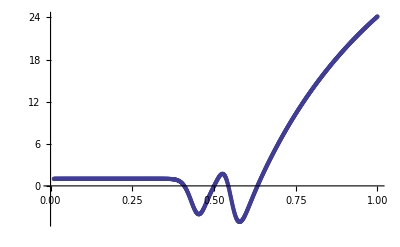

```mathematica
ListPlot[SigmaOldsoln]
```

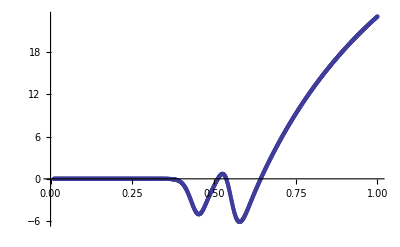

```mathematica
ListPlot[Sigmasoln]
```

```mathematica
ListPlot[Sigmasoln2]
```

-Graphics-

```mathematica
ListPlot[{Sigmasoln1,SigmaOldsoln}]
```

ListPlot::lpn: {Sigmasoln1, {{0.01, 1.001}, {0.011, 1.00164}, {0.012, 1.00217}, {0.013, 1.00262}, {0.014, 1.003}, {0.015, 1.00333}, {0.016, 1.00363}, {0.017, 1.00388}, {0.018, 1.00411}, {0.019, 1.00432}, {0.02, 1.0045}, {0.021, 1.00467}, {0.022, 1.00482}, {0.023, 1.00496}, « 23 », {0.047, 1.00651}, {0.048, 1.00654}, {0.049, 1.00657}, {0.05, 1.0066}, {0.051, 1.00663}, {0.052, 1.00665}, {0.053, 1.00668}, {0.054, 1.0067}, {0.055, 1.00673}, {0.056, 1.00675}, {0.057, 1.00677}, {0.058, 1.00679}, {0.059, 1.00681}, « 941 »}} is not a list of numbers or pairs of numbers.

ListPlot[{Sigmasoln1,{{0.01,1.001},{0.011,1.00164},{0.012,1.00217},{0.013,1.00262},{0.014,1.003},{0.015,1.00333},{0.016,1.00363},{0.017,1.00388},{0.018,1.00411},{0.019,1.00432},{0.02,1.0045},{0.021,1.00467},{0.022,1.00482},{0.023,1.00496},{0.024,1.00508},{0.025,1.0052},{0.026,1.00531},{0.027,1.00541},{0.028,1.0055},{0.029,1.00559},{0.03,1.00567},{0.031,1.00574},{0.032,1.00581},{0.033,1.00588},{0.034,1.00594},{0.035,1.006},{0.036,1.00606},{0.037,1.00611},{0.038,1.00616},{0.039,1.00621},{0.04,1.00625},{0.041,1.00629},{0.042,1.00633},{0.043,1.00637},{0.044,1.00641},{0.045,1.00644},{0.046,1.00648},{0.047,1.00651},{0.048,1.00654},{0.049,1.00657},{0.05,1.0066},{0.051,1.00663},{0.052,1.00665},{0.053,1.00668},{0.054,1.0067},{0.055,1.00673},{0.056,1.00675},{0.057,1.00677},{0.058,1.00679},{0.059,1.00681},{0.06,1.00683},{0.061,1.00685},{0.062,1.00687},{0.063,1.00689},{0.064,1.00691},{0.065,1.00692},{0.066,1.00694},{0.067,1.00696},{0.068,1.00697},{0.069,1.00699},{0.07,1.007},{0.071,1.00701},{0.072,1.00703},{0.073,1.00704},{0.074,1.00705},{0.075,1.00707},{0.076,1.00708},{0.077,1.00709},{0.078,1.0071},{0.079,1.00711},{0.08,1.00713},{0.081,1.00714},{0.082,1.00715},{0.083,1.00716},{0.084,1.00717},{0.085,1.00718},{0.086,1.00719},{0.087,1.0072},{0.088,1.0072},{0.089,1.00721},{0.09,1.00722},{0.091,1.00723},{0.092,1.00724},{0.093,1.00725},{0.094,1.00726},{0.095,1.00726},{0.096,1.00727},{0.097,1.00728},{0.098,1.00729},{0.099,1.00729},{0.1,1.0073},{0.101,1.00731},{0.102,1.00731},{0.103,1.00732},{0.104,1.00733},{0.105,1.00733},{0.106,1.00734},{0.107,1.00735},{0.108,1.00735},{0.109,1.00736},{0.11,1.00736},{0.111,1.00737},{0.112,1.00738},{0.113,1.00738},{0.114,1.00739},{0.115,1.00739},{0.116,1.0074},{0.117,1.0074},{0.118,1.00741},{0.119,1.00741},{0.12,1.00742},{0.121,1.00742},{0.122,1.00743},{0.123,1.00743},{0.124,1.00744},{0.125,1.00744},{0.126,1.00744},{0.127,1.00745},{0.128,1.00745},{0.129,1.00746},{0.13,1.00746},{0.131,1.00747},{0.132,1.00747},{0.133,1.00747},{0.134,1.00748},{0.135,1.00748},{0.136,1.00749},{0.137,1.00749},{0.138,1.00749},{0.139,1.0075},{0.14,1.0075},{0.141,1.0075},{0.142,1.00751},{0.143,1.00751},{0.144,1.00751},{0.145,1.00752},{0.146,1.00752},{0.147,1.00752},{0.148,1.00753},{0.149,1.00753},{0.15,1.00753},{0.151,1.00754},{0.152,1.00754},{0.153,1.00754},{0.154,1.00755},{0.155,1.00755},{0.156,1.00755},{0.157,1.00755},{0.158,1.00756},{0.159,1.00756},{0.16,1.00756},{0.161,1.00757},{0.162,1.00757},{0.163,1.00757},{0.164,1.00757},{0.165,1.00758},{0.166,1.00758},{0.167,1.00758},{0.168,1.00758},{0.169,1.00759},{0.17,1.00759},{0.171,1.00759},{0.172,1.00759},{0.173,1.0076},{0.174,1.0076},{0.175,1.0076},{0.176,1.0076},{0.177,1.0076},{0.178,1.00761},{0.179,1.00761},{0.18,1.00761},{0.181,1.00761},{0.182,1.00762},{0.183,1.00762},{0.184,1.00762},{0.185,1.00762},{0.186,1.00762},{0.187,1.00763},{0.188,1.00763},{0.189,1.00763},{0.19,1.00763},{0.191,1.00763},{0.192,1.00764},{0.193,1.00764},{0.194,1.00764},{0.195,1.00764},{0.196,1.00764},{0.197,1.00764},{0.198,1.00765},{0.199,1.00765},{0.2,1.00765},{0.201,1.00765},{0.202,1.00765},{0.203,1.00766},{0.204,1.00766},{0.205,1.00766},{0.206,1.00766},{0.207,1.00766},{0.208,1.00766},{0.209,1.00767},{0.21,1.00767},{0.211,1.00767},{0.212,1.00767},{0.213,1.00767},{0.214,1.00767},{0.215,1.00767},{0.216,1.00768},{0.217,1.00768},{0.218,1.00768},{0.219,1.00768},{0.22,1.00768},{0.221,1.00768},{0.222,1.00768},{0.223,1.00769},{0.224,1.00769},{0.225,1.00769},{0.226,1.00769},{0.227,1.00769},{0.228,1.00769},{0.229,1.00769},{0.23,1.0077},{0.231,1.0077},{0.232,1.0077},{0.233,1.0077},{0.234,1.0077},{0.235,1.0077},{0.236,1.0077},{0.237,1.0077},{0.238,1.00771},{0.239,1.00771},{0.24,1.00771},{0.241,1.00771},{0.242,1.00771},{0.243,1.00771},{0.244,1.00771},{0.245,1.00771},{0.246,1.00772},{0.247,1.00772},{0.248,1.00772},{0.249,1.00772},{0.25,1.00772},{0.251,1.00772},{0.252,1.00772},{0.253,1.00772},{0.254,1.00772},{0.255,1.00773},{0.256,1.00773},{0.257,1.00773},{0.258,1.00773},{0.259,1.00773},{0.26,1.00773},{0.261,1.00773},{0.262,1.00773},{0.263,1.00773},{0.264,1.00773},{0.265,1.00774},{0.266,1.00774},{0.267,1.00774},{0.268,1.00774},{0.269,1.00774},{0.27,1.00774},{0.271,1.00774},{0.272,1.00774},{0.273,1.00774},{0.274,1.00774},{0.275,1.00775},{0.276,1.00775},{0.277,1.00775},{0.278,1.00775},{0.279,1.00775},{0.28,1.00775},{0.281,1.00775},{0.282,1.00775},{0.283,1.00775},{0.284,1.00775},{0.285,1.00775},{0.286,1.00775},{0.287,1.00776},{0.288,1.00776},{0.289,1.00776},{0.29,1.00776},{0.291,1.00776},{0.292,1.00776},{0.293,1.00776},{0.294,1.00776},{0.295,1.00776},{0.296,1.00776},{0.297,1.00776},{0.298,1.00776},{0.299,1.00776},{0.3,1.00776},{0.301,1.00776},{0.302,1.00776},{0.303,1.00776},{0.304,1.00776},{0.305,1.00776},{0.306,1.00776},{0.307,1.00776},{0.308,1.00776},{0.309,1.00776},{0.31,1.00776},{0.311,1.00775},{0.312,1.00775},{0.313,1.00775},{0.314,1.00774},{0.315,1.00774},{0.316,1.00773},{0.317,1.00773},{0.318,1.00772},{0.319,1.00771},{0.32,1.0077},{0.321,1.00769},{0.322,1.00768},{0.323,1.00766},{0.324,1.00765},{0.325,1.00763},{0.326,1.0076},{0.327,1.00758},{0.328,1.00755},{0.329,1.00751},{0.33,1.00747},{0.331,1.00743},{0.332,1.00738},{0.333,1.00732},{0.334,1.00726},{0.335,1.00718},{0.336,1.0071},{0.337,1.007},{0.338,1.0069},{0.339,1.00677},{0.34,1.00664},{0.341,1.00648},{0.342,1.00631},{0.343,1.00611},{0.344,1.00589},{0.345,1.00564},{0.346,1.00536},{0.347,1.00505},{0.348,1.0047},{0.349,1.00431},{0.35,1.00387},{0.351,1.00338},{0.352,1.00283},{0.353,1.00222},{0.354,1.00153},{0.355,1.00077},{0.356,0.999921},{0.357,0.998977},{0.358,0.997927},{0.359,0.996761},{0.36,0.995467},{0.361,0.994033},{0.362,0.992443},{0.363,0.990684},{0.364,0.988738},{0.365,0.986588},{0.366,0.984214},{0.367,0.981595},{0.368,0.978709},{0.369,0.975531},{0.37,0.972034},{0.371,0.96819},{0.372,0.963969},{0.373,0.959337},{0.374,0.954258},{0.375,0.948696},{0.376,0.942609},{0.377,0.935955},{0.378,0.928685},{0.379,0.920753},{0.38,0.912104},{0.381,0.902684},{0.382,0.892433},{0.383,0.881288},{0.384,0.869185},{0.385,0.856052},{0.386,0.841818},{0.387,0.826404},{0.388,0.809732},{0.389,0.791715},{0.39,0.772268},{0.391,0.751298},{0.392,0.728711},{0.393,0.704409},{0.394,0.678292},{0.395,0.650256},{0.396,0.620195},{0.397,0.588001},{0.398,0.553565},{0.399,0.516776},{0.4,0.477523},{0.401,0.435695},{0.402,0.391183},{0.403,0.343877},{0.404,0.293673},{0.405,0.240468},{0.406,0.184165},{0.407,0.124671},{0.408,0.061903},{0.409,-0.00421589},{0.41,-0.0737522},{0.411,-0.146761},{0.412,-0.223286},{0.413,-0.303354},{0.414,-0.386978},{0.415,-0.474154},{0.416,-0.564858},{0.417,-0.659045},{0.418,-0.756649},{0.419,-0.85758},{0.42,-0.961722},{0.421,-1.06893},{0.422,-1.17905},{0.423,-1.29187},{0.424,-1.40717},{0.425,-1.52469},{0.426,-1.64416},{0.427,-1.76525},{0.428,-1.88763},{0.429,-2.01092},{0.43,-2.13472},{0.431,-2.25862},{0.432,-2.38217},{0.433,-2.50489},{0.434,-2.6263},{0.435,-2.74591},{0.436,-2.8632},{0.437,-2.97764},{0.438,-3.08872},{0.439,-3.19592},{0.44,-3.2987},{0.441,-3.39658},{0.442,-3.48905},{0.443,-3.57565},{0.444,-3.65593},{0.445,-3.72946},{0.446,-3.79588},{0.447,-3.85483},{0.448,-3.90601},{0.449,-3.94917},{0.45,-3.9841},{0.451,-4.01065},{0.452,-4.02871},{0.453,-4.03823},{0.454,-4.03922},{0.455,-4.03174},{0.456,-4.01591},{0.457,-3.99187},{0.458,-3.95986},{0.459,-3.92013},{0.46,-3.87298},{0.461,-3.81875},{0.462,-3.75782},{0.463,-3.69059},{0.464,-3.6175},{0.465,-3.53899},{0.466,-3.45552},{0.467,-3.36756},{0.468,-3.27559},{0.469,-3.18007},{0.47,-3.08148},{0.471,-2.98026},{0.472,-2.87685},{0.473,-2.77167},{0.474,-2.66511},{0.475,-2.55754},{0.476,-2.4493},{0.477,-2.34071},{0.478,-2.23203},{0.479,-2.12352},{0.48,-2.0154},{0.481,-1.90784},{0.482,-1.80099},{0.483,-1.69498},{0.484,-1.5899},{0.485,-1.48581},{0.486,-1.38274},{0.487,-1.28072},{0.488,-1.17974},{0.489,-1.07977},{0.49,-0.98077},{0.491,-0.882691},{0.492,-0.785471},{0.493,-0.689039},{0.494,-0.593326},{0.495,-0.498257},{0.496,-0.403764},{0.497,-0.309782},{0.498,-0.216255},{0.499,-0.123142},{0.5,-0.0304112},{0.501,0.0619473},{0.502,0.153926},{0.503,0.245492},{0.504,0.336592},{0.505,0.42714},{0.506,0.517025},{0.507,0.606103},{0.508,0.694198},{0.509,0.781099},{0.51,0.866562},{0.511,0.950306},{0.512,1.03202},{0.513,1.11134},{0.514,1.1879},{0.515,1.26127},{0.516,1.33101},{0.517,1.39663},{0.518,1.45764},{0.519,1.51351},{0.52,1.5637},{0.521,1.60765},{0.522,1.64481},{0.523,1.67461},{0.524,1.69649},{0.525,1.7099},{0.526,1.71432},{0.527,1.70925},{0.528,1.69422},{0.529,1.66879},{0.53,1.6326},{0.531,1.58531},{0.532,1.52667},{0.533,1.45648},{0.534,1.37463},{0.535,1.28108},{0.536,1.17586},{0.537,1.05911},{0.538,0.931041},{0.539,0.791964},{0.54,0.64227},{0.541,0.48244},{0.542,0.313038},{0.543,0.134711},{0.544,-0.0518208},{0.545,-0.245767},{0.546,-0.446276},{0.547,-0.652438},{0.548,-0.863301},{0.549,-1.07787},{0.55,-1.29514},{0.551,-1.51406},{0.552,-1.73359},{0.553,-1.95269},{0.554,-2.17034},{0.555,-2.38551},{0.556,-2.59723},{0.557,-2.80457},{0.558,-3.00662},{0.559,-3.20254},{0.56,-3.39156},{0.561,-3.57294},{0.562,-3.74604},{0.563,-3.91026},{0.564,-4.06511},{0.565,-4.21014},{0.566,-4.345},{0.567,-4.46939},{0.568,-4.58309},{0.569,-4.68596},{0.57,-4.77792},{0.571,-4.85895},{0.572,-4.92911},{0.573,-4.98848},{0.574,-5.03722},{0.575,-5.07553},{0.576,-5.10366},{0.577,-5.12188},{0.578,-5.1305},{0.579,-5.12988},{0.58,-5.12036},{0.581,-5.10233},{0.582,-5.07619},{0.583,-5.04234},{0.584,-5.00121},{0.585,-4.95319},{0.586,-4.89872},{0.587,-4.83821},{0.588,-4.77206},{0.589,-4.70067},{0.59,-4.62443},{0.591,-4.54373},{0.592,-4.45892},{0.593,-4.37037},{0.594,-4.2784},{0.595,-4.18333},{0.596,-4.08548},{0.597,-3.98513},{0.598,-3.88254},{0.599,-3.77799},{0.6,-3.67169},{0.601,-3.56388},{0.602,-3.45477},{0.603,-3.34453},{0.604,-3.23335},{0.605,-3.1214},{0.606,-3.00881},{0.607,-2.89572},{0.608,-2.78226},{0.609,-2.66854},{0.61,-2.55465},{0.611,-2.44069},{0.612,-2.32674},{0.613,-2.21286},{0.614,-2.09913},{0.615,-1.98559},{0.616,-1.8723},{0.617,-1.7593},{0.618,-1.64663},{0.619,-1.53431},{0.62,-1.42237},{0.621,-1.31084},{0.622,-1.19973},{0.623,-1.08905},{0.624,-0.978824},{0.625,-0.869054},{0.626,-0.759747},{0.627,-0.650906},{0.628,-0.542533},{0.629,-0.43463},{0.63,-0.327195},{0.631,-0.220226},{0.632,-0.11372},{0.633,-0.00767264},{0.634,0.0979208},{0.635,0.203065},{0.636,0.307767},{0.637,0.412032},{0.638,0.515866},{0.639,0.619276},{0.64,0.722268},{0.641,0.824849},{0.642,0.927026},{0.643,1.0288},{0.644,1.13019},{0.645,1.23119},{0.646,1.33182},{0.647,1.43207},{0.648,1.53195},{0.649,1.63147},{0.65,1.73064},{0.651,1.82946},{0.652,1.92793},{0.653,2.02605},{0.654,2.12385},{0.655,2.22131},{0.656,2.31844},{0.657,2.41525},{0.658,2.51173},{0.659,2.60791},{0.66,2.70376},{0.661,2.79931},{0.662,2.89456},{0.663,2.98949},{0.664,3.08413},{0.665,3.17847},{0.666,3.27252},{0.667,3.36627},{0.668,3.45973},{0.669,3.5529},{0.67,3.64579},{0.671,3.73839},{0.672,3.83072},{0.673,3.92276},{0.674,4.01452},{0.675,4.106},{0.676,4.19722},{0.677,4.28815},{0.678,4.37882},{0.679,4.46922},{0.68,4.55934},{0.681,4.6492},{0.682,4.7388},{0.683,4.82813},{0.684,4.9172},{0.685,5.006},{0.686,5.09455},{0.687,5.18284},{0.688,5.27087},{0.689,5.35864},{0.69,5.44616},{0.691,5.53342},{0.692,5.62043},{0.693,5.70719},{0.694,5.7937},{0.695,5.87996},{0.696,5.96598},{0.697,6.05174},{0.698,6.13726},{0.699,6.22253},{0.7,6.30756},{0.701,6.39235},{0.702,6.47689},{0.703,6.5612},{0.704,6.64526},{0.705,6.72909},{0.706,6.81268},{0.707,6.89603},{0.708,6.97915},{0.709,7.06203},{0.71,7.14468},{0.711,7.2271},{0.712,7.30928},{0.713,7.39123},{0.714,7.47296},{0.715,7.55445},{0.716,7.63572},{0.717,7.71676},{0.718,7.79758},{0.719,7.87817},{0.72,7.95854},{0.721,8.03868},{0.722,8.11861},{0.723,8.19831},{0.724,8.27779},{0.725,8.35705},{0.726,8.43609},{0.727,8.51492},{0.728,8.59353},{0.729,8.67192},{0.73,8.7501},{0.731,8.82806},{0.732,8.90582},{0.733,8.98336},{0.734,9.06068},{0.735,9.1378},{0.736,9.21471},{0.737,9.29141},{0.738,9.3679},{0.739,9.44419},{0.74,9.52027},{0.741,9.59614},{0.742,9.67181},{0.743,9.74727},{0.744,9.82254},{0.745,9.8976},{0.746,9.97246},{0.747,10.0471},{0.748,10.1216},{0.749,10.1958},{0.75,10.2699},{0.751,10.3438},{0.752,10.4174},{0.753,10.4909},{0.754,10.5642},{0.755,10.6373},{0.756,10.7102},{0.757,10.7829},{0.758,10.8554},{0.759,10.9277},{0.76,10.9998},{0.761,11.0717},{0.762,11.1435},{0.763,11.215},{0.764,11.2864},{0.765,11.3576},{0.766,11.4286},{0.767,11.4994},{0.768,11.57},{0.769,11.6405},{0.77,11.7107},{0.771,11.7808},{0.772,11.8507},{0.773,11.9204},{0.774,11.99},{0.775,12.0593},{0.776,12.1285},{0.777,12.1975},{0.778,12.2663},{0.779,12.335},{0.78,12.4035},{0.781,12.4718},{0.782,12.5399},{0.783,12.6078},{0.784,12.6756},{0.785,12.7432},{0.786,12.8106},{0.787,12.8779},{0.788,12.945},{0.789,13.0119},{0.79,13.0786},{0.791,13.1452},{0.792,13.2116},{0.793,13.2779},{0.794,13.3439},{0.795,13.4099},{0.796,13.4756},{0.797,13.5412},{0.798,13.6066},{0.799,13.6718},{0.8,13.7369},{0.801,13.8019},{0.802,13.8666},{0.803,13.9312},{0.804,13.9957},{0.805,14.0599},{0.806,14.1241},{0.807,14.188},{0.808,14.2518},{0.809,14.3155},{0.81,14.379},{0.811,14.4423},{0.812,14.5055},{0.813,14.5685},{0.814,14.6314},{0.815,14.6941},{0.816,14.7566},{0.817,14.8191},{0.818,14.8813},{0.819,14.9434},{0.82,15.0054},{0.821,15.0672},{0.822,15.1288},{0.823,15.1903},{0.824,15.2517},{0.825,15.3129},{0.826,15.3739},{0.827,15.4348},{0.828,15.4956},{0.829,15.5562},{0.83,15.6166},{0.831,15.677},{0.832,15.7371},{0.833,15.7972},{0.834,15.8571},{0.835,15.9168},{0.836,15.9764},{0.837,16.0359},{0.838,16.0952},{0.839,16.1544},{0.84,16.2134},{0.841,16.2723},{0.842,16.331},{0.843,16.3896},{0.844,16.4481},{0.845,16.5065},{0.846,16.5647},{0.847,16.6227},{0.848,16.6806},{0.849,16.7384},{0.85,16.7961},{0.851,16.8536},{0.852,16.911},{0.853,16.9682},{0.854,17.0253},{0.855,17.0823},{0.856,17.1392},{0.857,17.1959},{0.858,17.2525},{0.859,17.3089},{0.86,17.3652},{0.861,17.4214},{0.862,17.4775},{0.863,17.5334},{0.864,17.5892},{0.865,17.6449},{0.866,17.7004},{0.867,17.7558},{0.868,17.8111},{0.869,17.8663},{0.87,17.9213},{0.871,17.9762},{0.872,18.031},{0.873,18.0856},{0.874,18.1401},{0.875,18.1945},{0.876,18.2488},{0.877,18.303},{0.878,18.357},{0.879,18.4109},{0.88,18.4647},{0.881,18.5184},{0.882,18.5719},{0.883,18.6253},{0.884,18.6786},{0.885,18.7318},{0.886,18.7849},{0.887,18.8378},{0.888,18.8906},{0.889,18.9433},{0.89,18.9959},{0.891,19.0484},{0.892,19.1007},{0.893,19.153},{0.894,19.2051},{0.895,19.2571},{0.896,19.309},{0.897,19.3607},{0.898,19.4124},{0.899,19.4639},{0.9,19.5153},{0.901,19.5666},{0.902,19.6178},{0.903,19.6689},{0.904,19.7199},{0.905,19.7707},{0.906,19.8215},{0.907,19.8721},{0.908,19.9226},{0.909,19.973},{0.91,20.0233},{0.911,20.0735},{0.912,20.1236},{0.913,20.1735},{0.914,20.2234},{0.915,20.2731},{0.916,20.3228},{0.917,20.3723},{0.918,20.4217},{0.919,20.4711},{0.92,20.5203},{0.921,20.5694},{0.922,20.6184},{0.923,20.6672},{0.924,20.716},{0.925,20.7647},{0.926,20.8133},{0.927,20.8617},{0.928,20.9101},{0.929,20.9584},{0.93,21.0065},{0.931,21.0546},{0.932,21.1025},{0.933,21.1504},{0.934,21.1981},{0.935,21.2458},{0.936,21.2933},{0.937,21.3407},{0.938,21.3881},{0.939,21.4353},{0.94,21.4824},{0.941,21.5295},{0.942,21.5764},{0.943,21.6232},{0.944,21.67},{0.945,21.7166},{0.946,21.7632},{0.947,21.8096},{0.948,21.8559},{0.949,21.9022},{0.95,21.9483},{0.951,21.9944},{0.952,22.0403},{0.953,22.0862},{0.954,22.132},{0.955,22.1776},{0.956,22.2232},{0.957,22.2687},{0.958,22.314},{0.959,22.3593},{0.96,22.4045},{0.961,22.4496},{0.962,22.4946},{0.963,22.5395},{0.964,22.5843},{0.965,22.6291},{0.966,22.6737},{0.967,22.7182},{0.968,22.7627},{0.969,22.807},{0.97,22.8513},{0.971,22.8955},{0.972,22.9396},{0.973,22.9835},{0.974,23.0274},{0.975,23.0713},{0.976,23.115},{0.977,23.1586},{0.978,23.2022},{0.979,23.2456},{0.98,23.289},{0.981,23.3322},{0.982,23.3754},{0.983,23.4185},{0.984,23.4615},{0.985,23.5045},{0.986,23.5473},{0.987,23.5901},{0.988,23.6327},{0.989,23.6753},{0.99,23.7178},{0.991,23.7602},{0.992,23.8025},{0.993,23.8448},{0.994,23.8869},{0.995,23.929},{0.996,23.971},{0.997,24.0128},{0.998,24.0547},{0.999,24.0964},{1.,24.138}}}]

```mathematica
Sigmasoln1 = Table[{ulist[[i]],Sigmasoln2list[[i]]+1},{i,1,Length[ulist]}];
```

```mathematica
Comparesoln = Table[{ulist[[i]],Sigmasolnlist[[i]]-(SigmaOldsolnlist[[i]]-1)},{i,1,Length[ulist]}];
```

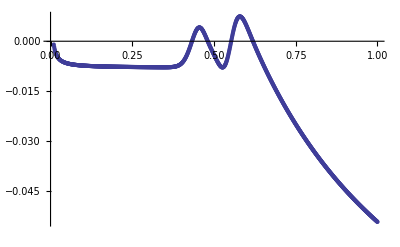

```mathematica
ListPlot[Comparesoln]
```

### BTZ parameter

```mathematica
?B
```

Notebook$$58$581568`B

```mathematica
BTZ1 = (1/u+ λ +u^5 sigmasubscale[u])^2 ⅇ^B[v,u]/.Bsubtract/.novrule/.u->1/.sigmasubscale[1]->sigmasubscaleathorlist/.λ->lamblist/.Bsub[1]->Bsubathorlist
%//CForm
```

ⅇ^Bsubathorlist (1+lamblist+sigmasubscaleathorlist)^2

Power(E,Bsubathorlist)*Power(1 + lamblist + sigmasubscaleathorlist,2)

```mathematica
BTZ2 =FullSimplify[(-u^2 D[ -u^2 D[ (1/u+ λ +u^5 sigmasubscale[u])^2 ⅇ^(-2B[v,u]),u],u]/.Bsubtract/.novrule/.u->1)]
%/.sigmasubscale[1]->sigmasubscaleathorlist/.sigmasubscale'[1]->dsigmasubscaleathorlist/.sigmasubscale''[1]->ddsigmasubscaleathorlist/.λ->lamblist/.Derivative[0,1][Bsub][1]->dBsubathorlist/.Derivative[0,2][Bsub][1]->ddBsubathorlist/.Bsub[1]->Bsubathorlist
%//CForm
```

2 ⅇ^(-2 Bsub[1]) (2 (1+λ+sigmasubscale[1]) (-1+5 sigmasubscale[1]+sigmasubscale'[1])+(-1+5 sigmasubscale[1]+sigmasubscale'[1])^2+(1+λ+sigmasubscale[1]) (2+20 sigmasubscale[1]+10 sigmasubscale'[1]+sigmasubscale''[1])+(2 (1+λ+sigmasubscale[1])^2 (fxy^2 (1+2 λ (-2+5 λ))-3 g^2 (3 Bsub[1]+Bsub^(0,1)[1])))/(3 g^2)+(4 (1+λ+sigmasubscale[1]) (-1+5 sigmasubscale[1]+sigmasubscale'[1]) (fxy^2 (1+2 λ (-2+5 λ))-3 g^2 (3 Bsub[1]+Bsub^(0,1)[1])))/(3 g^2)+(2 (1+λ+sigmasubscale[1])^2 (fxy^2 (1+2 λ (-2+5 λ))-3 g^2 (3 Bsub[1]+Bsub^(0,1)[1]))^2)/(9 g^4)+((1+λ+sigmasubscale[1])^2 (fxy^2 (7+2 λ (-18+55 λ))-3 g^2 (6 (Bsub[1]+Bsub^(0,1)[1])+Bsub^(0,2)[1])))/(3 g^2))

2 ⅇ^(-2 Bsubathorlist) ((2 (-3 (3 Bsubathorlist+dBsubathorlist) g^2+fxy^2 (1+2 lamblist (-2+5 lamblist))) (1+lamblist+sigmasubscaleathorlist)^2)/(3 g^2)+(2 (-3 (3 Bsubathorlist+dBsubathorlist) g^2+fxy^2 (1+2 lamblist (-2+5 lamblist)))^2 (1+lamblist+sigmasubscaleathorlist)^2)/(9 g^4)+((-3 (6 (Bsubathorlist+dBsubathorlist)+ddBsubathorlist) g^2+fxy^2 (7+2 lamblist (-18+55 lamblist))) (1+lamblist+sigmasubscaleathorlist)^2)/(3 g^2)+2 (1+lamblist+sigmasubscaleathorlist) (-1+dsigmasubscaleathorlist+5 sigmasubscaleathorlist)+1/(3 g^2)4 (-3 (3 Bsubathorlist+dBsubathorlist) g^2+fxy^2 (1+2 lamblist (-2+5 lamblist))) (1+lamblist+sigmasubscaleathorlist) (-1+dsigmasubscaleathorlist+5 sigmasubscaleathorlist)+(-1+dsigmasubscaleathorlist+5 sigmasubscaleathorlist)^2+(1+lamblist+sigmasubscaleathorlist) (2+ddsigmasubscaleathorlist+10 dsigmasubscaleathorlist+20 sigmasubscaleathorlist))

(2*((2*(-3*(3*Bsubathorlist + dBsubathorlist)*Power(g,2) + Power(fxy,2)*(1 + 2*lamblist*(-2 + 5*lamblist)))*Power(1 + lamblist + sigmasubscaleathorlist,2))/
        (3.*Power(g,2)) + (2*Power(-3*(3*Bsubathorlist + dBsubathorlist)*Power(g,2) + Power(fxy,2)*(1 + 2*lamblist*(-2 + 5*lamblist)),2)*
          Power(1 + lamblist + sigmasubscaleathorlist,2))/(9.*Power(g,4)) + 
       ((-3*(6*(Bsubathorlist + dBsubathorlist) + ddBsubathorlist)*Power(g,2) + Power(fxy,2)*(7 + 2*lamblist*(-18 + 55*lamblist)))*
          Power(1 + lamblist + sigmasubscaleathorlist,2))/(3.*Power(g,2)) + 
       2*(1 + lamblist + sigmasubscaleathorlist)*(-1 + dsigmasubscaleathorlist + 5*sigmasubscaleathorlist) + 
       (4*(-3*(3*Bsubathorlist + dBsubathorlist)*Power(g,2) + Power(fxy,2)*(1 + 2*lamblist*(-2 + 5*lamblist)))*(1 + lamblist + sigmasubscaleathorlist)*
          (-1 + dsigmasubscaleathorlist + 5*sigmasubscaleathorlist))/(3.*Power(g,2)) + Power(-1 + dsigmasubscaleathorlist + 5*sigmasubscaleathorlist,2) + 
       (1 + lamblist + sigmasubscaleathorlist)*(2 + ddsigmasubscaleathorlist + 10*dsigmasubscaleathorlist + 20*sigmasubscaleathorlist)))/Power(E,2*Bsubathorlist)

```mathematica
(1/u+ λ +sigmasubscale[u])^2 ⅇ^B[v,u]/.Bsubtract/.novrule
```

ⅇ^(u^3 Bsub[u]+((fxy^2 u^4)/(3 g^2)-(4 fxy^2 u^5 λ)/(3 g^2)+(10 fxy^2 u^6 λ^2)/(3 g^2)) Log[1/u]) (1/u+λ+sigmasubscale[u])^2

### Boundary Stress-Energy Tensor

Ok, from our coordinate transform (changing (u,v) out for (ρ, t))  from Eddington-Finklestein to Fefferman-Graham, we were able to put our metric into the following form.  (see Coordinate Transform 5 mm)

```mathematica
({{-1/ρ^2+(ρ^2 (-fxy^2-18 g^2 a[2,0]))/(24 g^2)-(fxy^2 ρ^2 Log[ρ^2])/(4 g^2), 0}, {0, 1/ρ^2}})//MatrixForm
```

(-1/ρ^2+(ρ^2 (-fxy^2-18 g^2 a[2,0]))/(24 g^2)-(fxy^2 ρ^2 Log[ρ^2])/(4 g^2) | 0
0 | 1/ρ^2)

The remainder of the metric also undergoes a coordinate change.  (see Coordinate Transform).
The result is...

```mathematica
gbndrydd = {{ρ^2 (-1/ρ^2+(ρ^2 (-fxy^2-18 g^2 a[2,0]))/(24 g^2)-(fxy^2 ρ^2 LOG[R])/(2 g^2)),0,0,0},{0,ρ^2 (1/ρ^2+(fxy^2 ρ^2)/(24 g^2)-1/4 ρ^2 a[2,0]+ρ^2 b[4,0]-(fxy^2 ρ^2 LOG[R])/(2 g^2)),0,0},{0,0,ρ^2 (1/ρ^2+(fxy^2 ρ^2)/(24 g^2)-1/4 ρ^2 a[2,0]+ρ^2 b[4,0]-(fxy^2 ρ^2 LOG[R])/(2 g^2)),0},{0,0,0,ρ^2 (1/ρ^2+(fxy^2 ρ^2)/(24 g^2)-1/4 ρ^2 a[2,0]-2 ρ^2 b[4,0]+(fxy^2 ρ^2 LOG[R])/(2 g^2))}}
```

{{ρ^2 (-1/ρ^2+(ρ^2 (-fxy^2-18 g^2 a[2,0]))/(24 g^2)-(fxy^2 ρ^2 LOG[R])/(2 g^2)),0,0,0},{0,ρ^2 (1/ρ^2+(fxy^2 ρ^2)/(24 g^2)-1/4 ρ^2 a[2,0]+ρ^2 b[4,0]-(fxy^2 ρ^2 LOG[R])/(2 g^2)),0,0},{0,0,ρ^2 (1/ρ^2+(fxy^2 ρ^2)/(24 g^2)-1/4 ρ^2 a[2,0]+ρ^2 b[4,0]-(fxy^2 ρ^2 LOG[R])/(2 g^2)),0},{0,0,0,ρ^2 (1/ρ^2+(fxy^2 ρ^2)/(24 g^2)-1/4 ρ^2 a[2,0]-2 ρ^2 b[4,0]+(fxy^2 ρ^2 LOG[R])/(2 g^2))}}

To match FG we should be matching to log(r^2) or 2 log(r)

```mathematica
g0dd =ConstantArray[0,{4,4}];
g1dd = ConstantArray[0,{4,4}];
g2dd = ConstantArray[0,{4,4}];
g3dd = ConstantArray[0,{4,4}];
g4dd = ConstantArray[0,{4,4}];
h4dd = ConstantArray[0,{4,4}];
Do[Do[g0dd[[i,j]]= Coefficient[Coefficient[gbndrydd[[i,j]],ρ,0],2LOG[R],0],{i,1,4}],{j,1,4}]
Do[Do[g1dd[[i,j]]= Coefficient[Coefficient[gbndrydd[[i,j]],ρ,1],2LOG[R],0],{i,1,4}],{j,1,4}]
Do[Do[g2dd[[i,j]]= Coefficient[Coefficient[gbndrydd[[i,j]],ρ,2],2LOG[R],0],{i,1,4}],{j,1,4}]
Do[Do[g3dd[[i,j]]= Coefficient[Coefficient[gbndrydd[[i,j]],ρ,3],2LOG[R],0],{i,1,4}],{j,1,4}]
Do[Do[g4dd[[i,j]]= Coefficient[Coefficient[gbndrydd[[i,j]],ρ,4],2LOG[R],0],{i,1,4}],{j,1,4}]
Do[Do[h4dd[[i,j]]= Coefficient[Coefficient[gbndrydd[[i,j]],ρ,4],2LOG[R],1],{i,1,4}],{j,1,4}]
g0dd
g1dd
g2dd
g3dd
g4dd
h4dd
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{-fxy^2/(24 g^2)-3/4 a[2,0],0,0,0},{0,fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0],0,0},{0,0,fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0],0},{0,0,0,fxy^2/(24 g^2)-1/4 a[2,0]-2 b[4,0]}}

{{-fxy^2/(4 g^2),0,0,0},{0,-fxy^2/(4 g^2),0,0},{0,0,-fxy^2/(4 g^2),0},{0,0,0,fxy^2/(4 g^2)}}

```mathematica
g0dd //MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
g4dd//MatrixForm
```

(-fxy^2/(24 g^2)-3/4 a[2,0] | 0 | 0 | 0
0 | fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0] | 0 | 0
0 | 0 | fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0] | 0
0 | 0 | 0 | fxy^2/(24 g^2)-1/4 a[2,0]-2 b[4,0])

```mathematica
h4dd//MatrixForm
```

(-fxy^2/(4 g^2) | 0 | 0 | 0
0 | -fxy^2/(4 g^2) | 0 | 0
0 | 0 | -fxy^2/(4 g^2) | 0
0 | 0 | 0 | fxy^2/(4 g^2))

From Skenderis, we know that < T_(i j)> = 4/(16 π G_N)[g_((4)i j)] since g_(2) = 0

So... T_(i j) is

```mathematica
4/(16π Subscript[G, N])({{-fxy^2/(24 g^2)-3/4 a[2,0], 0, 0, 0}, {0, fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0], 0, 0}, {0, 0, fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0], 0}, {0, 0, 0, fxy^2/(24 g^2)-1/4 a[2,0]-2 b[4,0]}})
```

{{(-fxy^2/(24 g^2)-3/4 a[2,0])/(4 π G_N),0,0,0},{0,(fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0])/(4 π G_N),0,0},{0,0,(fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0])/(4 π G_N),0},{0,0,0,(fxy^2/(24 g^2)-1/4 a[2,0]-2 b[4,0])/(4 π G_N)}}

Yaffe and Chesler say (T^μ)_ν= N_c^2/(2 π^2)diag(-ϵ, P_x, P_y, P_z) .  From this we can solve for our energy density (moving one index down gives extra minus sign).

From Skenderis, we know that < T_(i j)> = (4 L^3)/(16 π G_N)[g_((4)i j)] since g_(2) = 0

According to Skenderis, I can add a finite local counterterm proportional to the trace anomaly, and that will change the coefficient of the contribution of h4 to my stress energy. So T is scheme dependent up to adding some amount of h4 to my stress energy.

I will choose the following scheme.

```mathematica
({{-fxy^2/(24 g^2)-3/4 a[2,0], 0, 0, 0}, {0, fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0], 0, 0}, {0, 0, fxy^2/(24 g^2)-1/4 a[2,0]+b[4,0], 0}, {0, 0, 0, fxy^2/(24 g^2)-1/4 a[2,0]-2 b[4,0]}})+ (-1/6)({{-fxy^2/(4 g^2), 0, 0, 0}, {0, -fxy^2/(4 g^2), 0, 0}, {0, 0, -fxy^2/(4 g^2), 0}, {0, 0, 0, fxy^2/(4 g^2)}})//MatrixForm
```

(-3/4 a[2,0] | 0 | 0 | 0
0 | fxy^2/(12 g^2)-1/4 a[2,0]+b[4,0] | 0 | 0
0 | 0 | fxy^2/(12 g^2)-1/4 a[2,0]+b[4,0] | 0
0 | 0 | 0 | -1/4 a[2,0]-2 b[4,0])

Also note, that according to Yaffe, G_N = π/2 L^3/N_c^2, so the prefactor could read instead... < T_(i j)> = N_c^2/(2 π^2) [ ]

To get the free energy, f = ϵ - Ts, we must factor out an (4 L^3)/(16 π G_N) from T*s as well, T = h'/(4π),  s = Σ^3/(4 G_N) ,
then, if Energy Density = N_c^2/(2 π^2) (ϵ), then Free energy density = N_c^2/(2 π^2) f,   and f = ϵ - 2 π^2/N_c^2Ts = ϵ - 4 π G_N/L^3T s = ϵ - π T Σ^3